```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/berni/Dropbox/Projects/RapidiX/RapidiX/XS

```mathematica
<<IntegralStuff`
<<PolyLog`
```

```mathematica
XbToX=Get["~/Dropbox/PhD/MathematicaPackages/PolyLog/G012XbToX.m"];
XToXb=Get["~/Dropbox/PhD/MathematicaPackages/PolyLog/G012XToXb.m"];
```

```mathematica
LogRep2={
Log[1-x1]^a_.:>ToExpression["Lx1"<>ToString[a]],
Log[1-x2]^a_.:>ToExpression["Lx2"<>ToString[a]],
Log[1+x1]^a_.:>ToExpression["Lmx1"<>ToString[a]],
Log[1+x2]^a_.:>ToExpression["Lmx2"<>ToString[a]]
};
LogReRep=Table[
{
ToExpression["Lx1"<>ToString[i]]->Log[1-x1]^i,
ToExpression["Lx2"<>ToString[i]]->Log[1-x2]^i,
ToExpression["Lmx1"<>ToString[i]]->Log[1+x1]^i,
ToExpression["Lmx2"<>ToString[i]]->Log[1+x2]^i
}
,{i,1,5}]//Flatten;
```

```mathematica
delcoefrep={delcoef0->1,delcoef1->1,delcoef2->1,delcoef3->1,delcoef4->1,delcoef5->1,delcoef6->1,delcoefm1->1,delcoefm2->1};
delcoefrep0=#[[1]]->0&/@delcoefrep;
```

```mathematica
powrep={x1^a_ /;a>0:>ToExpression["x1"<>ToString[a]],x2^a_/;a>0:>ToExpression["x2"<>ToString[a]]};
```

```mathematica
ConstRep={G[0,1]->0,G[0,0,1]->0,G[0,1,0,0]->0,G[0,1,0,0]->0,G[0,0,0,1]->0,G[1,0,1]->π^2/6,G[0,1,0,1]->2 Zeta[3],G[0,0,1,1]->-Zeta[3],G[-1,1,1]->-π^2/12+Log[2]^2/2,G[0,1,1]->-π^2/6,G[0,-1,1]->π^2/12,G[0,1,1,1]->Zeta[3],G[0,0,0,1,1]->-π^4/90,G[0,0,1,0,0]->0,G[0,0,1,0,1]->π^4/30,G[0,0,1,1,1]->π^4/360,G[0,1,0,0,1]->-π^4/30,G[0,1,0,1,1]->π^4/120,G[0,1,1,0,1]->-π^4/72,G[0,1,1,1,1]->-π^4/90,G[0,0,0,0,1]->0,G[1,0,0,1]->-Zeta[3],G[0,1,0,0,0]->0,G[0,1,1,0,0]->0,G[1,0,1,0,0]->0,G[0,0,0,0,1,1]->-Zeta[5],G[0,0,0,1,0,0]->0,G[0,0,0,1,0,1]->4 Zeta[5],G[0,0,0,1,1,1]->-1/6 π^2 Zeta[3]+2 Zeta[5],G[0,0,1,0,0,0]->0,G[0,0,1,0,0,1]->-6 Zeta[5],G[0,0,1,0,1,1]->1/2 π^2 Zeta[3]-(11 Zeta[5])/2,G[0,0,1,1,0,0]->0,G[0,0,1,1,0,1]->-Zeta[5]/2,G[0,1,0,0,0,1]->4 Zeta[5],G[0,1,0,0,1,1]->-1/3 π^2 Zeta[3]+(9 Zeta[5])/2,G[0,1,0,1,0,0]->0,G[0,1,0,1,0,1]->-1/3 π^2 Zeta[3]+2 Zeta[5],G[0,1,1,0,0,1]->1/6 π^2 Zeta[3]-Zeta[5]/2,G[0,0,1,1,1,1]->1/6 π^2 Zeta[3]-2 Zeta[5],G[0,1,0,1,1,1]->-1/2 π^2 Zeta[3]+(11 Zeta[5])/2,G[0,1,1,0,1,1]->1/3 π^2 Zeta[3]-(9 Zeta[5])/2,G[0,1,1,1,0,1]->-1/6 π^2 Zeta[3]+3 Zeta[5],G[0,1,1,1,1,1]->Zeta[5]};
```

## NLO

```mathematica
nr=1;
p1="q";
p2="g";
```

```mathematica
LogRep={
Log[1-x1]^a_.:>ToExpression["Lx1"<>ToString[a]],
Log[1-x2]^a_.:>ToExpression["Lx2"<>ToString[a]],
Log[1+x1]^a_.:>ToExpression["Lmx1"<>ToString[a]],
Log[1+x2]^a_.:>ToExpression["Lmx2"<>ToString[a]]
}
```

{Log[1-x1]^(a_.):>ToExpression[Lx1<>ToString[a]],Log[1-x2]^(a_.):>ToExpression[Lx2<>ToString[a]],Log[1+x1]^(a_.):>ToExpression[Lmx1<>ToString[a]],Log[1+x2]^(a_.):>ToExpression[Lmx2<>ToString[a]]}

```mathematica
(*vars=Table[{Log[1-x1]^i,Log[1+x1]^i,Log[1-x2]^i,Log[1+x2]^i},{i,1,5}]//Flatten;
vars2=vars/.LogRep;
ostr="";
For[i=1,i≤Length[vars],i++,
ostr=ostr<>ToString[CForm[vars2[[i]]]]<>"="<>ToString[CForm[vars[[i]]]]<>";\n";
]
ostr=StringReplace[ostr,{"Power"->"pow","Log"->"log"}];
Export["~/Desktop/dump.txt",ostr]*)
```

```mathematica
(*Export["~/Desktop/dump.txt",ToString[InputForm[Variables[Table[{Log[1-x1]^i,Log[1+x1]^i,Log[1-x2]^i,Log[1+x2]^i},{i,1,5}]/.LogRep]]]]*)
```

```mathematica
powrep={x1^a_ :>ToExpression["x1"<>ToString[a]],x2^a_ :>ToExpression["x2"<>ToString[a]]};
```

```mathematica
(*vars=Table[{x1^i,x2^i},{i,2,10}]//Flatten;
vars2=vars/.powrep;
ostr="";
For[i=1,i≤Length[vars],i++,
ostr=ostr<>ToString[CForm[vars2[[i]]]]<>"="<>ToString[CForm[vars[[i]]]]<>";\n";
]
ostr=StringReplace[ostr,{"Power"->"pow","Log"->"log"}];
Export["~/Desktop/dump.txt",ostr]*)
```

```mathematica
(*Export["~/Desktop/dump.txt",ToString[InputForm[Variables[Table[{x1^i,x2^i},{i,2,10}]/.powrep]]]]*)
```

```mathematica
xs=Expand[Get["Input/xs_NLO_"<>p1<>"_"<>p2<>".m"]/.ALARM->0/.PlusD[a_,b_]:>Log[a]^b(1-δ[a])/a/.δ[y]->1/.x2b->1-x2/.x1b->1-x1/.nc->3/.nf->5]/.δ[1-x1]δ[1-x2]->δ[1-x1,1-x2];
%//Variables
```

{x1,x2,Log[MH2/muf2],Log[1-x1],Log[1+x1],δ[1-x2]}

```mathematica
xs/.x1->z/x2/.z->1-zb/.x2->1-xb
```

-16/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(8 (1-xb))/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(8 (1-xb)^2)/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)+16/(3 (-2+xb) xb (-1+xb-(1-zb)/(1-xb))^3)-(8 (1-xb))/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3 (1-zb))-(8 (1-xb)^2)/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3 (1-zb))+(8 (1-xb))/(3 (-2+xb) xb (-1+xb-(1-zb)/(1-xb))^3 (1-zb))+(4 (1-zb))/(3 (1-xb) (-2+xb) xb (-1+xb-(1-zb)/(1-xb))^3)+(8 (1-zb)^2)/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)+(4 (1-zb)^2)/(3 (1-xb)^2 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)+(8 (1-zb)^2)/(3 (1-xb) (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(4 (1-zb)^2)/(3 (1-xb)^2 (-2+xb) xb (-1+xb-(1-zb)/(1-xb))^3)-(4 (1-zb)^3)/(3 (1-xb)^3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(4 (1-zb)^3)/(3 (1-xb)^2 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)+(4 (1-zb)^3)/(3 (1-xb)^3 (-2+xb) xb (-1+xb-(1-zb)/(1-xb))^3)-(4 (1-zb)^4)/(3 (1-xb)^4 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(4 (1-zb)^4)/(3 (1-xb)^3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(4 (1-zb)^4)/(3 (1-xb)^2 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)+(4 (1-zb)^4)/(3 (1-xb)^4 (-2+xb) xb (-1+xb-(1-zb)/(1-xb))^3)+(16 δ[xb])/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)+(16 (1-xb) δ[xb])/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)+(4 (1-xb)^2 δ[xb])/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(4 (1-xb)^3 δ[xb])/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(16 δ[xb])/(3 (-2+xb) xb (-1+xb-(1-zb)/(1-xb))^3)+(8 (1-xb) δ[xb])/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3 (1-zb))+(8 (1-xb)^2 δ[xb])/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3 (1-zb))+(8 (1-xb)^3 δ[xb])/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3 (1-zb))+(4 (1-xb)^4 δ[xb])/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3 (1-zb))-(8 (1-xb) δ[xb])/(3 (-2+xb) xb (-1+xb-(1-zb)/(1-xb))^3 (1-zb))+(2 (1-zb) δ[xb])/(3 (1-xb))-(8 (1-zb) δ[xb])/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)+(4 (1-zb) δ[xb])/(3 (1-xb) (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(8 (1-xb) (1-zb) δ[xb])/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)+(2 (1-xb)^2 (1-zb) δ[xb])/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(4 (1-zb) δ[xb])/(3 (1-xb) (-2+xb) xb (-1+xb-(1-zb)/(1-xb))^3)+(2 (1-zb)^2 δ[xb])/((-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(8 (1-zb)^2 δ[xb])/(3 (1-xb)^2 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)+(4 (1-zb)^2 δ[xb])/(3 (1-xb)^2 (-2+xb) xb (-1+xb-(1-zb)/(1-xb))^3)+(8 (1-zb)^3 δ[xb])/(3 (1-xb)^3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)+(2 (1-zb)^3 δ[xb])/((1-xb)^2 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(4 (1-zb)^3 δ[xb])/(3 (1-xb)^3 (-2+xb) xb (-1+xb-(1-zb)/(1-xb))^3)+(2 (1-zb)^4 δ[xb])/(3 (1-xb)^4 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(4 (1-zb)^4 δ[xb])/(3 (1-xb)^4 (-2+xb) xb (-1+xb-(1-zb)/(1-xb))^3)-4/3 Log[2] δ[xb]+(4 (1-xb) Log[2] δ[xb])/(3 (1-zb))+(2 (1-zb) Log[2] δ[xb])/(3 (1-xb))-4/3 Log[MH2/muf2] δ[xb]+(4 (1-xb) Log[MH2/muf2] δ[xb])/(3 (1-zb))+(2 (1-zb) Log[MH2/muf2] δ[xb])/(3 (1-xb))-4/3 Log[1-(1-zb)/(1-xb)] δ[xb]+(4 (1-xb) Log[1-(1-zb)/(1-xb)] δ[xb])/(3 (1-zb))+(2 (1-zb) Log[1-(1-zb)/(1-xb)] δ[xb])/(3 (1-xb))+4/3 Log[1+(1-zb)/(1-xb)] δ[xb]-(4 (1-xb) Log[1+(1-zb)/(1-xb)] δ[xb])/(3 (1-zb))-(2 (1-zb) Log[1+(1-zb)/(1-xb)] δ[xb])/(3 (1-xb))

```mathematica
Series[xs/.x2->1-x2b/.δ[x2b]->1,{x2b,0,0}]//Factor
```

1/(3 x1 (1+x1))(6-12 x1+15 x1^2-3 x1^3+4 Log[2]-2 x1^2 Log[2]+2 x1^3 Log[2]+4 Log[MH2/muf2]-2 x1^2 Log[MH2/muf2]+2 x1^3 Log[MH2/muf2]+4 Log[1-x1]-2 x1^2 Log[1-x1]+2 x1^3 Log[1-x1]-4 Log[1+x1]+2 x1^2 Log[1+x1]-2 x1^3 Log[1+x1])+O[x2b]^1

```mathematica
xs2=Table[Coefficient[xs,Log[MH2/muf2],i],{i,0,1}];
```

```mathematica
xs3=Expand[Collect[{xs2/._δ->0,Coefficient[xs2,δ[1-x1]],Coefficient[xs2,δ[1-x2]],Coefficient[xs2,δ[1-x1,1-x2]]},_Log,Factor]]//.LogRep//.powrep;
%//Variables
```

{Lmx11,Lx11,x1,x12,x13,x14,x2,x22,x23}

```mathematica
ostr="";
For[i=0,i≤1,i++,
For[j=0,j≤3,j++,
If[MatchQ[xs3[[j+1,i+1]],0],Continue[]];
ostr=ostr<>" XSCoef[1]["<>ToString[nr]<>"]["<>ToString[i]<>"]["<>ToString[j]<>"]="<>ToString[CForm[N[xs3[[j+1,i+1]],17]]]<>";\n";
]
];
ostr=StringReplace[ostr,{"Power"->"pow","Log"->"log"}];
```

```mathematica
Export["NLO/xs_"<>p1<>"_"<>p2<>".txt",ostr]
```

NLO/xs_q_g.txt

## NNLO Numerical

```mathematica
JJInt[a___]:=Block[{i,integ},
integ=1;
For[i=Length[{a}],i≥1,i--,
integ=PolyLogInt[integ {a}[[i]],x1b,zz]/.zz->x1b/.G[aa__,αreg]->0;
];
Return[integ];
]
```

```mathematica
LogRep2={
Log[1-x1]^a_.:>ToExpression["Lx1"<>ToString[a]],
Log[1-x2]^a_.:>ToExpression["Lx2"<>ToString[a]],
Log[1+x1]^a_.:>ToExpression["Lmx1"<>ToString[a]],
Log[1+x2]^a_.:>ToExpression["Lmx2"<>ToString[a]]
};
LogReRep=Table[
{
ToExpression["Lx1"<>ToString[i]]->Log[1-x1]^i,
ToExpression["Lx2"<>ToString[i]]->Log[1-x2]^i,
ToExpression["Lmx1"<>ToString[i]]->Log[1+x1]^i,
ToExpression["Lmx2"<>ToString[i]]->Log[1+x2]^i
}
,{i,1,5}]//Flatten;
```

```mathematica
<<HypExp`
```

The package HypExp is already loaded...

$Aborted

```mathematica
$HPLAutoConvertToKnownFunctions=False;
```

```mathematica
powrep={x1^a_ /;a>0:>ToExpression["x1"<>ToString[a]],x2^a_/;a>0:>ToExpression["x2"<>ToString[a]]};
```

### Collect dummy variables

```mathematica
<<PolyLog`
```

SetDelayed::write: Tag List in … is Protected.

```mathematica
xss={Get["Input/xs_NNLO_li_g_g.m"],Get["Input/xs_NNLO_li_q_g.m"],Get["Input/xs_NNLO_li_g_q.m"],Get["Input/xs_NNLO_li_q_qbar.m"],Get["Input/xs_NNLO_li_q_q.m"],Get["Input/xs_NNLO_li_q_Q2.m"]};
```

```mathematica
xss2=xss/.Log[a_]:>Log[PE[Factor[a]]]/.-2+a_->-aa(2-a)/.-3+a_->-aa(3-a)/.aa->1/.(-x1b-x2b+x1b x2b)->-aa(x1b+x2b-x1b x2b)/.aa->1/.Log[(x1b-x2b)^2/(2-x1b-x2b)^2]->Log[square[x1b-x2b]]-2 Log[2-x1b-x2b]/.Log[a_]:>PE[Log[a]]/.Log[a_]:>Log[a/.x1b->1-x1/.x2b->1-x2]/.LogRep2;
```

```mathematica
Cases[Get["Input/xs_NNLO_li_q_qbar.m"]//Variables,_MRR]
```

{MRR[13,1],MRR[14,1],MRR[22,2],MRR[28,2]}

```mathematica
PolyLogs=Cases[Variables[xss2],_PolyLog];
GNNLORep=Table[PolyLogs[[i]]->ToExpression["GNNLO"<>ToString[i]],{i,1,Length[PolyLogs]}];
```

```mathematica
Logs=DeleteCases[DeleteCases[Cases[Variables[xss2],_Log],Log[MH2]],Log[muf2]]
LogNNLORep=Table[Logs[[i]]->ToExpression["LogNNLO"<>ToString[i]],{i,1,Length[Logs]}];
```

{Log[3-2 (1-x1)],Log[x1],Log[3-2 (1-x2)],Log[2-x1-(1-x1) (1-x2)-x2],Log[x2],Log[x1+x2],Log[x1+(1-x1) (1-x2)+x2],Log[square[-x1+x2]]}

```mathematica
Export["Input/NNLOLogRep.m",LogNNLORep]
```

Input/NNLOLogRep.m

```mathematica
MRRs={Cases[Variables[xss2],_MRR],Cases[Variables[xss2],_MRRSwap]}//Flatten
MRRNNLORep=Table[MRRs[[i]]->ToExpression["MRRNNLO"<>ToString[i]],{i,1,Length[MRRs]}];
```

{MRR[11,2],MRR[13,1],MRR[14,1],MRR[15,2],MRR[17,2],MRR[20,2],MRR[21,2],MRR[22,2],MRR[28,2],MRR[30,2],MRR[31,2],MRR[33,2],MRRSwap[13,1],MRRSwap[14,1],MRRSwap[15,2],MRRSwap[21,2],MRRSwap[22,2],MRRSwap[28,2]}

```mathematica
xss3=xss2/.GNNLORep/.LogNNLORep/.MRRNNLORep;
%//Variables
```

{GNNLO1,GNNLO10,GNNLO11,GNNLO12,GNNLO13,GNNLO14,GNNLO15,GNNLO16,GNNLO17,GNNLO18,GNNLO19,GNNLO2,GNNLO20,GNNLO21,GNNLO22,GNNLO23,GNNLO24,GNNLO25,GNNLO26,GNNLO27,GNNLO28,GNNLO29,GNNLO3,GNNLO30,GNNLO31,GNNLO32,GNNLO33,GNNLO34,GNNLO35,GNNLO36,GNNLO37,GNNLO38,GNNLO39,GNNLO4,GNNLO40,GNNLO41,GNNLO42,GNNLO43,GNNLO44,GNNLO45,GNNLO46,GNNLO47,GNNLO48,GNNLO49,GNNLO5,GNNLO6,GNNLO7,GNNLO8,GNNLO9,Lmx11,Lmx21,LogNNLO1,LogNNLO2,LogNNLO3,LogNNLO4,LogNNLO5,LogNNLO6,LogNNLO7,LogNNLO8,Lx11,Lx21,MRRNNLO1,MRRNNLO10,MRRNNLO11,MRRNNLO12,MRRNNLO13,MRRNNLO14,MRRNNLO15,MRRNNLO16,MRRNNLO17,MRRNNLO18,MRRNNLO2,MRRNNLO3,MRRNNLO4,MRRNNLO5,MRRNNLO6,MRRNNLO7,MRRNNLO8,MRRNNLO9,nc,nf,x1b,x2b,Log[MH2],Log[muf2],PlusD[x1b,0],PlusD[x1b,1],PlusD[x1b,2],PlusD[x1b,3],PlusD[x2b,0],PlusD[x2b,1],PlusD[x2b,2],PlusD[x2b,3],δ[x1b],δ[x2b]}

```mathematica
xss4=Expand[xss3-(xss3/._PlusD->0/._δ->0)];
%//Variables
```

{GNNLO1,GNNLO10,GNNLO11,GNNLO12,GNNLO14,GNNLO15,GNNLO16,GNNLO17,GNNLO18,GNNLO19,GNNLO2,GNNLO20,GNNLO21,GNNLO22,GNNLO23,GNNLO25,GNNLO26,GNNLO27,GNNLO28,GNNLO29,GNNLO3,GNNLO30,GNNLO31,GNNLO32,GNNLO33,GNNLO34,GNNLO35,GNNLO36,GNNLO37,GNNLO38,GNNLO39,GNNLO4,GNNLO40,GNNLO41,GNNLO42,GNNLO43,GNNLO44,GNNLO45,GNNLO46,GNNLO47,GNNLO48,GNNLO49,GNNLO5,GNNLO7,GNNLO8,Lmx11,Lmx21,LogNNLO1,LogNNLO2,LogNNLO4,LogNNLO5,LogNNLO6,LogNNLO7,Lx11,Lx21,nc,nf,x1b,x2b,Log[MH2],Log[muf2],PlusD[x1b,0],PlusD[x1b,1],PlusD[x1b,2],PlusD[x1b,3],PlusD[x2b,0],PlusD[x2b,1],PlusD[x2b,2],PlusD[x2b,3],δ[x1b],δ[x2b]}

```mathematica
xss5=Expand[xss3-xss4];
```

$Aborted

```mathematica
Export["~/Desktop/dump.txt",ToString[MRRNNLORep[[;;,2]]]]
```

~/Desktop/dump.txt

```mathematica
ostr="";
For[i=1,i≤Length[LogNNLORep],i++,
ostr=ostr<>ToString[LogNNLORep[[i,2]]]<>"="<>ToString[CForm[LogNNLORep[[i,1]]/.Log[a_]:>Log[Expand[a]]/.square[a_]->a^2]]<>";\n"
]
ostr=StringReplace[ostr,{"Log"->"log","Power"->"pow"}];
Export["~/Desktop/dump.txt",ostr]
```

~/Desktop/dump.txt

```mathematica
ostr="";
For[i=1,i≤Length[GNNLORep],i++,
ostr=ostr<>ToString[GNNLORep[[i,2]]]<>"="<>ToString[CForm[GNNLORep[[i,1]]/.x1b->1-x1/.x2b->1-x2/.PolyLog[2,a_]->HPL[0,1,a]/.PolyLog[3,a_]->HPL[0,0,1,a]//N]]<>";\n"
]
ostr=StringReplace[ostr,{"Log"->"log","Power"->"pow"}];
Export["~/Desktop/dump.txt",ostr]
```

~/Desktop/dump.txt

```mathematica
ostr="";
For[i=1,i≤Length[MRRNNLORep],i++,
ostr=ostr<>ToString[MRRNNLORep[[i,2]]]<>"="<>ToString[CForm[0]]<>";\n"
]
ostr=StringReplace[ostr,{"Log"->"log","Power"->"pow"}];
Export["~/Desktop/dump.txt",ostr]
```

~/Desktop/dump.txt

```mathematica
UM=Get["~/Dropbox/Projects/HiggsRap/NNLO/5-point/MasterCalc/Unmasker_Expanded20.m"];
```

```mathematica
MRNNLO2=Expand[MRRNNLORep[[;;,1]]/.MRR[a_,b_]:>Coefficient[UM2[[a]],ϵ,b]/.MRRSwap[a_,b_]:>(Coefficient[UM2[[a]],ϵ,b]/.{x1b->x2b,x2b->x1b})/.δ->1/.x1b->1-x1/.x2b->1-x2/.LogRep2];
%//Variables//Sort
```

Part::partd: Part specification UM2⟦11⟧ is longer than depth of object.

Part::partd: Part specification UM2⟦13⟧ is longer than depth of object.

Part::partd: Part specification UM2⟦14⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{}

```mathematica
ostr="";
For[i=1,i≤Length[MRRNNLORep],i++,
ostr=ostr<>ToString[MRRNNLORep[[i,2]]]<>"="<>ToString[CForm[N[MRNNLO2[[i]],17]]]<>";\n"
]
ostr=StringReplace[ostr,{"Log"->"log","Power"->"pow"}];
Export["~/Desktop/dump.txt",ostr]
```

~/Desktop/dump.txt

### Create XS

```mathematica
channels={{"g","g"},{"q","g"},{"g","q"},{"q","qbar"},{"q","q"},{"q","Q2"}};
```

```mathematica
nr=3;
p1=channels[[nr,1]];
p2=channels[[nr,2]];
```

```mathematica
xs0=xss4[[nr]]/.Log[MH2]->Log[MH2/muf2]+Log[muf2]/.PlusD[a_,b_]->Log[a]^b (1-δ[a])/a/.nc->3/.nf->5;
vars=%//Variables
```

{GNNLO1,GNNLO10,GNNLO11,GNNLO12,GNNLO14,GNNLO15,GNNLO16,GNNLO17,GNNLO18,GNNLO19,GNNLO2,GNNLO20,GNNLO21,GNNLO22,GNNLO23,GNNLO25,GNNLO26,GNNLO27,GNNLO3,GNNLO39,GNNLO4,GNNLO40,GNNLO41,GNNLO42,GNNLO43,GNNLO44,GNNLO45,GNNLO46,GNNLO47,GNNLO48,GNNLO49,GNNLO5,GNNLO7,GNNLO8,Lmx11,Lmx21,LogNNLO1,LogNNLO2,LogNNLO4,LogNNLO5,LogNNLO6,LogNNLO7,Lx11,Lx21,x1b,x2b,Log[MH2/muf2],Log[muf2],Log[x1b],δ[x1b]}

```mathematica
xs=Collector[xs0,Complement[vars,{nc,x1b,x2b}],Factor]/.δ[x1b]δ[x2b]->δ[x1b,x2b];
```

```mathematica
xs2=Table[Coefficient[xs,Log[MH2/muf2],i],{i,0,2}]/.{x1b->1-x1,x2b->1-x2}/.LogRep2;
```

```mathematica
xs3={xs2/._δ->0,Coefficient[xs2,δ[1-x1]],Coefficient[xs2,δ[1-x2]],Coefficient[xs2,δ[1-x1,1-x2]]};
vars2=%//Variables
```

{GNNLO1,GNNLO10,GNNLO11,GNNLO12,GNNLO14,GNNLO15,GNNLO16,GNNLO17,GNNLO18,GNNLO19,GNNLO2,GNNLO20,GNNLO21,GNNLO22,GNNLO23,GNNLO25,GNNLO26,GNNLO27,GNNLO3,GNNLO39,GNNLO4,GNNLO40,GNNLO41,GNNLO42,GNNLO43,GNNLO44,GNNLO45,GNNLO46,GNNLO47,GNNLO48,GNNLO49,GNNLO5,GNNLO7,GNNLO8,Lmx11,Lmx21,LogNNLO1,LogNNLO2,LogNNLO4,LogNNLO5,LogNNLO6,LogNNLO7,Lx11,Lx12,Lx21,x1,x2}

```mathematica
1/x1 /.powrep
```

1/x1

```mathematica
xs4=Collector[xs3,Complement[vars2,{x1,x2,nc}],Factor]/.powrep;
%//Variables
```

{GNNLO1,GNNLO10,GNNLO11,GNNLO12,GNNLO14,GNNLO15,GNNLO16,GNNLO17,GNNLO18,GNNLO19,GNNLO2,GNNLO20,GNNLO21,GNNLO22,GNNLO23,GNNLO25,GNNLO26,GNNLO27,GNNLO3,GNNLO39,GNNLO4,GNNLO40,GNNLO41,GNNLO42,GNNLO43,GNNLO44,GNNLO45,GNNLO46,GNNLO47,GNNLO48,GNNLO49,GNNLO5,GNNLO7,GNNLO8,Lmx11,Lmx21,LogNNLO1,LogNNLO2,LogNNLO4,LogNNLO5,LogNNLO6,LogNNLO7,Lx11,Lx12,Lx21,x1,x2,x22,x23}

```mathematica
ostr="";
For[i=0,i≤2,i++,
For[j=0,j≤3,j++,
If[MatchQ[xs4[[j+1,i+1]],0]&&!MatchQ[j,0],Continue[]];
ostr=ostr<>" XSCoef[2]["<>ToString[nr-1]<>"]["<>ToString[i]<>"]["<>ToString[j]<>"]="<>ToString[CForm[N[xs4[[j+1,i+1]],17]]]<>";\n";
]
];
ostr=StringReplace[ostr,{"Power"->"pow"}];
```

```mathematica
Export["NumericalNNLO/xs_"<>p1<>"_"<>p2<>".txt",ostr]
```

NumericalNNLO/xs_g_q.txt

### Create XS - Numerical Part

```mathematica
RRes=Table[StringReplace[Import["~/Dropbox/Projects/HiggsRap/NNLO/5-point/MasterCalc/NumericalDiffEqs/Results/Result"<>ToString[i]<>".txt"],{"e-"->"*10^-",",}"->"}"}]//ToExpression,{i,0,55}];
```

```mathematica
GetBin[x_]:=If[x<0.99,Return[Floor[x 100]],Return[Floor[99+(x-0.99)*2000]]]
GetRes[a_,x1_,x2_]:=RRes[[a+1,GetBin[x1]119+GetBin[x2]+1,3]];
GetRes[1,0.992,0.999]
```

0.00350422

```mathematica
G2Rep=G[a_,b_,tt_]/;!MatchQ[a,b]&&!MatchQ[a,0]:>(-Log[-a] Log[-b/(a-b)]+Log[-a] (Log[b]-Log[b-y])+Log[-a+y] Log[(-b+y)/(a-b)]-PolyLog[2,a/(a-b)]+PolyLog[2,(a-y)/(a-b)]/.y->tt);
```

```mathematica
stupidGs={G[3/2,1,x1b],G[3/2,1,x2b],G[3/2,2,x1b],G[3/2,2,x2b]};
stupidGs2={
π^2/6+Log[2]^2/2+Log[3-2 x1b] Log[1-x1b]+PolyLog[2,-1/2]+PolyLog[2,2 (-1+x1b)],
π^2/6+Log[2]^2/2+Log[3-2 x2b] Log[1-x2b]+PolyLog[2,-1/2]+PolyLog[2,2 (-1+x2b)],
-π^2/3+2 ⅈ π Log[2]+2 Log[2]^2+(ⅈ π+Log[3-2 x1b]) Log[1-x1b/2]+PolyLog[2,1/4]+PolyLog[2,4-2 x1b],
-π^2/3+2 ⅈ π Log[2]+2 Log[2]^2+(ⅈ π+Log[3-2 x2b]) Log[1-x2b/2]+PolyLog[2,1/4]+PolyLog[2,4-2 x2b]
};
%/.x1b->0.3/.x2b->0.1//Re
SGRep=Table[stupidGs[[i]]->stupidGs2[[i]],{i,1,Length[stupidGs]}];
stupidGs/.G[a__]:>GNIntegrate[G[a],{x1b->3/10,x2b->1/10}]
```

{0.0389106,0.00361254,0.0183156,0.00177466}

{0.0389106,0.00361254,0.0183156,0.00177466}

```mathematica
MRRRep=Get["~/Dropbox/Projects/HiggsRap/NNLO/5-point/MasterCalc/NumericalDiffEqs/MRRRep.m"]/.M[a_]->Res[a,x1b,x2b]//.GLogExtract/.G2Log/.SGRep;
%[[;;,2]]//Variables
MRRRepSwap=MRRRep/.{x1b->x2b,x2b->x1b}/.MRR->MRRSwap;
```

{x1b,x2b,G[2,x1b],G[2,x2b],G[0,1,x1b],G[0,1,x2b],G[0,2,x1b],G[0,2,x2b],G[1,2,x1b],G[1,2,x2b],G[2,1,x1b],G[2,1,x2b],G[2,2,x1b],G[2,2,x2b],Log[3-2 x1b],Log[1-x1b],Log[1-x1b/2],Log[x1b],Log[3-2 x2b],Log[1-x2b],Log[1-x2b/2],Log[x2b],PolyLog[2,4-2 x1b],PolyLog[2,2 (-1+x1b)],PolyLog[2,4-2 x2b],PolyLog[2,2 (-1+x2b)],Res[22,x1b,x2b],Res[26,x1b,x2b],Res[28,x1b,x2b],Res[31,x1b,x2b],Res[33,x1b,x2b],Res[34,x1b,x2b],Res[36,x1b,x2b],Res[37,x1b,x2b],Res[39,x1b,x2b],Res[40,x1b,x2b],Res[42,x1b,x2b],Res[43,x1b,x2b],Res[45,x1b,x2b],Res[46,x1b,x2b],Res[48,x1b,x2b],Res[49,x1b,x2b],Res[51,x1b,x2b],Res[52,x1b,x2b],Res[54,x1b,x2b],Res[55,x1b,x2b]}

```mathematica
channels={{"g","g"},{"q","g"},{"g","q"},{"q","qbar"},{"q","q"},{"q","Q2"}};
```

```mathematica
nr=4;
p1=channels[[nr,1]];
p2=channels[[nr,2]];
```

```mathematica
xs0=Get["~/Dropbox/DDHiggsN3LO/NewVariables/FiniteXS/xs_NNLO_"<>p1<>"_"<>p2<>".m"]/.PlusD[a_,b_]->0/.nc->3/.nf->5/.δ[a_]->0/.del[a_]->0/.MRRRep/.MRRRepSwap//.SGRep/.GLogExtract/.G2Log/.Log[a_]:>Log[Factor[a]];
vars=%//Variables
```

{x1b,x2b,G[2,x1b],G[2,x2b],G[2-x2b,x1b],G[-(2-x2b)/(-1+x2b),x1b],G[0,1,x1b],G[0,1,x2b],G[0,2,x1b],G[0,2,x2b],G[0,2-x2b,x1b],G[0,-(2-x2b)/(-1+x2b),x1b],G[1,2,x1b],G[1,2,x2b],G[1,2-x2b,x1b],G[2,1,x1b],G[2,1,x2b],G[2,2,x1b],G[2,2,x2b],G[2,2-x2b,x1b],G[2-x2b,1,x1b],G[2-x2b,2,x1b],G[2-x2b,2-x2b,x1b],G[-(2-x2b)/(-1+x2b),1,x1b],G[-(2-x2b)/(-1+x2b),2,x1b],G[-(2-x2b)/(-1+x2b),2-x2b,x1b],Log[MH2/muf2],Log[3-2 x1b],Log[1-x1b],Log[(2-x1b)/2],Log[x1b],Log[3-2 x2b],Log[1-x2b],Log[(2-x2b)/2],Log[x2b],PolyLog[2,4-2 x1b],PolyLog[2,2 (-1+x1b)],PolyLog[2,4-2 x2b],PolyLog[2,2 (-1+x2b)],Res[26,x1b,x2b],Res[28,x1b,x2b],Res[42,x1b,x2b],Res[43,x1b,x2b],Res[45,x1b,x2b],Res[46,x1b,x2b]}

```mathematica
point={x1b->0.1,x2b->0.4};
```

```mathematica
GRep=RewriteGs[Complement[Select[Cases[vars,_G],!FreeQ[#,x1b]&&!FreeQ[#,x2b]&],{G[x2b,2,x1b],G[x2b,x1b],G[x2b/x1b,1]}],x2b,point];
```

```mathematica
GRep2=RewriteGs[Complement[Select[Cases[vars,_G],!FreeQ[#,x1b]&&!FreeQ[#,x2b]&],{G[x1b,2,x2b],G[x1b,x2b],G[x2b/x1b,1]}],x1b,point];
```

```mathematica
GExp1=G[x2b,2,x1b]->Normal[Series[G[x2b,2,x1b]/.GReps,{x2b,0,1},Assumptions->{x2b>0,x2b<1,x1b<1,x1b>0}]];
GExp1={GExp1,GExp1/.{x1b->x2b,x2b->x1b}}//Flatten;
```

```mathematica
xsexp=Normal[Series[xs0//.GLogExtract/.G2Log//.GRep2//.GExp1//.GLogExtract/.G2Log/.G[a__,x1b]:>(G[a,x1b]/.GExpand[4])//GToLog,{x1b,0,0},Assumptions->{x1b>0,x1b<1,x2b>0,x2b<1}]]/.Derivative[0,0,1][Res][a_,b_,c_]->0/.Derivative[0,1,0][Res][a_,b_,c_]->0;
%//Variables
```

{x2b,G[0,1,x2b],G[0,2,x2b],G[1,2,x2b],G[2,1,x2b],Log[MH2/muf2],Log[x1b],Log[3-2 x2b],Log[1-x2b],Log[(2-x2b)/2],Log[2-x2b],Log[x2b],PolyLog[2,4-2 x2b],PolyLog[2,2 (-1+x2b)],Res[26,0,x2b],Res[28,0,x2b],Res[42,0,x2b],Res[43,0,x2b],Res[45,0,x2b],Res[46,0,x2b]}

```mathematica
xsexp02=Normal[Series[xs0/.GExp1/.GRep//.GLogExtract/.G2Log/.G[a__,x2b]:>(G[a,x2b]/.GExpand[6])//GToLog,{x2b,0,0},Assumptions->{x1b>0,x1b<1,x2b>0,x2b<1}]]/.Derivative[0,0,1][Res][a_,b_,c_]->0/.Derivative[0,1,0][Res][a_,b_,c_]->0;
%//Variables
```

{x1b,G[0,1,x1b],G[0,2,x1b],G[1,2,x1b],G[2,1,x1b],Log[MH2/muf2],Log[1-2/x1b],Log[3-2 x1b],Log[1-x1b],Log[(2-x1b)/2],Log[2-x1b],Log[-2/x1b],Log[x1b],Log[x2b],PolyLog[2,4-2 x1b],PolyLog[2,2 (-1+x1b)],Res[26,x1b,0],Res[28,x1b,0],Res[42,x1b,0],Res[43,x1b,0],Res[45,x1b,0],Res[46,x1b,0]}

```mathematica
zerolim={Res[28,0,x2b]->0,Res[31,0,x2b]->0,Res[39,0,x2b]->0,Res[40,0,x2b]->0,Res[43,0,x2b]->0,Res[42,0,x2b]->0,Res[39,x1b,0]->-Res[42,x1b,0],Res[46,0,0]->0,Res[45,0,0]->0,Res[26,0,0]->0,Res[43,0,0]->-Res[40,0,0],
Res[31,x1b,0]->(Log[2] Log[1-x1b])/(128 π^3 x1b)-(9 (5-4 x1b+x1b^2) Log[1-x1b]^2)/(1024 π^3 x1b (1+x1b^2))-(ⅈ (4 π-9 ⅈ Log[2]) Log[2-x1b])/(512 π^3 x1b)+((41-36 x1b+5 x1b^2) Log[1-x1b] Log[2-x1b])/(256 π^3 x1b (1+x1b^2))-(9 Log[2] Log[x1b])/(512 π^3 x1b)+(9 Log[2-x1b] Log[x1b])/(512 π^3 x1b)-(217 π^2-252 π^2 x1b+97 π^2 x1b^2-1188 ⅈ π Log[2]+1296 ⅈ π x1b Log[2]-420 ⅈ π x1b^2 Log[2]-108 Log[2]^2-108 x1b^2 Log[2]^2-1188 PolyLog[2,2]+1296 x1b PolyLog[2,2]-420 x1b^2 PolyLog[2,2])/(6144 π^3 x1b (-ⅈ+x1b) (ⅈ+x1b))+(9 PolyLog[2,(2-x1b)/2])/(512 π^3 x1b)-PolyLog[2,2-x1b]/(128 π^3 x1b)+((43-36 x1b+7 x1b^2) PolyLog[2,-1+x1b])/(256 π^3 x1b (1+x1b^2))+(9 PolyLog[2,x1b/2])/(512 π^3 x1b)+(9 (5-4 x1b+x1b^2) Res[40,x1b,0])/(8 x1b (1+x1b^2))+(9 (5-4 x1b+x1b^2) Res[43,x1b,0])/(8 x1b (1+x1b^2)),
Res[34,0,0]->0,Res[33,0,0]->0,Res[22,0,0]->0,Res[51,0,0]->0,Res[54,0,0]->0,Res[52,0,0]->- Res[55,0,0],Res[33,0,x2b]->-Res[45,0,x2b],
Res[46,0,x2b]->((-2+x2b) (1-x2b+x2b^2)^2 G[1,2,x2b])/(64 π^3 x2b (3-3 x2b+x2b^2)^2)+((-2+23 x2b-44 x2b^2+37 x2b^3-16 x2b^4+3 x2b^5) G[2,1,x2b])/(64 π^3 x2b (3-3 x2b+x2b^2)^2)-Log[1-x2b]^2/(128 π^3)+(2 (-2+x2b) (1-x2b+x2b^2)^2 Res[22,0,x2b])/((3-3 x2b+x2b^2)^2)-Res[34,0,x2b],Res[39,x2b,0]->-Res[42,x2b,0],
Res[43,x2b,0]->((1+x2b^2) G[1,2,x2b])/(144 π^3 (5-4 x2b+x2b^2))-((43-36 x2b+7 x2b^2) G[2,1,x2b])/(288 π^3 (5-4 x2b+x2b^2))+Log[1-x2b]^2/(128 π^3)+(8 x2b (1+x2b^2) Res[31,x2b,0])/(9 (5-4 x2b+x2b^2))-Res[40,x2b,0],
G[0,2,x2b]->1/6 (-π^2+6 Log[2]^2-6 Log[2] Log[2-x2b]-6 Log[2] Log[x2b]+6 Log[2-x2b] Log[x2b]+6 PolyLog[2,(2-x2b)/2]),
Res[43,0,0]->0,Res[42,0,0]->0,Res[28,0,0]->0,Res[31,0,0]->0,Res[40,0,0]->0};
%/.x2b->0.5/.x1b->0.5/.Res->GetRes/.GExpand[40]
```

{1.67571×10^-15→0,-2.6723×10^-15→0,-3.35954×10^-15→0,-6.25772×10^-15→0,3.13317×10^-15→0,3.35954×10^-15→0,-0.000210892→-0.000210892,-6.23894×10^-15→0,-3.14956×10^-15→0,1.26258×10^-15→0,6.14802×10^-15→6.14802×10^-15,-0.000100487→-0.000100487-1.0842×10^-19 ⅈ,6.23894×10^-15→0,3.14956×10^-15→0,-1.25982×10^-15→0,3.14956×10^-15→0,-3.14956×10^-15→0,0.000621699→0.000621699,0.000210892→0.000210892,-0.000230821→-0.000230821,-0.000210892→-0.000210892,0.000230821→0.000230821,-0.267653→-0.267653,6.14802×10^-15→0,3.14956×10^-15→0,1.26244×10^-15→0,-1.25982×10^-15→0,-6.14802×10^-15→0}

```mathematica
xsexp1=Collector[ShuffleG[ShuffleG[Expand[xsexp]//.zerolim,x2b],x1b]/.Log[MH2]->Log[MH2/muf2]+Log[muf2],{_G,_Log,_Res},Factor];
xsexp2=Coefficient[Collector[ShuffleG[ShuffleG[Expand[xsexp02],x2b],x1b]/.Log[MH2]->Log[MH2/muf2]+Log[muf2]//.zerolim,{_G,_Log,_Res},Factor]/.Derivative[0,0,1][Res][a_,x1b,0]->0/.Derivative[0,1,0][Res][a_,b_,c_]->0,x2b,0];
xsexp12=MySeries[xsexp1/.GLogExtract/.G2Log/.GExpand[5],x2b,0]/.zerolim/._ALARM->0
```

-4/27 (-3+π^2)+8/9 Log[MH2/muf2]+4/9 Log[MH2/muf2]^2+(8 Log[x1b])/9+8/9 Log[MH2/muf2] Log[x1b]+(4 Log[x1b]^2)/9+(8 Log[x2b])/9+8/9 Log[MH2/muf2] Log[x2b]+8/9 Log[x1b] Log[x2b]+(4 Log[x2b]^2)/9

```mathematica
MySeries[xsexp1//.GLogExtract/.G2Log//GToLog,x1b,-1]/._ALARM->0//Factor
%/.x2b->0.5/.Res->GetRes//.GExpand[40]
Collect[%%,{_G,_Res},Factor]
Collect[Solve[%==0,Res[43,x2b,0]],{_G,_Res},Factor]
```

0

0

0

{{}}

```mathematica
xs=Collector[xs0+lim1 xsexp1+lim2 xsexp2+lim12 xsexp12,Complement[Variables[xs0+lim1 xsexp1+lim2 xsexp2+lim12 xsexp12],{nc,x1b,x2b}],Factor]/.δ[x1b]δ[x2b]->δ[x1b,x2b];
```

```mathematica
xs2=(Table[Coefficient[xs,Log[MH2/muf2],i],{i,0,2}]//.GLogExtract//GToLog)/.Log[-2+a_]->Log[2-a]+I π;
%//Variables
```

{lim1,lim12,lim2,x1b,x2b,G[0,1,x1b],G[0,1,x2b],G[0,2,x1b],G[0,2,x2b],G[0,2-x2b,x1b],G[0,-(2-x2b)/(-1+x2b),x1b],G[1,2,x1b],G[1,2,x2b],G[1,2-x2b,x1b],G[2,1,x1b],G[2,1,x2b],G[2,2-x2b,x1b],G[2-x2b,1,x1b],G[2-x2b,2,x1b],G[-(2-x2b)/(-1+x2b),1,x1b],G[-(2-x2b)/(-1+x2b),2,x1b],G[-(2-x2b)/(-1+x2b),2-x2b,x1b],Log[1-x1b],Log[2-x1b],Log[x1b],Log[x1b+(2-x2b)/(-1+x2b)],Log[1-x2b],Log[2-x2b],Log[2-x1b-x2b],Log[(2-x2b)/(-1+x2b)],Log[x2b],PolyLog[2,(2-x2b)/2],Res[22,0,x2b],Res[26,0,x2b],Res[26,x1b,0],Res[26,x1b,x2b],Res[28,x1b,0],Res[28,x1b,x2b],Res[34,0,x2b],Res[42,x1b,0],Res[42,x1b,x2b],Res[43,x1b,0],Res[43,x1b,x2b],Res[45,0,x2b],Res[45,x1b,0],Res[45,x1b,x2b],Res[46,x1b,0],Res[46,x1b,x2b]}

```mathematica
terms=List@@Expand[Normal[Series[x1b^(-ϵ)x2b^(-ϵ),{ϵ,0,5}]]]/.ϵ->1;
LogPows=Table[{Exponent[terms[[i]],Log[x1b]],Exponent[terms[[i]],Log[x2b]]},{i,1,Length[terms]}]
%//Length
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{0,1},{1,1},{2,1},{3,1},{4,1},{0,2},{1,2},{2,2},{3,2},{0,3},{1,3},{2,3},{0,4},{1,4},{0,5}}

21

```mathematica
GReps={
G[1,2,x1b]->-π^2/4-Log[2] Log[1-x1b]+ⅈ π Log[2-x1b]+Log[1-x1b] Log[2-x1b]+PolyLog[2,2-x1b],
G[1,2,x2b]->-π^2/4+ⅈ π Log[2-x2b]-Log[1-x2b] Log[-2/(-2+x2b)]+PolyLog[2,2-x2b],
G[1,2-x2b,x1b]->ⅈ π Log[1+x1b/(-2+x2b)]+Log[1+x1b/(-2+x2b)] Log[(-1+x1b)/(-1+x2b)]-PolyLog[2,(-2+x2b)/(-1+x2b)]+PolyLog[2,(-2+x1b+x2b)/(-1+x2b)],
G[2,1,x1b]->π^2/12+Log[1-x1b] Log[2-x1b]+PolyLog[2,-1+x1b],
G[2,1,x2b]->π^2/12+Log[1-x2b] Log[2-x2b]+PolyLog[2,-1+x2b],
G[2,2-x2b,x1b]->ⅈ π Log[2]-ⅈ π Log[2-x1b]+Log[2] Log[2-x2b]-Log[2-x1b] Log[2-x2b]-Log[2] Log[x2b]+Log[2-x1b] Log[x2b]+PolyLog[2,2/x2b]-PolyLog[2,(2-x1b)/x2b],
G[2-x2b,1,x1b]->Log[1-x1b] Log[(-2+x1b+x2b)/(-1+x2b)]-PolyLog[2,1/(-1+x2b)]+PolyLog[2,(1-x1b)/(-1+x2b)],
G[2-x2b,2,x1b]->-ⅈ π Log[2]+ⅈ π Log[2-x1b]+Log[2] Log[-x2b/(-2+x1b+x2b)]-Log[2-x1b] Log[-x2b/(-2+x1b+x2b)]-PolyLog[2,2/x2b]+PolyLog[2,(2-x1b)/x2b],
G[-(2-x2b)/(-1+x2b),1,x1b]->Log[1-x1b] Log[2+x1b (-1+x2b)-x2b]-PolyLog[2,-1+x2b]+PolyLog[2,-1+x1b+x2b-x1b x2b],
G[-(2-x2b)/(-1+x2b),2,x1b]->Log[2] Log[x2b/(2+x1b (-1+x2b)-x2b)]-Log[2-x1b] Log[x2b/(2+x1b (-1+x2b)-x2b)]-PolyLog[2,2-2/x2b]+PolyLog[2,-((-2+x1b) (-1+x2b))/x2b],
G[-(2-x2b)/(-1+x2b),2-x2b,x1b]->Log[1+x1b/(-2+x2b)] Log[(-2+x1b+x2b-x1b x2b)/((-2+x2b) x2b)]-PolyLog[2,(-1+x2b)/x2b]+PolyLog[2,((-1+x2b) (-2+x1b+x2b))/((-2+x2b) x2b)],
G[2-x1b,1,x2b]->Log[1-x2b] Log[(-2+x1b+x2b)/(-1+x1b)]-PolyLog[2,1/(-1+x1b)]+PolyLog[2,(1-x2b)/(-1+x1b)],
G[-(2-x1b)/(-1+x1b),1,x2b]->Log[1-x2b] Log[2+x1b (-1+x2b)-x2b]-PolyLog[2,-1+x1b]+PolyLog[2,-1+x1b+x2b-x1b x2b],
G[-(2-x1b)/(-1+x1b),2,x2b]->Log[x1b/(2+x1b (-1+x2b)-x2b)] Log[-2/(-2+x2b)]-PolyLog[2,2-2/x1b]+PolyLog[2,-((-1+x1b) (-2+x2b))/x1b],
G[2,3/2,1,x1b]->1/6 π^2 Log[2]-3/2 ⅈ π Log[2]^2-(5 Log[2]^3)/6+2 ⅈ π Log[2] Log[3]+Log[2]^2 Log[3]+1/2 ⅈ π Log[3]^2-Log[2] Log[3]^2+Log[3]^3/3+1/2 ⅈ π Log[2] Log[4]+3/4 Log[2]^2 Log[4]-3/2 ⅈ π Log[3] Log[4]-1/2 Log[2] Log[3] Log[4]+3/4 Log[3]^2 Log[4]-1/2 Log[3] Log[4]^2+Log[4]^3/12+1/6 π^2 Log[3-2 x1b]-ⅈ π Log[2] Log[3-2 x1b]+1/2 ⅈ π Log[4] Log[3-2 x1b]+1/2 Log[2] Log[3-2 x1b]^2-Log[2-2 x1b] Log[3-2 x1b]^2-ⅈ π Log[3-2 x1b] Log[2-x1b]+Log[2] Log[3-2 x1b] Log[2-x1b]+2 Log[3-2 x1b] Log[1-x1b] Log[2-x1b]+ⅈ π Log[2-x1b]^2-1/2 Log[2] Log[2-x1b]^2+1/6 π^2 Log[1-x1b/2]+1/2 Log[2]^2 Log[1-x1b/2]-1/2 Log[(-2+x1b)/(-3+2 x1b)]^2 Log[(-1+x1b)/(-3+2 x1b)]+1/2 Log[2-2 x1b] Log[(-3+2 x1b)/(-2+x1b)]^2-1/2 Log[3-2 x1b] Log[(-3+2 x1b)/(-2+x1b)]^2-1/2 Log[2-2 x1b] Log[(-3+2 x1b)/(-1+x1b)]^2+1/2 Log[2-x1b] Log[(-3+2 x1b)/(-1+x1b)]^2-1/2 Log[(-2+x1b)/(-1+x1b)] Log[(-3+2 x1b)/(-1+x1b)]^2+ⅈ π PolyLog[2,-1/2]+Log[2] PolyLog[2,-1/2]+Log[1-x1b/2] PolyLog[2,-1/2]+Log[3] PolyLog[2,-1/3]+ⅈ π PolyLog[2,1/3]+Log[2] PolyLog[2,2/3]+Log[2] PolyLog[2,3/4]-Log[3] PolyLog[2,3/4]+Log[(-3+2 x1b)/(-1+x1b)] PolyLog[2,(3-2 x1b)/(2-2 x1b)]+Log[2-x1b] PolyLog[2,2-x1b]+Log[1-x1b] PolyLog[2,-1+x1b]+Log[(-2+x1b)/(-3+2 x1b)] PolyLog[2,2 (-1+x1b)]-Log[(-2+x1b)/(-3+2 x1b)] PolyLog[2,(-2+x1b)/(-3+2 x1b)]+Log[(-2+x1b)/(-3+2 x1b)] PolyLog[2,(2 (-2+x1b))/(-3+2 x1b)]+Log[3-2 x1b] PolyLog[2,-3+2 x1b]-Log[(-3+2 x1b)/(-1+x1b)] PolyLog[2,(-3+2 x1b)/(-1+x1b)]+PolyLog[3,-1/3]+PolyLog[3,3/4]-PolyLog[3,3-2 x1b]-PolyLog[3,(3-2 x1b)/(2-2 x1b)]-PolyLog[3,2-x1b]-PolyLog[3,-1+x1b]+PolyLog[3,(-2+x1b)/(-3+2 x1b)]-PolyLog[3,(2 (-2+x1b))/(-3+2 x1b)]-PolyLog[3,-3+2 x1b]+PolyLog[3,(-3+2 x1b)/(-1+x1b)]+Zeta[3]/8,
G[2,3/2,2,x1b]->1/6 (-2 π^2 Log[4]+3 ⅈ π Log[4]^2+Log[4]^3+8 ArcTanh[x1b/(-4+x1b)]^2 Log[8-4 x1b]-2 π^2 Log[1-x1b/2]+6 ⅈ π Log[4] Log[1-x1b/2]+3 Log[4]^2 Log[1-x1b/2]+3 ⅈ π Log[-2/(-2+x1b)]^2+6 Log[1-x1b/2] PolyLog[2,1/4]-6 Log[-2/(-2+x1b)] PolyLog[2,1/(4-2 x1b)]-12 PolyLog[3,1/4]+6 PolyLog[3,1/(4-2 x1b)]+6 PolyLog[3,4-2 x1b]),
G[1,3/2,1,x2b]->1/6 (π^2 Log[2]+2 Log[2]^3+π^2 Log[1-x2b]+3 Log[2]^2 Log[1-x2b]-Log[2-2 x2b]^2 Log[2/(-1+x2b)^2]+6 Log[1-x2b] PolyLog[2,-1/2]+6 Log[1-x2b] PolyLog[2,1/(2 (-1+x2b))]-12 PolyLog[3,-1/2]+6 PolyLog[3,1/(2 (-1+x2b))]+6 PolyLog[3,-2+2 x2b]),
G[1,3/2,2,x2b]->-(ⅈ π^3)/6+1/3 π^2 Log[2]+ⅈ π Log[2]^2+(5 Log[2]^3)/6-2 ⅈ π Log[2] Log[3]-Log[2]^2 Log[3]+1/2 ⅈ π Log[3]^2+Log[3]^3/3-ⅈ π Log[2] Log[3-2 x2b]-Log[2]^2 Log[3-2 x2b]-1/6 π^2 Log[1-x2b]+2 Log[2]^2 Log[1-x2b]-Log[2] Log[3-2 x2b] Log[1-x2b]-1/2 Log[2] Log[1-x2b]^2-π^2 Log[2-x2b]+ⅈ π Log[3-2 x2b] Log[2-x2b]+ⅈ π Log[1-x2b] Log[2-x2b]+Log[3-2 x2b] Log[1-x2b] Log[2-x2b]+1/2 Log[2] Log[2-x2b]^2-Log[2] Log[2-x2b] Log[(-2+x2b)/(-3+2 x2b)]-1/2 Log[(-2+x2b)/(-3+2 x2b)]^2 Log[(-1+x2b)/(-3+2 x2b)]+ⅈ π Log[(-3+2 x2b)/(-2+x2b)]^2+1/2 Log[2-2 x2b] Log[(-3+2 x2b)/(-2+x2b)]^2-1/2 Log[3-2 x2b] Log[(-3+2 x2b)/(-2+x2b)]^2+ⅈ π PolyLog[2,-1/3]+Log[3] PolyLog[2,-1/3]+ⅈ π PolyLog[2,1/4]+Log[1-x2b] PolyLog[2,1/4]-Log[2] PolyLog[2,1/3]+Log[2] PolyLog[2,2/3]+Log[2] PolyLog[2,3/4]-Log[3] PolyLog[2,3/4]+Log[3/2-x2b] PolyLog[2,3-2 x2b]+Log[(-3+2 x2b)/(-1+x2b)] PolyLog[2,(3-2 x2b)/(2-2 x2b)]+ⅈ π PolyLog[2,2-x2b]+Log[2-x2b] PolyLog[2,2-x2b]+ⅈ π PolyLog[2,-1+x2b]+Log[1-x2b] PolyLog[2,-1+x2b]-Log[(-2+x2b)/(-3+2 x2b)] PolyLog[2,(-2+x2b)/(-3+2 x2b)]+Log[(-2+x2b)/(-3+2 x2b)] PolyLog[2,(2 (-2+x2b))/(-3+2 x2b)]+Log[3-2 x2b] PolyLog[2,-3+2 x2b]-Log[1-x2b] PolyLog[2,-3+2 x2b]-Log[3-2 x2b] PolyLog[2,(-3+2 x2b)/(-1+x2b)]+Log[1-x2b] PolyLog[2,(-3+2 x2b)/(-1+x2b)]+PolyLog[3,-1/3]+PolyLog[3,3/4]-PolyLog[3,3-2 x2b]-PolyLog[3,(3-2 x2b)/(2-2 x2b)]-PolyLog[3,2-x2b]-PolyLog[3,-1+x2b]+PolyLog[3,(-2+x2b)/(-3+2 x2b)]-PolyLog[3,(2 (-2+x2b))/(-3+2 x2b)]-PolyLog[3,-3+2 x2b]+PolyLog[3,(-3+2 x2b)/(-1+x2b)]+Zeta[3]/8,
G[x2b,2,x1b]->Log[1-x1b/2] Log[(-x1b+x2b)/(-2+x2b)]-PolyLog[2,-2/(-2+x2b)]+PolyLog[2,(-2+x1b)/(-2+x2b)],
G[x2b/(-1+x2b),1,x1b]->Log[1-x1b] Log[x1b+x2b-x1b x2b]-PolyLog[2,1-x2b]+PolyLog[2,(-1+x1b) (-1+x2b)],
G[x2b/(-1+x2b),2,x1b]->Log[1-x1b/2] Log[(x1b+x2b-x1b x2b)/(2-x2b)]-PolyLog[2,(2 (-1+x2b))/(-2+x2b)]+PolyLog[2,-((-2+x1b) (-1+x2b))/(-2+x2b)]
};
GReps=Join[GReps,GReps/.{x1b->x2b,x2b->x1b}]//DeleteDuplicates;
```

```mathematica
xs3=Collect[Table[Coefficient[Coefficient[xs2,Log[x1b],LogPows[[i,1]]],Log[x2b],LogPows[[i,2]]],{i,1,Length[LogPows]}] /.G[0,a_,b_]/;!MatchQ[a,0]->G[0,1,b/a]/.G[a_,b_]/;!MatchQ[a,0]->G[1,b/a]/.G[a_,a_,b_]/;!MatchQ[a,0]->G[1,1,b/a] /.G[0,a_,b_]->G[0,1,b/a]/.G[0,1,a_]->-PolyLog[2,a],{_G,_Log,_δ,_PlusD},Factor] //.GReps/.PolyLog[2,a_]:>PolyLog[2,Factor[a]]/.Log[a_]:>Log[Factor[a]];
vars3=%//Variables
```

{lim1,lim12,lim2,x1b,x2b,Log[1-x1b],Log[2-x1b],Log[1-x2b],Log[2-x2b],Log[2-x1b-x2b],Log[-2/(-2+x2b)],Log[(-1+x1b)/(-1+x2b)],Log[-(-2+x2b)/(-1+x2b)],Log[x2b],Log[-x2b/(-2+x1b+x2b)],Log[(-2+x1b+x2b)/(-2+x2b)],Log[(-2+x1b+x2b)/(-1+x2b)],Log[x2b/(2-x1b-x2b+x1b x2b)],Log[2-x1b-x2b+x1b x2b],Log[(2-x1b-x2b+x1b x2b)/(-1+x2b)],Log[-(2-x1b-x2b+x1b x2b)/((-2+x2b) x2b)],PolyLog[2,2-x1b],PolyLog[2,-1+x1b],PolyLog[2,x1b/2],PolyLog[2,x1b],PolyLog[2,(2-x2b)/2],PolyLog[2,2-x2b],PolyLog[2,-x1b/(-2+x2b)],PolyLog[2,1/(-1+x2b)],PolyLog[2,-(-1+x1b)/(-1+x2b)],PolyLog[2,(-2+x2b)/(-1+x2b)],PolyLog[2,-1+x2b],PolyLog[2,-(-1+x1b) (-1+x2b)],PolyLog[2,(x1b (-1+x2b))/(-2+x2b)],PolyLog[2,2/x2b],PolyLog[2,-(-2+x1b)/x2b],PolyLog[2,(-1+x2b)/x2b],PolyLog[2,(2 (-1+x2b))/x2b],PolyLog[2,-((-2+x1b) (-1+x2b))/x2b],PolyLog[2,x2b/2],PolyLog[2,x2b],PolyLog[2,(-2+x1b+x2b)/(-1+x2b)],PolyLog[2,((-1+x2b) (-2+x1b+x2b))/((-2+x2b) x2b)],Res[22,0,x2b],Res[26,0,x2b],Res[26,x1b,0],Res[26,x1b,x2b],Res[28,x1b,0],Res[28,x1b,x2b],Res[34,0,x2b],Res[42,x1b,0],Res[42,x1b,x2b],Res[43,x1b,0],Res[43,x1b,x2b],Res[45,0,x2b],Res[45,x1b,0],Res[45,x1b,x2b],Res[46,x1b,0],Res[46,x1b,x2b]}

```mathematica
(*xs3=xs3/.{x1b->x2b,x2b->x1b,lim1->lim2,lim2->lim1};*)
```

```mathematica
log=G[x2b/(-1+x2b),2,x1b];
Integrate[%//GToIntegrand,{t[1],0,t[2]},Assumptions->{x1b>0,x1b<1,x2b>0,x2b<1,t[2]>0,t[2]<1,t[3]>0,t[3]<1}]
log->Integrate[%,{t[2],0,1},GenerateConditions->False]
(*Integrate[%,{t[3],0,1},Assumptions->{x1b>0,x1b<1,x2b>0,x2b<1}]*)
GNIntegrate[log,point]->%[[2]]/.point
```

Log[1-1/2 x1b t[2]]/(x2b/(x1b-x1b x2b)+t[2])

G[x2b/(-1+x2b),2,x1b]→Log[1-x1b/2] Log[(x1b+x2b-x1b x2b)/(2-x2b)]-PolyLog[2,(2 (-1+x2b))/(-2+x2b)]+PolyLog[2,-((-2+x1b) (-1+x2b))/(-2+x2b)]

-0.00347034→-0.00347034

```mathematica
N[xs3[[1,1]]/.x1b->1/10/.x2b->9/10//._Res->0/.lim1->0/.lim2->0/.lim12->0/.GExpand[80],18]
N[xs3[[1,1]]/.x1b->9/10/.x2b->1/10//._Res->0/.lim1->0/.lim2->0/.lim12->0/.GExpand[200],18]
```

95.3539401954984581+0. ⅈ

95.3539401954984581+0. ⅈ

```mathematica
aa=N[Expand[xs3/.x1b->1/10/.x2b->9/10][[1,1]]/._Res->0,18]/.lim1->0/.lim2->0/.lim12->0//Re
bb=N[Expand[xs3/.x1b->9/10/.x2b->1/10][[1,1]]/._Res->0,18]/.lim1->0/.lim2->0/.lim12->0//Re
```

95.3539401954984581

95.3539401954984581

```mathematica
Select[Expand[xs3/.x1b->1/10/.x2b->3/10][[1,1]],!FreeQ[#,_Res]&]/.lim1->0/.lim2->0/.lim12->0/.Res->GetRes
Select[Expand[xs3/.x1b->3/10/.x2b->1/10][[1,1]],!FreeQ[#,_Res]&]/.lim1->0/.lim2->0/.lim12->0/.Res->GetRes
```

-0.956246

-0.956246

```mathematica
N[Expand[xs3/.x1b->1/100/.x2b->1/100+10^-8]/.Res->GetRes,25][[1]]/.lim1->0/.lim2->0/.lim12->0//Re
```

{-0.988121,0.8959409951396069970048828,0.4535591698366609339734595}

```mathematica
Get["Input/xsexp_NNLO_g_q.m"]/.ϵ->0/.PlusD[a_,b_]->0/.nf->5/.nc->3/.ALARMδ->0/.ALARM->0/.Log[x1b]->0/.Log[x2b]->0/.x1b->1/100/.x2b->1/100/.δ[a_]->0/.del[a_]->0/.δ->1//N//Expand
```

14.9019+0.145441 Log[MH2/muf2]-1.97999 Log[MH2/muf2]^2

```mathematica
pts=Join[Table[i/100,{i,0,99}],Table[1+i 10^-3/2 ,{i,-19,-1}]];
%//Length
```

119

```mathematica
xs4=xs3/.lim12->0/.lim1->0/.lim2->0/.lim12->0;
```

```mathematica
Grids={};
Print[Dynamic[i]," ",Dynamic[j]];
For[i=1,i≤Length[pts],i++,
For[j=1,j≤Length[pts],j++,
If[MatchQ[pts[[i]],0]&&MatchQ[pts[[j]],0],Grids=Append[Grids,{pts[[i]],pts[[j]],Coefficient[xs3,lim12]/.x2b->pts[[j]]+10^-10/.x1b->pts[[i]]+10^-11}]];
If[!MatchQ[pts[[i]],0]&&MatchQ[pts[[j]],0],Grids=Append[Grids,{pts[[i]],pts[[j]],Coefficient[xs3,lim2]/.x2b->pts[[j]]+10^-10/.x1b->pts[[i]]+10^-11}]];
If[MatchQ[pts[[i]],0]&&!MatchQ[pts[[j]],0],Grids=Append[Grids,{pts[[i]],pts[[j]],Coefficient[xs3,lim1]/.x2b->pts[[j]]+10^-10/.x1b->pts[[i]]+10^-11}]];
If[!MatchQ[pts[[i]],0]&&!MatchQ[pts[[j]],0],Grids=Append[Grids,{pts[[i]],pts[[j]],xs4/.x2b->pts[[j]]+10^-10/.x1b->pts[[i]]+10^-11}]];
]
]
```

```mathematica
Grids2=Expand[N[Grids,18]/.Res->GetRes]/.Complex[a_,b_]->a/._Log->0;
%//Dimensions
```

{14161,3}

```mathematica
ostr="";
setstr="";
For[i=0,i≤2,i++,
str="";
For[j=1,j≤Length[xs3],j++,
If[MatchQ[xs3[[j,i+1]],0],Continue[]];
setstr=setstr<>"NNLOGrider["<>ToString[nr-1]<>"]["<>ToString[i]<>"]["<>ToString[j-1]<>"].ReadGrid("<>ToString[nr-1]<>","<>ToString[i]<>","<>ToString[j-1]<>",2);\n";
str=str<>"+NNLOGrider["<>ToString[nr-1]<>"]["<>ToString[i]<>"]["<>ToString[j-1]<>"].GetValue(x1,x2)*Lx1"<>ToString[LogPows[[j,1]]]<>"*Lx2"<>ToString[LogPows[[j,2]]];
];
ostr=ostr<>" XSCoef[2]["<>ToString[nr-1]<>"]["<>ToString[i]<>"][0]+="<>str<>";\n";
];
ostr=StringReplace[ostr,{"Power"->"pow","*Lx10"->"","*Lx20"->""}];
```

```mathematica
setstr
```

NNLOGrider[3][0][0].ReadGrid(3,0,0,2);
NNLOGrider[3][0][1].ReadGrid(3,0,1,2);
NNLOGrider[3][0][2].ReadGrid(3,0,2,2);
NNLOGrider[3][0][6].ReadGrid(3,0,6,2);
NNLOGrider[3][0][7].ReadGrid(3,0,7,2);
NNLOGrider[3][0][11].ReadGrid(3,0,11,2);
NNLOGrider[3][1][0].ReadGrid(3,1,0,2);
NNLOGrider[3][1][1].ReadGrid(3,1,1,2);
NNLOGrider[3][1][6].ReadGrid(3,1,6,2);
NNLOGrider[3][2][0].ReadGrid(3,2,0,2);

```mathematica
Export["NumericalNNLO/xs_"<>p1<>"_"<>p2<>"_GridPart.txt",ostr]
```

NumericalNNLO/xs_q_qbar_GridPart.txt

```mathematica
For[i=0,i≤2,i++,
For[j=1,j≤Length[xs3],j++,
If[MatchQ[xs3[[j,i+1]],0],Continue[]];
Export["NumericalNNLO/Grid_"<>ToString[nr-1]<>"_"<>ToString[i]<>"_"<>ToString[j-1]<>".txt",StringReplace[ToString[CForm[Grids2[[;;,3,j,i+1]]]],{"List"->"","("->"{",")"->"}"}]];
];
];
```

### Create XS - Numerical Part - xsregRR

```mathematica
RRes=Table[StringReplace[Import["~/Dropbox/Projects/HiggsRap/NNLO/5-point/MasterCalc/NumericalDiffEqs/Results/Result"<>ToString[i]<>".txt"],{"e-"->"*10^-",",}"->"}"}]//ToExpression,{i,0,55}];
```

```mathematica
GetBin[x_]:=If[x<0.99,Return[Floor[x 100]],Return[Floor[99+(x-0.99)*2000]]]
GetRes[a_,x1_,x2_]:=RRes[[a+1,GetBin[x1]119+GetBin[x2]+1,3]];
GetRes[1,0.992,0.999]
```

0.00350422

```mathematica
G2Rep=G[a_,b_,tt_]/;!MatchQ[a,b]&&!MatchQ[a,0]:>(-Log[-a] Log[-b/(a-b)]+Log[-a] (Log[b]-Log[b-y])+Log[-a+y] Log[(-b+y)/(a-b)]-PolyLog[2,a/(a-b)]+PolyLog[2,(a-y)/(a-b)]/.y->tt);
```

```mathematica
stupidGs={G[3/2,1,x1b],G[3/2,1,x2b],G[3/2,2,x1b],G[3/2,2,x2b]};
stupidGs2={
π^2/6+Log[2]^2/2+Log[3-2 x1b] Log[1-x1b]+PolyLog[2,-1/2]+PolyLog[2,2 (-1+x1b)],
π^2/6+Log[2]^2/2+Log[3-2 x2b] Log[1-x2b]+PolyLog[2,-1/2]+PolyLog[2,2 (-1+x2b)],
-π^2/3+2 ⅈ π Log[2]+2 Log[2]^2+(ⅈ π+Log[3-2 x1b]) Log[1-x1b/2]+PolyLog[2,1/4]+PolyLog[2,4-2 x1b],
-π^2/3+2 ⅈ π Log[2]+2 Log[2]^2+(ⅈ π+Log[3-2 x2b]) Log[1-x2b/2]+PolyLog[2,1/4]+PolyLog[2,4-2 x2b]
};
%/.x1b->0.3/.x2b->0.1//Re
SGRep=Table[stupidGs[[i]]->stupidGs2[[i]],{i,1,Length[stupidGs]}];
stupidGs/.G[a__]:>GNIntegrate[G[a],{x1b->3/10,x2b->1/10}]
```

{0.0389106,0.00361254,0.0183156,0.00177466}

{0.0389106,0.00361254,0.0183156,0.00177466}

```mathematica
MRRRep=Get["~/Dropbox/Projects/HiggsRap/NNLO/5-point/MasterCalc/NumericalDiffEqs/MRRRep.m"]/.M[a_]->Res[a,x1b,x2b]//.GLogExtract/.G2Log/.SGRep;
%[[;;,2]]//Variables
MRRRepSwap=MRRRep/.{x1b->x2b,x2b->x1b}/.MRR->MRRSwap;
```

{x1b,x2b,G[2,x1b],G[2,x2b],G[0,1,x1b],G[0,1,x2b],G[0,2,x1b],G[0,2,x2b],G[1,2,x1b],G[1,2,x2b],G[2,1,x1b],G[2,1,x2b],G[2,2,x1b],G[2,2,x2b],Log[3-2 x1b],Log[1-x1b],Log[1-x1b/2],Log[x1b],Log[3-2 x2b],Log[1-x2b],Log[1-x2b/2],Log[x2b],PolyLog[2,4-2 x1b],PolyLog[2,2 (-1+x1b)],PolyLog[2,4-2 x2b],PolyLog[2,2 (-1+x2b)],Res[22,x1b,x2b],Res[26,x1b,x2b],Res[28,x1b,x2b],Res[31,x1b,x2b],Res[33,x1b,x2b],Res[34,x1b,x2b],Res[36,x1b,x2b],Res[37,x1b,x2b],Res[39,x1b,x2b],Res[40,x1b,x2b],Res[42,x1b,x2b],Res[43,x1b,x2b],Res[45,x1b,x2b],Res[46,x1b,x2b],Res[48,x1b,x2b],Res[49,x1b,x2b],Res[51,x1b,x2b],Res[52,x1b,x2b],Res[54,x1b,x2b],Res[55,x1b,x2b]}

```mathematica
channels={{"g","g"},{"q","g"},{"g","q"},{"q","qbar"},{"q","q"},{"q","Q2"}};
```

```mathematica
nr=4;
p1=channels[[nr,1]];
p2=channels[[nr,2]];
```

```mathematica
UM=Get["~/Dropbox/DDHiggsN3LO/NewVariables/UnmaskerRR.m"];
```

```mathematica
xs0=Get["~/Dropbox/DDHiggsN3LO/NewVariables/ReconstructLogs/Input/xs_RR_"<>p1<>"_"<>p2<>".m"]/.PlusD[a_,b_]->0/.nc->3/.nf->5/.δ[a_]->0/.del[a_]->0/.MRRRep/.MRRRepSwap//.SGRep/.UM/.JJ->JJInt/.GLogExtract/.G2Log/.Log[a_]:>Log[Factor[a]]/.Log[a_]:>PE[Log[PE[Factor[a]]]];
vars=%//Variables
```

{x1b,x2b,ϵ,G[2,x1b],G[2,x2b],G[2-x2b,x1b],G[x2b/(-1+x2b),x1b],G[0,1,x1b],G[0,1,x2b],G[0,2,x1b],G[0,2,x2b],G[0,2-x2b,x1b],G[1,2,x1b],G[1,2,x2b],G[1,2-x2b,x1b],G[2,1,x1b],G[2,1,x2b],G[2,2,x1b],G[2,2,x2b],G[2,2-x2b,x1b],G[2-x2b,1,x1b],G[2-x2b,2,x1b],G[2-x2b,2-x2b,x1b],G[x2b/(-1+x2b),1,x1b],Log[3-2 x1b],Log[1-x1b],Log[2-x1b],Log[x1b],Log[3-2 x2b],Log[1-x2b],Log[2-x2b],Log[x2b],PolyLog[2,4-2 x1b],PolyLog[2,2 (-1+x1b)],PolyLog[2,4-2 x2b],PolyLog[2,2 (-1+x2b)],Res[26,x1b,x2b],Res[28,x1b,x2b],Res[42,x1b,x2b],Res[43,x1b,x2b],Res[45,x1b,x2b],Res[46,x1b,x2b]}

```mathematica
N3LOLogRep=Get["Input/N3LOLogRep.m"];
```

```mathematica
xs1=xs0/.Log[x1b]->0/.Log[x2b]->0/.N3LOLogRep;
%//Variables//Sort
```

{x1b,x2b,ϵ,G[0,1,x1b],G[0,1,x2b],G[0,2,x1b],G[0,2,x2b],G[0,2-x2b,x1b],G[1,2,x1b],G[1,2,x2b],G[1,2-x2b,x1b],G[2,1,x1b],G[2,1,x2b],G[2,2-x2b,x1b],G[2-x2b,1,x1b],G[2-x2b,2,x1b],G[x2b/(-1+x2b),1,x1b],Log[3-2 x1b],Log[1-x1b],Log[2-x1b],Log[3-2 x2b],Log[1-x2b],Log[2-x2b],Log[2-x1b-x2b],Log[x2b],Log[x1b+x2b-x1b x2b],PolyLog[2,4-2 x1b],PolyLog[2,2 (-1+x1b)],PolyLog[2,4-2 x2b],PolyLog[2,2 (-1+x2b)],Res[26,x1b,x2b],Res[28,x1b,x2b],Res[43,x1b,x2b],Res[46,x1b,x2b]}

```mathematica
(*Integrate[Expand[(DG[G[0,2-x2b,x1b],x1b]//GToLog)/.Log[a_]:>PE[Log[PE[Factor[a]]]]]//Factor,x1b]/.Log[a_]:>PE[Log[PE[Factor[a]]]]*)
```

```mathematica
Select[Cases[Variables[xs1],_G],!FreeQ[{#[[;;-2]]},x1b]!||!FreeQ[{#[[;;-2]]},x2b]&];
%/.GReps/.G[0,2-x2b,x1b]->-PolyLog[2,x1b/(2-x2b)]/.Log[a_]:>PE[Log[PE[Factor[a]]]]//Expand
G2Reps=Table[%%[[i]]->%[[i]],{i,1,Length[%%]}]/.Complex[a_,b_]->a;
```

{-PolyLog[2,x1b/(2-x2b)],-ⅈ π Log[2-x2b]-Log[1-x1b] Log[2-x2b]+Log[1-x2b] Log[2-x2b]+ⅈ π Log[2-x1b-x2b]+Log[1-x1b] Log[2-x1b-x2b]-Log[1-x2b] Log[2-x1b-x2b]-PolyLog[2,(-2+x2b)/(-1+x2b)]+PolyLog[2,(-2+x1b+x2b)/(-1+x2b)],ⅈ π Log[2]-ⅈ π Log[2-x1b]+Log[2] Log[2-x2b]-Log[2-x1b] Log[2-x2b]-Log[2] Log[x2b]+Log[2-x1b] Log[x2b]+PolyLog[2,2/x2b]-PolyLog[2,(2-x1b)/x2b],-Log[1-x1b] Log[1-x2b]+Log[1-x1b] Log[2-x1b-x2b]-PolyLog[2,1/(-1+x2b)]+PolyLog[2,(1-x1b)/(-1+x2b)],-ⅈ π Log[2]+ⅈ π Log[2-x1b]-Log[2] Log[2-x1b-x2b]+Log[2-x1b] Log[2-x1b-x2b]+Log[2] Log[x2b]-Log[2-x1b] Log[x2b]-PolyLog[2,2/x2b]+PolyLog[2,(2-x1b)/x2b],Log[1-x1b] Log[x1b+x2b-x1b x2b]-PolyLog[2,1-x2b]+PolyLog[2,(-1+x1b) (-1+x2b)]}

```mathematica
Re/@(G2Reps/.(a_->b_)->a-b//.GLogExtract/.G2Log/.GExpand[15]/.x1b->0.1/.x2b->0.2)
```

{6.13382×10^-18,-4.87891×10^-19,1.57968×10^-16,2.76688×10^-16,-2.79571×10^-16,4.35285×10^-9}

```mathematica
GReps={
G[1,2,x1b]->-π^2/4-Log[2] Log[1-x1b]+ⅈ π Log[2-x1b]+Log[1-x1b] Log[2-x1b]+PolyLog[2,2-x1b],
G[1,2,x2b]->-π^2/4+ⅈ π Log[2-x2b]-Log[1-x2b] Log[-2/(-2+x2b)]+PolyLog[2,2-x2b],
G[1,2-x2b,x1b]->ⅈ π Log[1+x1b/(-2+x2b)]+Log[1+x1b/(-2+x2b)] Log[(-1+x1b)/(-1+x2b)]-PolyLog[2,(-2+x2b)/(-1+x2b)]+PolyLog[2,(-2+x1b+x2b)/(-1+x2b)],
G[2,1,x1b]->π^2/12+Log[1-x1b] Log[2-x1b]+PolyLog[2,-1+x1b],
G[2,1,x2b]->π^2/12+Log[1-x2b] Log[2-x2b]+PolyLog[2,-1+x2b],
G[2,2-x2b,x1b]->ⅈ π Log[2]-ⅈ π Log[2-x1b]+Log[2] Log[2-x2b]-Log[2-x1b] Log[2-x2b]-Log[2] Log[x2b]+Log[2-x1b] Log[x2b]+PolyLog[2,2/x2b]-PolyLog[2,(2-x1b)/x2b],
G[2-x2b,1,x1b]->Log[1-x1b] Log[(-2+x1b+x2b)/(-1+x2b)]-PolyLog[2,1/(-1+x2b)]+PolyLog[2,(1-x1b)/(-1+x2b)],
G[2-x2b,2,x1b]->-ⅈ π Log[2]+ⅈ π Log[2-x1b]+Log[2] Log[-x2b/(-2+x1b+x2b)]-Log[2-x1b] Log[-x2b/(-2+x1b+x2b)]-PolyLog[2,2/x2b]+PolyLog[2,(2-x1b)/x2b],
G[-(2-x2b)/(-1+x2b),1,x1b]->Log[1-x1b] Log[2+x1b (-1+x2b)-x2b]-PolyLog[2,-1+x2b]+PolyLog[2,-1+x1b+x2b-x1b x2b],
G[-(2-x2b)/(-1+x2b),2,x1b]->Log[2] Log[x2b/(2+x1b (-1+x2b)-x2b)]-Log[2-x1b] Log[x2b/(2+x1b (-1+x2b)-x2b)]-PolyLog[2,2-2/x2b]+PolyLog[2,-((-2+x1b) (-1+x2b))/x2b],
G[-(2-x2b)/(-1+x2b),2-x2b,x1b]->Log[1+x1b/(-2+x2b)] Log[(-2+x1b+x2b-x1b x2b)/((-2+x2b) x2b)]-PolyLog[2,(-1+x2b)/x2b]+PolyLog[2,((-1+x2b) (-2+x1b+x2b))/((-2+x2b) x2b)],
G[2-x1b,1,x2b]->Log[1-x2b] Log[(-2+x1b+x2b)/(-1+x1b)]-PolyLog[2,1/(-1+x1b)]+PolyLog[2,(1-x2b)/(-1+x1b)],
G[-(2-x1b)/(-1+x1b),1,x2b]->Log[1-x2b] Log[2+x1b (-1+x2b)-x2b]-PolyLog[2,-1+x1b]+PolyLog[2,-1+x1b+x2b-x1b x2b],
G[-(2-x1b)/(-1+x1b),2,x2b]->Log[x1b/(2+x1b (-1+x2b)-x2b)] Log[-2/(-2+x2b)]-PolyLog[2,2-2/x1b]+PolyLog[2,-((-1+x1b) (-2+x2b))/x1b],
G[2,3/2,1,x1b]->1/6 π^2 Log[2]-3/2 ⅈ π Log[2]^2-(5 Log[2]^3)/6+2 ⅈ π Log[2] Log[3]+Log[2]^2 Log[3]+1/2 ⅈ π Log[3]^2-Log[2] Log[3]^2+Log[3]^3/3+1/2 ⅈ π Log[2] Log[4]+3/4 Log[2]^2 Log[4]-3/2 ⅈ π Log[3] Log[4]-1/2 Log[2] Log[3] Log[4]+3/4 Log[3]^2 Log[4]-1/2 Log[3] Log[4]^2+Log[4]^3/12+1/6 π^2 Log[3-2 x1b]-ⅈ π Log[2] Log[3-2 x1b]+1/2 ⅈ π Log[4] Log[3-2 x1b]+1/2 Log[2] Log[3-2 x1b]^2-Log[2-2 x1b] Log[3-2 x1b]^2-ⅈ π Log[3-2 x1b] Log[2-x1b]+Log[2] Log[3-2 x1b] Log[2-x1b]+2 Log[3-2 x1b] Log[1-x1b] Log[2-x1b]+ⅈ π Log[2-x1b]^2-1/2 Log[2] Log[2-x1b]^2+1/6 π^2 Log[1-x1b/2]+1/2 Log[2]^2 Log[1-x1b/2]-1/2 Log[(-2+x1b)/(-3+2 x1b)]^2 Log[(-1+x1b)/(-3+2 x1b)]+1/2 Log[2-2 x1b] Log[(-3+2 x1b)/(-2+x1b)]^2-1/2 Log[3-2 x1b] Log[(-3+2 x1b)/(-2+x1b)]^2-1/2 Log[2-2 x1b] Log[(-3+2 x1b)/(-1+x1b)]^2+1/2 Log[2-x1b] Log[(-3+2 x1b)/(-1+x1b)]^2-1/2 Log[(-2+x1b)/(-1+x1b)] Log[(-3+2 x1b)/(-1+x1b)]^2+ⅈ π PolyLog[2,-1/2]+Log[2] PolyLog[2,-1/2]+Log[1-x1b/2] PolyLog[2,-1/2]+Log[3] PolyLog[2,-1/3]+ⅈ π PolyLog[2,1/3]+Log[2] PolyLog[2,2/3]+Log[2] PolyLog[2,3/4]-Log[3] PolyLog[2,3/4]+Log[(-3+2 x1b)/(-1+x1b)] PolyLog[2,(3-2 x1b)/(2-2 x1b)]+Log[2-x1b] PolyLog[2,2-x1b]+Log[1-x1b] PolyLog[2,-1+x1b]+Log[(-2+x1b)/(-3+2 x1b)] PolyLog[2,2 (-1+x1b)]-Log[(-2+x1b)/(-3+2 x1b)] PolyLog[2,(-2+x1b)/(-3+2 x1b)]+Log[(-2+x1b)/(-3+2 x1b)] PolyLog[2,(2 (-2+x1b))/(-3+2 x1b)]+Log[3-2 x1b] PolyLog[2,-3+2 x1b]-Log[(-3+2 x1b)/(-1+x1b)] PolyLog[2,(-3+2 x1b)/(-1+x1b)]+PolyLog[3,-1/3]+PolyLog[3,3/4]-PolyLog[3,3-2 x1b]-PolyLog[3,(3-2 x1b)/(2-2 x1b)]-PolyLog[3,2-x1b]-PolyLog[3,-1+x1b]+PolyLog[3,(-2+x1b)/(-3+2 x1b)]-PolyLog[3,(2 (-2+x1b))/(-3+2 x1b)]-PolyLog[3,-3+2 x1b]+PolyLog[3,(-3+2 x1b)/(-1+x1b)]+Zeta[3]/8,
G[2,3/2,2,x1b]->1/6 (-2 π^2 Log[4]+3 ⅈ π Log[4]^2+Log[4]^3+8 ArcTanh[x1b/(-4+x1b)]^2 Log[8-4 x1b]-2 π^2 Log[1-x1b/2]+6 ⅈ π Log[4] Log[1-x1b/2]+3 Log[4]^2 Log[1-x1b/2]+3 ⅈ π Log[-2/(-2+x1b)]^2+6 Log[1-x1b/2] PolyLog[2,1/4]-6 Log[-2/(-2+x1b)] PolyLog[2,1/(4-2 x1b)]-12 PolyLog[3,1/4]+6 PolyLog[3,1/(4-2 x1b)]+6 PolyLog[3,4-2 x1b]),
G[1,3/2,1,x2b]->1/6 (π^2 Log[2]+2 Log[2]^3+π^2 Log[1-x2b]+3 Log[2]^2 Log[1-x2b]-Log[2-2 x2b]^2 Log[2/(-1+x2b)^2]+6 Log[1-x2b] PolyLog[2,-1/2]+6 Log[1-x2b] PolyLog[2,1/(2 (-1+x2b))]-12 PolyLog[3,-1/2]+6 PolyLog[3,1/(2 (-1+x2b))]+6 PolyLog[3,-2+2 x2b]),
G[1,3/2,2,x2b]->-(ⅈ π^3)/6+1/3 π^2 Log[2]+ⅈ π Log[2]^2+(5 Log[2]^3)/6-2 ⅈ π Log[2] Log[3]-Log[2]^2 Log[3]+1/2 ⅈ π Log[3]^2+Log[3]^3/3-ⅈ π Log[2] Log[3-2 x2b]-Log[2]^2 Log[3-2 x2b]-1/6 π^2 Log[1-x2b]+2 Log[2]^2 Log[1-x2b]-Log[2] Log[3-2 x2b] Log[1-x2b]-1/2 Log[2] Log[1-x2b]^2-π^2 Log[2-x2b]+ⅈ π Log[3-2 x2b] Log[2-x2b]+ⅈ π Log[1-x2b] Log[2-x2b]+Log[3-2 x2b] Log[1-x2b] Log[2-x2b]+1/2 Log[2] Log[2-x2b]^2-Log[2] Log[2-x2b] Log[(-2+x2b)/(-3+2 x2b)]-1/2 Log[(-2+x2b)/(-3+2 x2b)]^2 Log[(-1+x2b)/(-3+2 x2b)]+ⅈ π Log[(-3+2 x2b)/(-2+x2b)]^2+1/2 Log[2-2 x2b] Log[(-3+2 x2b)/(-2+x2b)]^2-1/2 Log[3-2 x2b] Log[(-3+2 x2b)/(-2+x2b)]^2+ⅈ π PolyLog[2,-1/3]+Log[3] PolyLog[2,-1/3]+ⅈ π PolyLog[2,1/4]+Log[1-x2b] PolyLog[2,1/4]-Log[2] PolyLog[2,1/3]+Log[2] PolyLog[2,2/3]+Log[2] PolyLog[2,3/4]-Log[3] PolyLog[2,3/4]+Log[3/2-x2b] PolyLog[2,3-2 x2b]+Log[(-3+2 x2b)/(-1+x2b)] PolyLog[2,(3-2 x2b)/(2-2 x2b)]+ⅈ π PolyLog[2,2-x2b]+Log[2-x2b] PolyLog[2,2-x2b]+ⅈ π PolyLog[2,-1+x2b]+Log[1-x2b] PolyLog[2,-1+x2b]-Log[(-2+x2b)/(-3+2 x2b)] PolyLog[2,(-2+x2b)/(-3+2 x2b)]+Log[(-2+x2b)/(-3+2 x2b)] PolyLog[2,(2 (-2+x2b))/(-3+2 x2b)]+Log[3-2 x2b] PolyLog[2,-3+2 x2b]-Log[1-x2b] PolyLog[2,-3+2 x2b]-Log[3-2 x2b] PolyLog[2,(-3+2 x2b)/(-1+x2b)]+Log[1-x2b] PolyLog[2,(-3+2 x2b)/(-1+x2b)]+PolyLog[3,-1/3]+PolyLog[3,3/4]-PolyLog[3,3-2 x2b]-PolyLog[3,(3-2 x2b)/(2-2 x2b)]-PolyLog[3,2-x2b]-PolyLog[3,-1+x2b]+PolyLog[3,(-2+x2b)/(-3+2 x2b)]-PolyLog[3,(2 (-2+x2b))/(-3+2 x2b)]-PolyLog[3,-3+2 x2b]+PolyLog[3,(-3+2 x2b)/(-1+x2b)]+Zeta[3]/8,
G[x2b,2,x1b]->Log[1-x1b/2] Log[(-x1b+x2b)/(-2+x2b)]-PolyLog[2,-2/(-2+x2b)]+PolyLog[2,(-2+x1b)/(-2+x2b)],
G[x2b/(-1+x2b),1,x1b]->Log[1-x1b] Log[x1b+x2b-x1b x2b]-PolyLog[2,1-x2b]+PolyLog[2,(-1+x1b) (-1+x2b)],
G[x2b/(-1+x2b),2,x1b]->Log[1-x1b/2] Log[(x1b+x2b-x1b x2b)/(2-x2b)]-PolyLog[2,(2 (-1+x2b))/(-2+x2b)]+PolyLog[2,-((-2+x1b) (-1+x2b))/(-2+x2b)]
};
GReps=Join[GReps,GReps/.{x1b->x2b,x2b->x1b}]//DeleteDuplicates;
```

```mathematica
zerolim={Res[28,0,x2b]->0,Res[31,0,x2b]->0,Res[39,0,x2b]->0,Res[40,0,x2b]->0,Res[43,0,x2b]->0,Res[42,0,x2b]->0,Res[39,x1b,0]->-Res[42,x1b,0],Res[46,0,0]->0,Res[45,0,0]->0,Res[26,0,0]->0,Res[43,0,0]->-Res[40,0,0],
Res[31,x1b,0]->(Log[2] Log[1-x1b])/(128 π^3 x1b)-(9 (5-4 x1b+x1b^2) Log[1-x1b]^2)/(1024 π^3 x1b (1+x1b^2))-(ⅈ (4 π-9 ⅈ Log[2]) Log[2-x1b])/(512 π^3 x1b)+((41-36 x1b+5 x1b^2) Log[1-x1b] Log[2-x1b])/(256 π^3 x1b (1+x1b^2))-(9 Log[2] Log[x1b])/(512 π^3 x1b)+(9 Log[2-x1b] Log[x1b])/(512 π^3 x1b)-(217 π^2-252 π^2 x1b+97 π^2 x1b^2-1188 ⅈ π Log[2]+1296 ⅈ π x1b Log[2]-420 ⅈ π x1b^2 Log[2]-108 Log[2]^2-108 x1b^2 Log[2]^2-1188 PolyLog[2,2]+1296 x1b PolyLog[2,2]-420 x1b^2 PolyLog[2,2])/(6144 π^3 x1b (-ⅈ+x1b) (ⅈ+x1b))+(9 PolyLog[2,(2-x1b)/2])/(512 π^3 x1b)-PolyLog[2,2-x1b]/(128 π^3 x1b)+((43-36 x1b+7 x1b^2) PolyLog[2,-1+x1b])/(256 π^3 x1b (1+x1b^2))+(9 PolyLog[2,x1b/2])/(512 π^3 x1b)+(9 (5-4 x1b+x1b^2) Res[40,x1b,0])/(8 x1b (1+x1b^2))+(9 (5-4 x1b+x1b^2) Res[43,x1b,0])/(8 x1b (1+x1b^2)),
Res[34,0,0]->0,Res[33,0,0]->0,Res[22,0,0]->0,Res[51,0,0]->0,Res[54,0,0]->0,Res[52,0,0]->- Res[55,0,0],Res[33,0,x2b]->-Res[45,0,x2b],
Res[46,0,x2b]->((-2+x2b) (1-x2b+x2b^2)^2 G[1,2,x2b])/(64 π^3 x2b (3-3 x2b+x2b^2)^2)+((-2+23 x2b-44 x2b^2+37 x2b^3-16 x2b^4+3 x2b^5) G[2,1,x2b])/(64 π^3 x2b (3-3 x2b+x2b^2)^2)-Log[1-x2b]^2/(128 π^3)+(2 (-2+x2b) (1-x2b+x2b^2)^2 Res[22,0,x2b])/((3-3 x2b+x2b^2)^2)-Res[34,0,x2b],Res[39,x2b,0]->-Res[42,x2b,0],
Res[43,x2b,0]->((1+x2b^2) G[1,2,x2b])/(144 π^3 (5-4 x2b+x2b^2))-((43-36 x2b+7 x2b^2) G[2,1,x2b])/(288 π^3 (5-4 x2b+x2b^2))+Log[1-x2b]^2/(128 π^3)+(8 x2b (1+x2b^2) Res[31,x2b,0])/(9 (5-4 x2b+x2b^2))-Res[40,x2b,0],
G[0,2,x2b]->1/6 (-π^2+6 Log[2]^2-6 Log[2] Log[2-x2b]-6 Log[2] Log[x2b]+6 Log[2-x2b] Log[x2b]+6 PolyLog[2,(2-x2b)/2]),
Res[43,0,0]->0,Res[42,0,0]->0,Res[28,0,0]->0,Res[31,0,0]->0,Res[40,0,0]->0};
%/.x2b->0.5/.x1b->0.5/.Res->GetRes/.GExpand[40]
```

{1.67571×10^-15→0,-2.6723×10^-15→0,-3.35954×10^-15→0,-6.25772×10^-15→0,3.13317×10^-15→0,3.35954×10^-15→0,-0.000210892→-0.000210892,-6.23894×10^-15→0,-3.14956×10^-15→0,1.26258×10^-15→0,6.14802×10^-15→6.14802×10^-15,-0.000100487→-0.000100487-1.0842×10^-19 ⅈ,6.23894×10^-15→0,3.14956×10^-15→0,-1.25982×10^-15→0,3.14956×10^-15→0,-3.14956×10^-15→0,0.000621699→0.000621699,0.000210892→0.000210892,-0.000230821→-0.000230821,-0.000210892→-0.000210892,0.000230821→0.000230821,-0.267653→-0.267653,6.14802×10^-15→0,3.14956×10^-15→0,1.26244×10^-15→0,-1.25982×10^-15→0,-6.14802×10^-15→0}

```mathematica
xs=Coefficient[xs1,ϵ,0]/.G2Reps/.PolyLog[2,a_]:>HPL[{0,1},a]/.Log[x1b]->0/.Log[x2b]->0;
%//Variables
```

{x1b,x2b,G[0,1,x1b],G[0,1,x2b],G[0,2,x1b],G[0,2,x2b],G[1,2,x1b],G[1,2,x2b],G[2,1,x1b],G[2,1,x2b],HPL[{0,1},-1/2],HPL[{0,1},1/4],HPL[{0,1},4-2 x1b],HPL[{0,1},2 (-1+x1b)],HPL[{0,1},4-2 x2b],HPL[{0,1},1-x2b],HPL[{0,1},x1b/(2-x2b)],HPL[{0,1},1/(-1+x2b)],HPL[{0,1},(1-x1b)/(-1+x2b)],HPL[{0,1},(-2+x2b)/(-1+x2b)],HPL[{0,1},2 (-1+x2b)],HPL[{0,1},(-1+x1b) (-1+x2b)],HPL[{0,1},2/x2b],HPL[{0,1},(2-x1b)/x2b],HPL[{0,1},(-2+x1b+x2b)/(-1+x2b)],Log[3-2 x1b],Log[1-x1b],Log[2-x1b],Log[3-2 x2b],Log[1-x2b],Log[2-x2b],Log[2-x1b-x2b],Log[x1b+x2b-x1b x2b],Res[26,x1b,x2b],Res[28,x1b,x2b],Res[43,x1b,x2b],Res[46,x1b,x2b]}

```mathematica
xsexp1=Collect[Normal[Series[xs/.HPL[a_,b_]->PolyLog[2,b]/.G[a__,x1b]:>(G[a,x1b]//.GExpand[4]),{x1b,0,0},Assumptions->{x1b>0,x1b<1,x2b<0,x2b<1}]]/.zerolim/.Log[-x2b]->Log[x2b]+I π,{_G,_Res,_Log},Factor];
xsexp2=Collect[Normal[Series[xs/.HPL[a_,b_]->PolyLog[2,b]/.G[a__,x2b]:>(G[a,x2b]//.GExpand[4]),{x2b,0,0},Assumptions->{x1b>0,x1b<1,x2b<0,x2b<1}]]/.zerolim,{_G,_Res,_Log},Factor];
xsexp12=Collect[Normal[Series[xsexp1/.HPL[a_,b_]->PolyLog[2,b]/.G[a__,x2b]:>(G[a,x2b]//.GExpand[4]),{x2b,0,0},Assumptions->{x1b>0,x1b<1,x2b<0,x2b<1}]]/.zerolim,{_G,_Res,_Log},Factor];
```

```mathematica
xsexp2//Variables
```

{x1b,G[0,1,x1b],G[0,2,x1b],G[1,2,x1b],G[2,1,x1b],Log[1-x1b],Log[2-x1b],Log[-2+x1b],Log[x1b],Log[x2b],PolyLog[2,1-x1b],PolyLog[2,2-x1b],PolyLog[2,-1+x1b],PolyLog[2,x1b/2],Res[26,x1b,0],Res[28,x1b,0],Res[43,x1b,0],Res[46,x1b,0]}

```mathematica
resolve=Solve[{x1b==(1-xb)zb/(1-zb xb),x2b==xb zb},{xb, zb}][[1]]
solve=Solve[{x1b==(1-xb)zb/(1-zb xb),x2b==xb zb},{x1b,x2b}][[1]]
solve/.zb-> δ zb/.resolve//Factor
```

{xb→x2b/(x1b+x2b-x1b x2b),zb→x1b+x2b-x1b x2b}

{x1b→((-1+xb) zb)/(-1+xb zb),x2b→xb zb}

{x1b→(x1b (-1+x2b) δ)/(-1+x2b δ),x2b→x2b δ}

```mathematica
pts=Join[Table[i/100,{i,0,99}],Table[1+i 10^-3/2 ,{i,-19,-1}]];
%//Length
```

119

```mathematica
xsregRRInput=Coefficient[Get["~/Dropbox/DDHiggsN3LO/NewVariables/ReconstructLogs/Input/xsexp_RR_"<>p1<>"_"<>p2<>".m"],ϵ,0]/._Log->0/.δ[a_]->del[a]/.δ->1/._del->0/._PlusD->0/.ALARM->0;
```

```mathematica
xsregRRInput/.nc->3/.nf->5/.x2b->0/.x1b->0.1
xsregRRInput/.Log[x1b]->0/.Log[x2b]->0/.nc->3/.nf->5/.x2b->0.1/.x1b->0
xsregRRInput/.nc->3/.nf->5/.x2b->0/.x1b->0
```

-2.3976

-2.3976

-(2 π^2)/9

```mathematica
xsexp1/.x2b->1/10
```

(29524 G[0,1,1/10])/7695+(593543488 G[1,2,1/10])/188376165-(6101938948 G[2,1,1/10])/565128495+704/513 Log[10/9]^2-(23462 Log[19/10]^2)/7695-(41926 Log[2]^2)/2565+Log[2] (-411232508/17593335+(29848 Log[19/10])/1539-(102316 Log[10])/7695)-Log[10/9] ((80000 (-16590497/50000+(61731 ⅈ π)/12500))/3518667-(16 Log[10])/285)+Log[19/10] (411232508/17593335+(102316 Log[10])/7695)+(200 (12537/250+(134403 π^2)/1000-230211/250 PolyLog[2,19/20]))/13851+(16959488 π^3 Res[22,0,1/10])/1982907-(2199314432 π^3 Res[26,0,1/10])/3258025+10240/513 π^3 Res[34,0,1/10]

```mathematica
xsexp2/.x2b->0.1/.x1b->0.1//.GLogExtract/.G2Log/.GExpand[15]/.Res->GetRes/.Log[x2b]->0
xsexp1/.x2b->0.1//.GLogExtract/.G2Log/.GExpand[20]/.Res->GetRes
xsexp12/.x2b->0//.GLogExtract/.G2Log/.GExpand[15]/.Res->GetRes/.Log[x2b]->0
```

1.94135+5.7078 ⅈ

-2.38398-0.0371649 ⅈ

-(2 π^2)/9

```mathematica
xs3=lim1 xsexp1+lim2 xsexp2+lim12 xsexp12;
```

```mathematica
xs4=xs;
```

```mathematica
Grids={};
Print[Dynamic[i]," ",Dynamic[j]];
For[i=1,i≤Length[pts],i++,
For[j=1,j≤Length[pts],j++,
If[MatchQ[pts[[i]],0]&&MatchQ[pts[[j]],0],Grids=Append[Grids,{pts[[i]],pts[[j]],Coefficient[xs3,lim12]/.x2b->pts[[j]]+10^-10/.x1b->pts[[i]]+10^-11/Re}]];
If[!MatchQ[pts[[i]],0]&&MatchQ[pts[[j]],0],Grids=Append[Grids,{pts[[i]],pts[[j]],Coefficient[xs3,lim2]/.x2b->pts[[j]]+10^-10/.x1b->pts[[i]]+10^-11/Re}]];
If[MatchQ[pts[[i]],0]&&!MatchQ[pts[[j]],0],Grids=Append[Grids,{pts[[i]],pts[[j]],Coefficient[xs3,lim1]/.x2b->pts[[j]]+10^-10/.x1b->pts[[i]]+10^-11//Re}]];
If[!MatchQ[pts[[i]],0]&&!MatchQ[pts[[j]],0],Grids=Append[Grids,{pts[[i]],pts[[j]],xs4/.x2b->pts[[j]]+10^-10/.x1b->pts[[i]]+10^-11/Re}]];
]
]
```

$Aborted

```mathematica
Grids2=Expand[N[Grids,18]/.Res->GetRes]/.Complex[a_,b_]->a/._Log->0;
%//Dimensions
```

{14161,3}

```mathematica
ostr="";
setstr="";
For[i=0,i≤2,i++,
str="";
For[j=1,j≤Length[xs3],j++,
If[MatchQ[xs3[[j,i+1]],0],Continue[]];
setstr=setstr<>"NNLOGrider["<>ToString[nr-1]<>"]["<>ToString[i]<>"]["<>ToString[j-1]<>"].ReadGrid("<>ToString[nr-1]<>","<>ToString[i]<>","<>ToString[j-1]<>",2);\n";
str=str<>"+NNLOGrider["<>ToString[nr-1]<>"]["<>ToString[i]<>"]["<>ToString[j-1]<>"].GetValue(x1,x2)*Lx1"<>ToString[LogPows[[j,1]]]<>"*Lx2"<>ToString[LogPows[[j,2]]];
];
ostr=ostr<>" XSCoef[2]["<>ToString[nr-1]<>"]["<>ToString[i]<>"][0]+="<>str<>";\n";
];
ostr=StringReplace[ostr,{"Power"->"pow","*Lx10"->"","*Lx20"->""}];
```

```mathematica
setstr
```

NNLOGrider[3][0][0].ReadGrid(3,0,0,2);
NNLOGrider[3][0][1].ReadGrid(3,0,1,2);
NNLOGrider[3][0][2].ReadGrid(3,0,2,2);
NNLOGrider[3][0][6].ReadGrid(3,0,6,2);
NNLOGrider[3][0][7].ReadGrid(3,0,7,2);
NNLOGrider[3][0][11].ReadGrid(3,0,11,2);
NNLOGrider[3][1][0].ReadGrid(3,1,0,2);
NNLOGrider[3][1][1].ReadGrid(3,1,1,2);
NNLOGrider[3][1][6].ReadGrid(3,1,6,2);
NNLOGrider[3][2][0].ReadGrid(3,2,0,2);

```mathematica
Export["NumericalNNLO/xs_"<>p1<>"_"<>p2<>"_GridPart.txt",ostr]
```

NumericalNNLO/xs_q_qbar_GridPart.txt

```mathematica
For[i=0,i≤2,i++,
For[j=1,j≤Length[xs3],j++,
If[MatchQ[xs3[[j,i+1]],0],Continue[]];
Export["NumericalNNLO/Grid_"<>ToString[nr-1]<>"_"<>ToString[i]<>"_"<>ToString[j-1]<>".txt",StringReplace[ToString[CForm[Grids2[[;;,3,j,i+1]]]],{"List"->"","("->"{",")"->"}"}]];
];
];
```

## NNLO Log Improved Approximation

```mathematica
LogRep2={
Log[1-x1]^a_.:>ToExpression["Lx1"<>ToString[a]],
Log[1-x2]^a_.:>ToExpression["Lx2"<>ToString[a]],
Log[1+x1]^a_.:>ToExpression["Lmx1"<>ToString[a]],
Log[1+x2]^a_.:>ToExpression["Lmx2"<>ToString[a]]
};
LogReRep=Table[
{
ToExpression["Lx1"<>ToString[i]]->Log[1-x1]^i,
ToExpression["Lx2"<>ToString[i]]->Log[1-x2]^i,
ToExpression["Lmx1"<>ToString[i]]->Log[1+x1]^i,
ToExpression["Lmx2"<>ToString[i]]->Log[1+x2]^i
}
,{i,1,5}]//Flatten;
```

```mathematica
(*<<HypExp`*)
```

```mathematica
$HPLAutoConvertToKnownFunctions=False;
```

```mathematica
powrep={x1^a_ /;a>0:>ToExpression["x1"<>ToString[a]],x2^a_/;a>0:>ToExpression["x2"<>ToString[a]]};
```

```mathematica
channels={{"g","g"},{"q","g"},{"g","q"},{"q","qbar"},{"q","q"},{"q","Q2"}};
```

### Collect dummy variables

```mathematica
<<PolyLog`
```

```mathematica
xss={Get["Input/xs_NNLO_li_g_g.m"],Get["Input/xs_NNLO_li_q_g.m"],Get["Input/xs_NNLO_li_g_q.m"],Get["Input/xs_NNLO_li_q_qbar.m"],Get["Input/xs_NNLO_li_q_q.m"],Get["Input/xs_NNLO_li_q_Q2.m"]};
```

```mathematica
xss2=xss/.Log[a_]:>Log[PE[Factor[a]]]/.-2+a_->-aa(2-a)/.-3+a_->-aa(3-a)/.aa->1/.(-x1b-x2b+x1b x2b)->-aa(x1b+x2b-x1b x2b)/.aa->1/.Log[(x1b-x2b)^2/(2-x1b-x2b)^2]->Log[square[x1b-x2b]]-2 Log[2-x1b-x2b]/.Log[a_]:>PE[Log[a]]/.Log[a_]:>Log[a/.x1b->1-x1/.x2b->1-x2]/.LogRep2;
```

```mathematica
Cases[Get["Input/xs_NNLO_li_q_qbar.m"]//Variables,_MRR]
```

{MRR[13,1],MRR[14,1],MRR[22,2],MRR[28,2]}

```mathematica
PolyLogs=Cases[Variables[xss2],_PolyLog];
GNNLORep=Table[PolyLogs[[i]]->ToExpression["GNNLO"<>ToString[i]],{i,1,Length[PolyLogs]}];
```

```mathematica
Logs=DeleteCases[DeleteCases[Cases[Variables[xss2],_Log],Log[MH2]],Log[muf2]]
LogNNLORep=Table[Logs[[i]]->ToExpression["LogNNLO"<>ToString[i]],{i,1,Length[Logs]}];
```

{Log[3-2 (1-x1)],Log[x1],Log[3-2 (1-x2)],Log[2-x1-(1-x1) (1-x2)-x2],Log[x2],Log[x1+x2],Log[x1+(1-x1) (1-x2)+x2],Log[square[-x1+x2]]}

### Modify NNLO Expansion

#### Single Distributions

```mathematica
eq=a ϵ(Normal[Series[x1b^(-1+a ϵ)-x1bp^(-1+a ϵ )((1-x2bp)/(1-x2bp δ))^( a ϵ)/.x1b^(-1+a ϵ)->δ[x1b]/a /ϵ+ x1b PlusD[x1b,0]Normal[Series[x1b^(-1+a ϵ),{ϵ,0,6}]]/.x1bp^(-1+a ϵ)->δ[x1bp]/a /ϵ+x1bp PlusD[x1bp,0]Normal[Series[x1bp^(-1+a ϵ),{ϵ,0,6}]],{ϵ,0,5}]]//PE//Expand)/.Log[x_]^a_. PlusD[x_,0]->PlusD[x,a]/.δ[a_]->del[a]//Expand;
```

```mathematica
Coefficient[eq,a,1]
```

-ϵ del[x1bp] Log[1-x2bp]+ϵ del[x1bp] Log[1-x2bp δ]+ϵ PlusD[x1b,0]-ϵ PlusD[x1bp,0]

```mathematica
eq2=CoefficientList[eq,a];
```

```mathematica
sol=MySolve[#==0&/@eq2,Join[{del[x1b]},PlusD[x1b,#]&/@Range[0,5]]]/.ϵ->0/.x2b->x2bp;
sol1=#[[1]]->#[[2]]/δ&/@sol//Expand;
sol1=Join[sol1];
```

#### Double Distributions

```mathematica
singexp[x_]:=x^(-1+c_. ϵ):>δ[x]/(c ϵ) +PlusD[x,0]x Normal[Series[x^(-1+c ϵ),{ϵ,0,8}]]
```

```mathematica
eq0=x1b^(-1+a ϵ) x2b^(-1+b ϵ)-x1bp^(-1+a ϵ )x2bp^(-1+b ϵ) ;
eq0=Normal[Series[eq0/.singexp[x1b]/.singexp[x1bp]/.singexp[x2b]/.singexp[x2bp],{ϵ,0,6}]]- Normal[Series[(x1bp^(-1+a ϵ )x2bp^(-1+b ϵ)(((1-x2bp)/(1-x2bp δ))^( a ϵ)-1))/.singexp[x1bp],{ϵ,0,6}]]//Expand;
```

```mathematica
Coefficient[eq0,PlusD[x1b,1]]
```

0

```mathematica
eq=MySeries[a b ϵ^2(eq0//PE//Expand)//.Log[x_]^a_. PlusD[x_,0]->PlusD[x,a]/.δ[a_]->del[a]//Expand,ϵ,6]/._ALARM->0;
%//Variables
```

{del[x1b],del[x2b],del[x1bp],del[x2bp],a,b,x2bp,ϵ,Log[1-x2bp],Log[x2bp],Log[1-x2bp δ],PlusD[x1b,0],PlusD[x1b,1],PlusD[x1b,2],PlusD[x1b,3],PlusD[x1b,4],PlusD[x1b,5],PlusD[x1bp,0],PlusD[x1bp,1],PlusD[x1bp,2],PlusD[x1bp,3],PlusD[x1bp,4],PlusD[x1bp,5],PlusD[x2b,0],PlusD[x2b,1],PlusD[x2b,2],PlusD[x2b,3],PlusD[x2b,4],PlusD[x2b,5],PlusD[x2bp,0],PlusD[x2bp,1],PlusD[x2bp,2],PlusD[x2bp,3],PlusD[x2bp,4],PlusD[x2bp,5]}

```mathematica
eq2=CoefficientList[CoefficientList[CoefficientList[eq,a],b],ϵ]//Flatten;
```

```mathematica
Prods=DeleteDuplicates[Flatten[TensorProduct[Join[{del[x1b]},PlusD[x1b,#]&/@Range[0,6]],Join[{del[x2b]},PlusD[x2b,#]&/@Range[0,6]]]]];
```

```mathematica
eq3=Expand[eq2]/.Table[Prods[[i]]->P[i],{i,1,Length[Prods]}];
%//Variables
```

{x2bp,del[x1bp],del[x2bp],Log[1-x2bp],Log[x2bp],Log[1-x2bp δ],P[1],P[2],P[3],P[4],P[5],P[6],P[7],P[9],P[10],P[11],P[12],P[13],P[14],P[17],P[18],P[19],P[20],P[21],P[25],P[26],P[27],P[28],P[33],P[34],P[35],P[41],P[42],P[49],PlusD[x1bp,0],PlusD[x1bp,1],PlusD[x1bp,2],PlusD[x1bp,3],PlusD[x1bp,4],PlusD[x1bp,5],PlusD[x2bp,0],PlusD[x2bp,1],PlusD[x2bp,2],PlusD[x2bp,3],PlusD[x2bp,4],PlusD[x2bp,5]}

```mathematica
sol=MySolve[#==0&/@eq3,Cases[Variables[eq3],_P]]/.ϵ->0/.P[a_]:>Prods[[a]];
sol2=#[[1]]->#[[2]]/δ^2&/@sol//Expand;
```

```mathematica
sol2[[;;,2]]//Variables
```

{x2bp,δ,del[x1bp],del[x2bp],Log[1-x2bp],Log[x2bp],Log[1-x2bp δ],PlusD[x1bp,0],PlusD[x1bp,1],PlusD[x1bp,2],PlusD[x1bp,3],PlusD[x1bp,4],PlusD[x1bp,5],PlusD[x2bp,0],PlusD[x2bp,1],PlusD[x2bp,2],PlusD[x2bp,3],PlusD[x2bp,4],PlusD[x2bp,5]}

```mathematica
sol2[[;;,1]]//TableForm
```

del[x1b] del[x2b]
del[x1b] PlusD[x2b,0]
del[x1b] PlusD[x2b,1]
del[x1b] PlusD[x2b,2]
del[x1b] PlusD[x2b,3]
del[x1b] PlusD[x2b,4]
del[x1b] PlusD[x2b,5]
del[x2b] PlusD[x1b,0]
PlusD[x1b,0] PlusD[x2b,0]
PlusD[x1b,0] PlusD[x2b,1]
PlusD[x1b,0] PlusD[x2b,2]
PlusD[x1b,0] PlusD[x2b,3]
PlusD[x1b,0] PlusD[x2b,4]
del[x2b] PlusD[x1b,1]
PlusD[x1b,1] PlusD[x2b,0]
PlusD[x1b,1] PlusD[x2b,1]
PlusD[x1b,1] PlusD[x2b,2]
PlusD[x1b,1] PlusD[x2b,3]
del[x2b] PlusD[x1b,2]
PlusD[x1b,2] PlusD[x2b,0]
PlusD[x1b,2] PlusD[x2b,1]
PlusD[x1b,2] PlusD[x2b,2]
del[x2b] PlusD[x1b,3]
PlusD[x1b,3] PlusD[x2b,0]
PlusD[x1b,3] PlusD[x2b,1]
del[x2b] PlusD[x1b,4]
PlusD[x1b,4] PlusD[x2b,0]
del[x2b] PlusD[x1b,5]

```mathematica
eq2//.sol2/.δ->1/.x2b->x2bp
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### Apply To NNLO expansion

```mathematica
xs=Table[Get["Input/xsexp_NNLO_"<>channels[[i,1]]<>"_"<>channels[[i,2]]<>".m"],{i,1,Length[channels]}]/._ALARM->0/.ALARM->0/.ALARMδ->0/.δ[a_]->del[a]/.δ->1//Expand;
%//Variables
```

{nc,nf,x1b,x2b,del[x1b],del[x2b],Log[MH2/muf2],Log[x1b],Log[x2b],PlusD[x1b,0],PlusD[x1b,1],PlusD[x1b,2],PlusD[x1b,3],PlusD[x2b,0],PlusD[x2b,1],PlusD[x2b,2],PlusD[x2b,3]}

```mathematica
xsthreshold=xs//Expand;
```

```mathematica
xsdists=xsthreshold-(xsthreshold/.PlusD[x1b,a_]->0/.del[x1b]->0)//Expand;
%//Variables
```

{nc,nf,x2b,del[x1b],del[x2b],Log[MH2/muf2],Log[x2b],PlusD[x1b,0],PlusD[x1b,1],PlusD[x1b,2],PlusD[x1b,3],PlusD[x2b,0],PlusD[x2b,1],PlusD[x2b,2],PlusD[x2b,3]}

```mathematica
xsdists2=MySeries[xsdists/.sol2/.sol1/.delcoefrep,δ,6]/.x1b->x1bp δ(1-x2bp)/(1-x2bp δ)/.x2b->x2bp δ/.del[a_ δ]->del[a]/δ/.PlusD[a_ δ,b_]->PlusD[a,b]/δ/.Log[a_ δ]->Log[a]/._ALARM->0//Expand;
%//Variables
```

{nc,nf,x2bp,δ,del[x1bp],del[x2bp],Log[MH2/muf2],Log[1-x2bp],Log[x2bp],PlusD[x1bp,0],PlusD[x1bp,1],PlusD[x1bp,2],PlusD[x1bp,3],PlusD[x2bp,0],PlusD[x2bp,1],PlusD[x2bp,2],PlusD[x2bp,3]}

```mathematica
xsrest0=xsthreshold-xsdists//Expand;
```

```mathematica
xsdists3=xsrest0-(xsrest0/._del->0/._PlusD->0)//Expand;
xsdists4=(1-x2bp)/ (1-x2bp δ)(xsdists3)/.x2b->x2bp δ/.x1b->x1bp δ(1-x2bp)/(1-x2bp δ) /.Log[a_ δ]->Log[a]/.del[a_ δ]->del[a]/δ/.PlusD[a_ δ,b_]->PlusD[a ,b]/δ/.Log[a_]:>PE[Log[PE[Factor[a]]]];
xsdists5=MySeries[xsdists4,δ,6]/._ALARM->0//Expand;
xsdists5=(Coefficient[xsdists5,del[x2bp]]/.x2bp->0)del[x2bp]+Coefficient[xsdists5,del[x2bp],0];
For[i=0,i≤5,i++,
xsdists5=Coefficient[xsdists5,PlusD[x2bp,i],0]+Normal[Series[Coefficient[xsdists5,PlusD[x2bp,i]],{x2bp,0,0}]]PlusD[x2bp,i]+(Coefficient[xsdists5,PlusD[x2bp,i]]-Normal[Series[Coefficient[xsdists5,PlusD[x2bp,i]],{x2bp,0,0}]])Log[x2bp]^i/x2bp;
]
xsdists5//Variables
```

{nc,nf,x1bp,x2bp,δ,del[x2bp],Log[MH2],Log[muf2],Log[x1bp],Log[1-x2bp],Log[x2bp],PlusD[x2bp,0],PlusD[x2bp,1],PlusD[x2bp,2]}

```mathematica
xsrest=xsrest0/._del->0/._PlusD->0;
xsrest=MySeries[(1-x2bp)/ (1-x2bp δ)xsrest/.x2b->x2bp δ/.x1b->x1bp δ(1-x2bp)/(1-x2bp δ) /.delcoefrep/.Log[a_ δ]->Log[a]/.del[a_ δ]->del[a]/δ/.PlusD[a_ δ,b_]->PlusD[a ,b]/δ,δ,6]/._ALARM->0/.Log[a_]:>PE[Log[PE[Factor[a]]]]//Expand;
%//Variables
```

{nc,nf,x1bp,x2bp,δ,Log[MH2],Log[muf2],Log[x1bp],Log[1-x2bp],Log[x2bp]}

```mathematica
xstot=xsdists2+xsdists5+xsrest;
xstot=Expand[Sum[Coefficient[xstot,δ,i] ToExpression["delcoef"<>If[i<0,"m",""]<>ToString[Abs[i]]]/.Log[MH2]->Log[MH2/muf2]+Log[muf2],{i,-2,6}]]/.δ->1;
```

```mathematica
Denominator/@List@@xstot[[1]]//DeleteDuplicates
```

{36,72,144,48,12,2 nc,32 nc,96,3,32,24,512,576 nc,1152,64,230400,48 nc,1536 nc,288,3840,128,768,153600,768 nc,230400 nc,2304,1024,1200,45158400,19200 nc,115200 nc,6400,64512,2,1536,57600,361267200,38400 nc,11289600 nc,38400,921600,3072,18,4608,4 nc,16 nc,72 nc,6,16,192,25600,192 nc,4608 nc,384,92160,384 nc,960,23040,30720,1003520,46080 nc,107520,480,7526400,7680 nc,22579200 nc,2560,10752,258048,4,256,19200,51609600,12800 nc,1612800 nc,12800,36 nc,576,51200,28800 nc,256 nc,9600 nc,15360 nc,640,5760,35840,15360,200704,23040 nc,501760 nc,21504,430080,360,3010560,60211200,5760 nc,3763200 nc,1920,43008,11520,17203200,537600 nc,7680,307200,76800,115200,460800,5017600,11289600,6400 nc,3840 nc,5644800 nc,8960,86016,100352,72253440,11520 nc,100352 nc,2257920,24084480,1505280 nc,16128,10321920,322560 nc,184320,76800 nc,46080,57600 nc,4032,90316800,2560 nc,1411200 nc,17920,36126720,50176 nc,18063360,1128960 nc,9216 nc,806400,1505280,2016,28672,3440640,7526400 nc,143360,940800 nc,14336,7200,6451200,180633600,403200,268800,108,27,864,8 nc,1728,64 nc,6144,1152 nc,2304000,3072 nc,13824000,6912000 nc,6912000,1440 nc,1440,237081600,3456000 nc,169344000,40320,45 nc,20,138240,967680,54,55296,13824,691200,1280,96 nc,80,40 nc,40,160,15 nc,10,24 nc,320,5 nc,12 nc,3 nc,512 nc,128 nc,1280 nc,240 nc,240,53760,1120,3200,10080,1008,8,1,120,480 nc,840,168,60,56,3360,2240,12 x2bp,6 x2bp,24 x2bp,8 nc x2bp,192 x2bp,1920 x2bp,240 nc x2bp,240 x2bp,3360 x2bp,15 nc x2bp,10 x2bp,36 x2bp,18 x2bp,x2bp,2 x2bp,112,4800,448}

```mathematica
Export["Input/xsexp_ModifiedExpansion.m",xstot];
```

#### Check Integral

```mathematica
ConstRep={G[0,1]->0,G[0,0,1]->0,G[0,1,0,0]->0,G[0,1,0,0]->0,G[0,0,0,1]->0,G[1,0,1]->π^2/6,G[0,1,0,1]->2 Zeta[3],G[0,0,1,1]->-Zeta[3],G[-1,1,1]->-π^2/12+Log[2]^2/2,G[0,1,1]->-π^2/6,G[0,-1,1]->π^2/12,G[0,1,1,1]->Zeta[3],G[0,0,0,1,1]->-π^4/90,G[0,0,1,0,0]->0,G[0,0,1,0,1]->π^4/30,G[0,0,1,1,1]->π^4/360,G[0,1,0,0,1]->-π^4/30,G[0,1,0,1,1]->π^4/120,G[0,1,1,0,1]->-π^4/72,G[0,1,1,1,1]->-π^4/90,G[0,0,0,0,1]->0,G[1,0,0,1]->-Zeta[3],G[0,1,0,0,0]->0,G[0,1,1,0,0]->0,G[1,0,1,0,0]->0,G[0,0,0,0,1,1]->-Zeta[5],G[0,0,0,1,0,0]->0,G[0,0,0,1,0,1]->4 Zeta[5],G[0,0,0,1,1,1]->-1/6 π^2 Zeta[3]+2 Zeta[5],G[0,0,1,0,0,0]->0,G[0,0,1,0,0,1]->-6 Zeta[5],G[0,0,1,0,1,1]->1/2 π^2 Zeta[3]-(11 Zeta[5])/2,G[0,0,1,1,0,0]->0,G[0,0,1,1,0,1]->-Zeta[5]/2,G[0,1,0,0,0,1]->4 Zeta[5],G[0,1,0,0,1,1]->-1/3 π^2 Zeta[3]+(9 Zeta[5])/2,G[0,1,0,1,0,0]->0,G[0,1,0,1,0,1]->-1/3 π^2 Zeta[3]+2 Zeta[5],G[0,1,1,0,0,1]->1/6 π^2 Zeta[3]-Zeta[5]/2,G[0,0,1,1,1,1]->1/6 π^2 Zeta[3]-2 Zeta[5],G[0,1,0,1,1,1]->-1/2 π^2 Zeta[3]+(11 Zeta[5])/2,G[0,1,1,0,1,1]->1/3 π^2 Zeta[3]-(9 Zeta[5])/2,G[0,1,1,1,0,1]->-1/6 π^2 Zeta[3]+3 Zeta[5],G[0,1,1,1,1,1]->Zeta[5]};
```

```mathematica
exchange=Solve[#==0&/@({(xb-zb)/(-1+xb),xb}-{xbp,(xbp-zbp)/(-1+xbp)}),{xb,zb}][[1]]//Factor;
```

```mathematica
JacChange={D[exchange[[;;,2]],zbp],D[exchange[[;;,2]],xbp]}//Det//Factor//PE;
```

```mathematica
nr=1;
```

```mathematica
xs=Get["Input/xsexp_ModifiedExpansion.m"][[nr]];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,x1bp,x2bp,del[x1bp],del[x2bp],Log[MH2/muf2],Log[x1bp],Log[1-x2bp],Log[x2bp],PlusD[x1bp,0],PlusD[x1bp,1],PlusD[x1bp,2],PlusD[x1bp,3],PlusD[x2bp,0],PlusD[x2bp,1],PlusD[x2bp,2],PlusD[x2bp,3]}

```mathematica
DistRepper=Get["~/Dropbox/DDHiggsN3LO/NewVariables/DistributionProduct.m"]/.DD[a_,b_]:>DD[PE[Factor[a]],b]/.DD[a_,b_]:>DD[PE[Factor[a]],b]/.DD->PlusD;
DistRepper=(1-xb)#[[1]]->(1-xb)#[[2]]&/@DistRepper;
```

```mathematica
xs2=xs/.x1bp->x1b/.x2bp->x2b/.δ[a_]->del[a]/.δ->1/.ALARMδ->0/.del->δ ;
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,x1b,x2b,Log[MH2/muf2],Log[x1b],Log[1-x2b],Log[x2b],PlusD[x1b,0],PlusD[x1b,1],PlusD[x1b,2],PlusD[x1b,3],PlusD[x2b,0],PlusD[x2b,1],PlusD[x2b,2],PlusD[x2b,3],δ[x1b],δ[x2b]}

```mathematica
Jac={D[{(xb-zb)/(-1+xb),xb},zb],D[{(xb-zb)/(-1+xb),xb},xb]}//Det//Factor
```

-1/(-1+xb)

```mathematica
xs4=xs2 Jac T[x1b]T[x2b]T[1-x1b]T[1-x2b]/.x1b->1-x1/.x2b->1-x2/.x1->z/x2/.x2->x/.T[z/x]->T[z]/.T[1-z/x]->T[x-z]/.Log[1-z/x]->Log[x-z]-Log[x]/.z->1-zb/.x->1-xb/.δ[y]->1//Expand;
```

```mathematica
TTRep={T[0]->1,T[1]->1,T[zb]->1,T[1-zb]->1,T[1-xb]->1,T[xb]->1,T[-xb+zb]->T1,T[-xb]->δ[xb]};
```

```mathematica
xs5=(Coefficient[xs4,δ[xb]]/.xb->0)+Coefficient[xs4,δ[xb],0];
```

```mathematica
xs6=xs5;
xs6=(Coefficient[xs6,δ[1-(1-zb)/(1-xb)]](1-zb)/.xb->zb)+Coefficient[xs6,δ[1-(1-zb)/(1-xb)],0]//Expand;
```

```mathematica
xs7=Expand[xs6/.PlusD[a_,b_]:>PlusD[PE[Factor[a]],b]]//.PlusD[-(xb-zb)/(1-xb),a_]PlusD[xb,b_]T[_]->PlusD[-(xb-zb)/(1-xb),a]PlusD[xb,b]/.DistRepper//Expand;
```

```mathematica
xs8=xs7;
For[i=0,i≤5,i++,
xs8=(Coefficient[xs8,PlusD[xb,i]] -  MySeries[Coefficient[xs8,PlusD[xb,i]],xb,0]) /xb Log[xb]^i+ Coefficient[xs8,PlusD[xb,i],0]/._ALARM->0;
]
xs8=xs8//Expand;
```

```mathematica
xs9=xs8;
For[i=0,i≤5,i++,xs9=(JacChange (Coefficient[xs9,PlusD[-(xb-zb)/(1-xb),i]]PlusD[-(xb-zb)/(1-xb),i]/.exchange))+Coefficient[xs9,PlusD[-(xb-zb)/(1-xb),i],0]//Expand;
];
xs9=xs9/.PlusD[a_,b_]:>PlusD[Factor[a],b]/.T[a_]:>T[Factor[a]]/.{T[(xbp (-1+zbp))/(-1+xbp)]->T[1-xbp] T[xbp] T[1-zbp],T[(-1+zbp)/(-1+xbp)]->T[1-xbp] T[1-zbp],T[(xbp-zbp)/(-1+xbp)]->T[1-xbp] T[-xbp+zbp]}/.xbp->xb/.zbp->zb/.Log[(xb-zb)/(-1+xb)]->Log[zb-xb]-Log[1-xb];
(*xs9=Collect[xs9,{mydummym2,mydummym1,mydummy0,mydummy1,mydummy2,mydummy3,ϵ,_Log,_G,nf,_del,_PlusD},Factor];*)
```

```mathematica
xs10=xs9;
For[i=0,i≤5,i++,
xs10=(Coefficient[xs10,PlusD[xb,i]] -  MySeries[Coefficient[xs10,PlusD[xb,i]],xb,0]) /xb Log[xb]^i+ Coefficient[xs10,PlusD[xb,i],0]/._ALARM->0;
]
xs10=xs10//.TTRep//Expand;
```

```mathematica
Gs=Select[Cases[Variables[xs10],_G],!FreeQ[#,xb]&];
```

```mathematica
sing=MySeries[xs10/.G[a___,xb]:>(G[a,xb]//.GLogExtract/.G2Log/.GExpand[4]),xb,-1]/._ALARM->0//Expand;
```

```mathematica
singint=Expand[sing  LL[0]xb]/.LL[0]Log[xb]^a_.->LL[a] /.LL[a_]->-1/(a+1)Log[zb]^(a+1)/.T1->0;
```

```mathematica
xs11=xs10-sing+singint//Expand;
```

```mathematica
xs12=Expand[Coefficient[xs11,T1]zb /.xb->xb zb]+Coefficient[xs11,T1,0]/.Log[a_]:>PE[Log[Factor[a]]]/.δ[a_]->del[a]/.δ->1/.del->δ/.ALARMδ->0//Expand;
```

```mathematica
loclogrep={Log[1-xb zb]->G[1/zb,xb]};
```

```mathematica
xs13=Collector[xs12/.loclogrep/.Log[MH2]->Log[MH2/muf2]+Log[muf2]/.G[a__]:>Simplify[G[a]],{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,ϵ,_Log,_G,nf,_del,_PlusD},Factor];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,xb,zb,G[1,zb],G[1/zb,xb],G[0,1,zb],G[0,1,1,zb],Log[MH2/muf2],Log[1-xb],Log[xb],Log[1-zb],Log[zb],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],δ[zb]}

```mathematica
$PolyLogCache={{0,0}};
xs14=PolyLogIntCached[xs13,xb,1]/.ConstRep;
```

```mathematica
xs14//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,zb,G[1,1],G[1,zb],G[1/zb,1],G[0,1,zb],G[0,1/zb,1],G[1,1,1],G[1/zb,1,1],G[1/zb,1/zb,1],G[0,0,1/zb,1],G[0,1,1,zb],G[0,1,1/zb,1],G[0,1/zb,1,1],G[0,1/zb,1/zb,1],G[1/zb,1,1,1],G[1/zb,1,1/zb,1],G[1/zb,1/zb,1,1],G[1/zb,1/zb,1/zb,1],Log[MH2/muf2],Log[1-zb],Log[zb],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],δ[zb]}

```mathematica
xs15= Collector[xs14/.RewriteGs[xs14,zb,{zb->0.1}]//.GLogExtract/.ConstRep,{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,ϵ,_Log,_G,nf,_del,_PlusD},Factor];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,zb,G[1,1],G[1,zb],G[0,1,zb],G[1,1,1],G[1,1,zb],G[0,1,1,zb],G[1,0,1,zb],G[1,1,1,zb],Log[MH2/muf2],Log[1-zb],Log[zb],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],δ[zb]}

```mathematica
xs16=Collector[ShuffleG[xs15,zb]/.G[1,1]^2->2 G[1,1,1],{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,ϵ,_Log,_G,nf,_del,_PlusD},Factor];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,zb,G[0,zb],G[0,0,zb],G[0,0,0,zb],Log[MH2],Log[muf2],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],δ[zb]}

### Create XS - Differential Part

```mathematica
channels={{"g","g"},{"q","g"},{"g","q"},{"q","qbar"},{"q","q"},{"q","Q2"}};
```

```mathematica
xsDist=Get["Input/xs_NNLO_AllXSDistributions.m"]//.GLogExtract/.G2Log;
xsDist=Expand[xsDist-(xsDist/.Log[x1b]->0/.Log[x2b]->0/.PlusD[a_,b_]/;b>0->0)];
%//Dimensions
```

{6}

```mathematica
MySeries[Get["Input/xsexp_NNLO_g_g.m"]-Get["Input/xsexp_ModifiedExpansion.m"][[1]]/.x1bp->x1b/.x2bp->x2b/.δ[a_]->del[a]/.delcoefrep/.δ->1/.x1b->δ x1b/.x2b->δ x2b/.del[a_ δ]->del[a]/δ/.PlusD[a_ δ,b_]->PlusD[a,b]/δ/.Log[a_ δ]->Log[a],δ,6]/.Log[MH2/muf2]->0//Expand
```

-ALARM+3 ALARMδ+δ^7 ALARM[7,δ]

```mathematica
xsexp0=Get["Input/xsexp_ModifiedExpansion.m"]/.x1bp->x1b/.x2bp->x2b;
```

```mathematica
xsexp=xsexp0/.Log[x2b]->0/.Log[x1b]->0/.PlusD[a_,b_]/;b>0->0;
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,x1b,x2b,del[x1b],del[x2b],Log[MH2/muf2],Log[1-x2b],PlusD[x1b,0],PlusD[x2b,0]}

```mathematica
xsLogs=Table[Get["Input/xs_NNLO_THLogs_"<>channels[[i,1]]<>"_"<>channels[[i,2]]<>".m"],{i,1,Length[channels]}];
%//Dimensions
```

{6}

```mathematica
trafo={x1b==zb(1-xb)/(1-zb xb),x2b==xb zb};
sol=Solve[trafo,{xb,zb}]//Flatten;
solback=Solve[trafo,{x1b,x2b}]//Flatten;
```

```mathematica
{Log[x1b],Log[x2b]}/.solback/.Log[a_]:>PE[Log[PE[Factor[a]]]]/.Log[zb]->L Log[zb]/.sol/.Log[a_]:>PE[Log[PE[Factor[a]]]]/.Log[-x1b-x2b+x1b x2b]->Log[x1b+x2b-x1b x2b]+I π
LogRescale={Log[x1b]->%[[1]],Log[x2b]->%[[2]]};
```

{Log[x1b]-Log[x1b+x2b-x1b x2b]+L Log[x1b+x2b-x1b x2b],Log[x2b]-Log[x1b+x2b-x1b x2b]+L Log[x1b+x2b-x1b x2b]}

```mathematica
LogRep={
G[2-x2b,x1b]->-Log[2-x2b]+Log[2-x1b -x2b],
G[-(2-x2b)/(-1+x2b),x1b]->-Log[2-x2b]+Log[2-x1b-x2b+x1b x2b],
G[(2-xb zb)/(1-xb zb),((1-xb) zb)/(1-xb zb)]->Log[2-zb]-Log[2-xb zb],
Log[1-(-zb+xb zb)/(-1+xb zb)]->Log[1-zb]-Log[1-xb zb],
Log[(1-zb)/(1-xb zb)]->Log[1-zb]-Log[1-xb zb],
G[2,((1-xb) zb)/(1-xb zb)]->-Log[2]-Log[1-xb zb]+Log[2-zb-xb zb],
G[2,xb zb]->-Log[2]+Log[2-xb zb],
G[1/zb,xb]->Log[1-xb zb],
G[2-xb zb,((1-xb) zb)/(1-xb zb)]->-Log[1-xb zb]-Log[2-xb zb]+Log[2-zb-2 xb zb+xb^2 zb^2],
G[2,0]->0,
G[2,zb]->-Log[2]+Log[2-zb],
G[2,2,zb]->1/2 (-Log[2]+Log[2-zb])^2,
Log[1-((-1+xb) zb)/(-1+xb zb)]->Log[1-zb]-Log[1-xb zb],
G[2,((-1+xb) zb)/(-1+xb zb)]->-Log[2]-Log[1-xb zb]+Log[2-zb-xb zb],
G[2-xb zb,((-1+xb) zb)/(-1+xb zb)]->-Log[1-xb zb]-Log[2-xb zb]+Log[2-zb-2 xb zb+xb^2 zb^2],
G[(-2+xb zb)/(-1+xb zb),((-1+xb) zb)/(-1+xb zb)]->Log[2-zb]-Log[2-xb zb],
Log[((-1+xb) zb)/(-1+xb zb)]->Log[1-xb]+Log[zb]-Log[1-xb zb],
Log[xb zb]->Log[xb]+Log[zb]
};
```

```mathematica
xsLogs2=Collector[xsLogs//.GLogExtract/.G2Log/.LogRep//GToLog,{_G,_Log,nf},Factor];
%//Variables
```

{nc,nf,x1b,x2b,Log[MH2/muf2],Log[1-x1b],Log[2-x1b],Log[x1b],Log[1-x2b],Log[2-x2b],Log[2-x1b-x2b],Log[x2b],Log[2-x1b-x2b+x1b x2b]}

```mathematica
xsLogs3=xsLogs2/.LogRescale;
xsLogs3=Collect[Sum[Coefficient[xsLogs3,L,i] L^i,{i,2,4}],{_G,_Log,nf},Factor];
%//Variables
```

{L,nc,x1b,x2b,Log[x1b+x2b-x1b x2b]}

```mathematica
xsdiff=(1-x2bp)/(1-x2bp δ)(xsLogs2-xsLogs3)/.x2b->δ x2bp/.x1b->x1bp δ (1-x2bp)/(1-x2bp δ)/.x1bp->x1b/.x2bp->x2b/.Log[a_]:>PE[Log[PE[Factor[a]]]]/.L->1/.Log[-x1b-x2b+x1b x2b]->Log[x1b+x2b-x1b x2b]-I π /.Log[MH2]->Log[MH2/muf2]+Log[muf2]/.Log[δ]->0;
xsdiff=MySeries[xsdiff,δ,6]//Expand;
%//Variables
```

{nc,nf,x1b,x2b,δ,ALARM[7,δ],Log[MH2/muf2],Log[x1b],Log[1-x2b],Log[x2b],Log[x1b+x2b-x1b x2b]}

```mathematica
xsdiff2=Sum[Coefficient[xsdiff,δ,i]ToExpression["delcoef"<>ToString[i]],{i,0,6}];
```

```mathematica
xs=Collector[xsLogs3+xsexp+xsDist+ xsdiff2/.Log[MH2/muf2]->0/.L->1//.GLogExtract/.G2Log/.δ[a_]->del[a],{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,_Log,_G,_δ,_PlusD,_del},Factor];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,x1b,x2b,del[x1b],del[x2b],G[2,x1b],G[2,x2b],G[0,1,x1b],G[0,1,x2b],G[0,2,x1b],G[0,2,x2b],G[1,2,x1b],G[1,2,x2b],G[2,1,x1b],G[2,1,x2b],G[2,2,x1b],G[2,2,x2b],Log[1-x1b],Log[x1b],Log[1-x2b],Log[x2b],Log[x1b+x2b-x1b x2b],PlusD[x1b,0],PlusD[x1b,1],PlusD[x1b,2],PlusD[x1b,3],PlusD[x2b,0],PlusD[x2b,1],PlusD[x2b,2],PlusD[x2b,3]}

```mathematica
Export["Input/xs_LogImprovedApproximation.m",xs]
```

Input/xs_LogImprovedApproximation.m

```mathematica
test=xsexp0-xs/.delcoefrep/.δ->1/.x1b->δ x1b/.x2b->δ x2b/.del[a_ δ]->del[a]/δ/.PlusD[a_ δ,b_]->PlusD[a,b]/δ/.Log[a_. δ]->Log[a]//.GExpand[8];
```

```mathematica
test//Variables
```

{nc,nf,x1b,x2b,δ,del[x1b],del[x2b],Log[MH2/muf2],Log[x1b],Log[x2b],Log[1-x1b δ],Log[1-x2b δ],Log[x1b δ+x2b δ-x1b x2b δ^2],PlusD[x1b,0],PlusD[x1b,1],PlusD[x1b,2],PlusD[x2b,0],PlusD[x2b,1],PlusD[x2b,2]}

```mathematica
xstest=MySeries[xsexp0-xs/.delcoefrep/.δ->1/.x1b->δ x1b/.x2b->δ x2b/.del[a_ δ]->del[a]/δ/.PlusD[a_ δ,b_]->PlusD[a,b]/δ/.Log[a_. δ]->Log[a]//.GExpand[9]/.Log[a_]:>Log[PE[Factor[a]]]/.Log[a_. δ]->Log[a],δ,5]/.Log[MH2/muf2]->0/.Log[MH2]->0/.Log[muf2]->0//Expand;
```

```mathematica
xstest//Factor
```

{δ^6 ALARM[6,δ],δ^6 ALARM[6,δ],δ^6 ALARM[6,δ],δ^6 ALARM[6,δ],δ^6 ALARM[6,δ],δ^6 ALARM[6,δ]}

### Create Inclusive Integrand for Rapidity NNLO

```mathematica
exchange=Solve[#==0&/@({(xb-zb)/(-1+xb),xb}-{xbp,(xbp-zbp)/(-1+xbp)}),{xb,zb}][[1]]//Factor;
```

```mathematica
JacChange={D[exchange[[;;,2]],zbp],D[exchange[[;;,2]],xbp]}//Det//Factor//PE;
```

```mathematica
ConstRep={G[0,1]->0,G[0,0,1]->0,G[0,1,0,0]->0,G[0,1,0,0]->0,G[0,0,0,1]->0,G[1,0,1]->π^2/6,G[0,1,0,1]->2 Zeta[3],G[0,0,1,1]->-Zeta[3],G[-1,1,1]->-π^2/12+Log[2]^2/2,G[0,1,1]->-π^2/6,G[0,-1,1]->π^2/12,G[0,1,1,1]->Zeta[3],G[0,0,0,1,1]->-π^4/90,G[0,0,1,0,0]->0,G[0,0,1,0,1]->π^4/30,G[0,0,1,1,1]->π^4/360,G[0,1,0,0,1]->-π^4/30,G[0,1,0,1,1]->π^4/120,G[0,1,1,0,1]->-π^4/72,G[0,1,1,1,1]->-π^4/90,G[0,0,0,0,1]->0,G[1,0,0,1]->-Zeta[3],G[0,1,0,0,0]->0,G[0,1,1,0,0]->0,G[1,0,1,0,0]->0,G[0,0,0,0,1,1]->-Zeta[5],G[0,0,0,1,0,0]->0,G[0,0,0,1,0,1]->4 Zeta[5],G[0,0,0,1,1,1]->-1/6 π^2 Zeta[3]+2 Zeta[5],G[0,0,1,0,0,0]->0,G[0,0,1,0,0,1]->-6 Zeta[5],G[0,0,1,0,1,1]->1/2 π^2 Zeta[3]-(11 Zeta[5])/2,G[0,0,1,1,0,0]->0,G[0,0,1,1,0,1]->-Zeta[5]/2,G[0,1,0,0,0,1]->4 Zeta[5],G[0,1,0,0,1,1]->-1/3 π^2 Zeta[3]+(9 Zeta[5])/2,G[0,1,0,1,0,0]->0,G[0,1,0,1,0,1]->-1/3 π^2 Zeta[3]+2 Zeta[5],G[0,1,1,0,0,1]->1/6 π^2 Zeta[3]-Zeta[5]/2,G[0,0,1,1,1,1]->1/6 π^2 Zeta[3]-2 Zeta[5],G[0,1,0,1,1,1]->-1/2 π^2 Zeta[3]+(11 Zeta[5])/2,G[0,1,1,0,1,1]->1/3 π^2 Zeta[3]-(9 Zeta[5])/2,G[0,1,1,1,0,1]->-1/6 π^2 Zeta[3]+3 Zeta[5],G[0,1,1,1,1,1]->Zeta[5]};
```

```mathematica
DistRepper=Get["~/Dropbox/DDHiggsN3LO/NewVariables/DistributionProduct.m"]/.DD[a_,b_]:>DD[PE[Factor[a]],b]/.DD[a_,b_]:>DD[PE[Factor[a]],b]/.DD->PlusD;
DistRepper=(1-xb)#[[1]]->(1-xb)#[[2]]&/@DistRepper;
```

```mathematica
nr=1;
p1=channels[[nr,1]];
p2=channels[[nr,2]];
```

```mathematica
xs=Get["Input/xs_LogImprovedApproximation.m"][[nr]]/.PlusD[a_,b_]->dist PlusD[a,b]/.del[a_]->dist del[a]/._ALARM->0;
```

```mathematica
xs2=xs/.δ[a_]->del[a]/.δ->1/.ALARMδ->0/.del->δ;
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,dist,nc,nf,x1bp,x2bp,Log[MH2/muf2],Log[x1bp],Log[1-x2bp],Log[x2bp],PlusD[x1bp,0],PlusD[x1bp,1],PlusD[x1bp,2],PlusD[x1bp,3],PlusD[x2bp,0],PlusD[x2bp,1],PlusD[x2bp,2],PlusD[x2bp,3],δ[x1bp],δ[x2bp]}

```mathematica
xs3=MySeries[xs2,ϵ,0]/._ALARM->0;
```

```mathematica
Jac={D[{(xb-zb)/(-1+xb),xb},zb],D[{(xb-zb)/(-1+xb),xb},xb]}//Det//Factor
```

-1/(-1+xb)

```mathematica
xs4=xs3 Jac T[x1b]T[x2b]T[1-x1b]T[1-x2b]/.x1b->1-x1/.x2b->1-x2/.x1->z/x2/.x2->x/.T[z/x]->T[z]/.T[1-z/x]->T[x-z]/.Log[1-z/x]->Log[x-z]-Log[x]/.z->1-zb/.x->1-xb/.δ[y]->1//Expand;
```

```mathematica
TTRep={T[0]->1,T[1]->1,T[zb]->1,T[1-zb]->1,T[1-xb]->1,T[xb]->1,T[-xb+zb]->T1,T[-xb]->δ[xb]};
```

```mathematica
xs5=(Coefficient[xs4,δ[xb]]/.xb->0)+Coefficient[xs4,δ[xb],0];
```

```mathematica
xs6=xs5;
xs6=(Coefficient[xs6,δ[1-(1-zb)/(1-xb)]](1-zb)/.xb->zb)+Coefficient[xs6,δ[1-(1-zb)/(1-xb)],0]//Expand;
```

```mathematica
xs7=Expand[xs6/.PlusD[a_,b_]:>PlusD[PE[Factor[a]],b]]//.PlusD[-(xb-zb)/(1-xb),a_]PlusD[xb,b_]T[_]->PlusD[-(xb-zb)/(1-xb),a]PlusD[xb,b]/.DistRepper//Expand;
```

```mathematica
xs8=xs7;
For[i=0,i≤5,i++,
xs8=(Coefficient[xs8,PlusD[xb,i]] -  MySeries[Coefficient[xs8,PlusD[xb,i]],xb,0]) /xb Log[xb]^i+ Coefficient[xs8,PlusD[xb,i],0]/._ALARM->0;
]
xs8=xs8//Expand;
```

```mathematica
xs9=xs8;
For[i=0,i≤5,i++,xs9=(JacChange (Coefficient[xs9,PlusD[-(xb-zb)/(1-xb),i]]PlusD[-(xb-zb)/(1-xb),i]/.exchange))+Coefficient[xs9,PlusD[-(xb-zb)/(1-xb),i],0]//Expand;
];
xs9=xs9/.PlusD[a_,b_]:>PlusD[Factor[a],b]/.T[a_]:>T[Factor[a]]/.{T[(xbp (-1+zbp))/(-1+xbp)]->T[1-xbp] T[xbp] T[1-zbp],T[(-1+zbp)/(-1+xbp)]->T[1-xbp] T[1-zbp],T[(xbp-zbp)/(-1+xbp)]->T[1-xbp] T[-xbp+zbp]}/.xbp->xb/.zbp->zb/.Log[(xb-zb)/(-1+xb)]->Log[zb-xb]-Log[1-xb];
(*xs9=Collect[xs9,{mydummym2,mydummym1,mydummy0,mydummy1,mydummy2,mydummy3,ϵ,_Log,_G,nf,_del,_PlusD},Factor];*)
```

```mathematica
xs10=xs9;
For[i=0,i≤5,i++,
xs10=(Coefficient[xs10,PlusD[xb,i]] -  MySeries[Coefficient[xs10,PlusD[xb,i]],xb,0]) /xb Log[xb]^i+ Coefficient[xs10,PlusD[xb,i],0]/._ALARM->0;
]
xs10=xs10//.TTRep//Expand;
```

```mathematica
RewriteGs[exp_,arg_,point_List]:=Block[{Gs,Gs2,Gs3,Gs4,vars,der,diff,int,res,i,j,k,zz},
Gs=Select[Cases[Variables[exp],_G],!FreeQ[#,arg]&];
(*Print[Gs];*)
If[Length[Gs]===0,Return[{}]];
vars=Complement[Variables[Gs/.G[a__]->{a}//Flatten//DeleteDuplicates],{arg}];
Gs2=Table[ShuffleRegulateLeft[Gs[[i]],Gs[[i,-1]]],{i,1,Length[Gs]}];
Gs3=Cases[Variables[Gs2],_G];
der=Collect[ShuffleG[DG[Gs3,arg],arg],_G,Factor];
der=Apart[der/.RewriteGs[der,arg,point],arg]/.Log[a_]:>PE[Log[PE[Factor[a]]]];
(*Print[der];*)
Gs4=Collect[ShuffleG[PolyLogInt[der,arg,zz]/.G[a__,αreg]->0/.zz->arg,arg],_G,Factor];
(*Print["aaa, ",Gs3-Gs4];*)
For[i=1,i<=Length[vars],i++,
diff=Collect[DG[Gs3-Gs4,vars[[i]]],_G,Factor];
diff=ShuffleG[Collect[diff/.RewriteGs[diff,arg,point],_G,Factor],arg];
diff=Collect[diff/.RewriteGs[diff,vars[[i]],point],_G,Factor];
diff=ShuffleG[PolyLogInt[diff,vars[[i]],zz]/.zz->vars[[i]]/.G[a__,αreg]->0,vars[[i]]];
Gs4=Gs4+diff;
];

(*For[i=1,i<=Length[Gs3],i++,
diff=GToLog[Gs3[[i]]-Gs4[[i]]//.GLogExtract]/.G[a___]:>GNIntegrate[G[a],point]/.point;
If[Abs[diff]>10^-7,Print["Checking G: ",Gs3[[i]],": ",diff]];
];
*)
Gs2=ShuffleG[Gs2//.Table[Gs3[[i]]->Gs4[[i]],{i,1,Length[Gs3]}],arg];
res=Table[Gs[[i]]->Gs2[[i]],{i,1,Length[Gs]}]/.Log[a_]:>PE[Log[PE[Factor[a]]]]//Factor//Expand;
Return[res];
];
```

```mathematica
Gs=Select[Cases[Variables[xs10],_G],!FreeQ[#,xb]&];
```

```mathematica
sing=MySeries[xs10/.G[a___,xb]:>(G[a,xb]//.GLogExtract/.G2Log/.GExpand[4]),xb,-1]/._ALARM->0//Expand;
```

```mathematica
singint=Expand[sing  LL[0]xb]/.LL[0]Log[xb]^a_.->LL[a] /.LL[a_]->-1/(a+1)Log[zb]^(a+1)/.T1->0;
```

```mathematica
xs11=xs10-sing+singint//Expand;
```

```mathematica
loclogrep={G[2,(-zb+xb zb)/(-1+xb zb)]->-Log[2]-Log[1-xb zb]+Log[2-zb-xb zb],G[2,1-(1-zb)/(1-xb zb)]->-Log[2]-Log[1-xb zb]+Log[2-zb-xb zb],G[1,zb]->Log[1-zb],G[2,zb]->-Log[2]+Log[2-zb]};
```

```mathematica
xs12=Expand[Coefficient[xs11,T1]zb /.xb->xb zb]+Coefficient[xs11,T1,0]/.Log[a_]:>PE[Log[Factor[a]]]/.δ[a_]->del[a]/.δ->1/.del->δ/.ALARMδ->0/.loclogrep//Expand;
```

```mathematica
xs13=Collector[xs12/.Log[MH2]->Log[MH2/muf2]+Log[muf2]/.G[a__]:>Simplify[G[a]],{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,ϵ,_Log,_G,nf,_del,_PlusD},Factor];
```

```mathematica
xsreg=(xs13/.delcoefrep0/.dist->0);
```

```mathematica
xs14=Collect[(xs13-xsreg//.GLogExtract/.G2Log/.LogRep//GToLog)/.loclogrep2,{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,ϵ,_Log,_G,nf,_del,_PlusD},Factor];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,dist,nc,nf,xb,zb,G[1/zb,xb],G[(2-zb)/zb,xb],G[0,1,zb],G[1,2,zb],G[2,1,zb],G[0,1,1,zb],Log[1-xb],Log[xb],Log[1-zb],Log[2-zb],Log[zb],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],δ[zb]}

```mathematica
xs15=Collector[xs14/.RewriteGs[Cases[Variables[xs14],_G],xb,{}],{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,ϵ,_Log,_G,nf,_del,_PlusD},Factor];
```

```mathematica
$PolyLogCache={{0,0}};
Print[Dynamic[i]," of ",Length[xs15]]
xs16=Sum[PolyLogIntCached[xs15[[i]],xb,1]//.ConstRep,{i,1,Length[xs15]}];
```

of 249

```mathematica
xs16//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,dist,nc,nf,zb,G[1,1],G[1/zb,1],G[-(-2+zb)/zb,1],G[0,1,zb],G[0,1/zb,1],G[0,-(-2+zb)/zb,1],G[1,1,1],G[1,2,zb],G[2,1,zb],G[1/zb,1,1],G[1/zb,1/zb,1],G[1/zb,-(-2+zb)/zb,1],G[-(-2+zb)/zb,1,1],G[-(-2+zb)/zb,1/zb,1],G[0,0,1/zb,1],G[0,0,-(-2+zb)/zb,1],G[0,1,1,zb],G[0,1,1/zb,1],G[0,1,-(-2+zb)/zb,1],G[0,1/zb,1,1],G[0,1/zb,1/zb,1],G[0,1/zb,-(-2+zb)/zb,1],G[0,-(-2+zb)/zb,1,1],G[0,-(-2+zb)/zb,1/zb,1],G[1/zb,1,1,1],G[1/zb,1,1/zb,1],G[1/zb,1,-(-2+zb)/zb,1],G[1/zb,1/zb,1,1],G[1/zb,1/zb,1/zb,1],G[1/zb,1/zb,-(-2+zb)/zb,1],G[1/zb,-(-2+zb)/zb,1,1],G[1/zb,-(-2+zb)/zb,1/zb,1],G[-(-2+zb)/zb,1,1,1],G[-(-2+zb)/zb,1,1/zb,1],G[-(-2+zb)/zb,1/zb,1,1],Log[1-zb],Log[2-zb],Log[zb],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],δ[zb]}

```mathematica
xs17=Collector[ShuffleG[xs16/.RewriteGs[Variables[xs16],zb,{}]/.ConstRep/.G[1,1]^2->2 G[1,1,1],zb],{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,ϵ,_Log,_G,nf,_del,_PlusD},Factor];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,dist,nc,nf,zb,G[0,zb],G[1,zb],G[2,zb],G[0,0,zb],G[0,1,zb],G[0,2,zb],G[1,0,zb],G[1,1,zb],G[1,2,zb],G[2,0,zb],G[2,1,zb],G[2,2,zb],G[0,0,0,zb],G[0,0,1,zb],G[0,0,2,zb],G[0,1,0,zb],G[0,1,1,zb],G[0,1,2,zb],G[0,2,0,zb],G[0,2,1,zb],G[0,2,2,zb],G[1,0,0,zb],G[1,0,1,zb],G[1,0,2,zb],G[1,1,0,zb],G[1,2,0,zb],G[1,2,1,zb],G[1,2,2,zb],G[2,0,0,zb],G[2,0,1,zb],G[2,0,2,zb],G[2,1,0,zb],G[2,2,0,zb],G[2,2,1,zb],G[2,2,2,zb],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],δ[zb]}

```mathematica
xs18=Collector[xs17//.GLogExtract/.G2Log,{_δ,delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,ϵ,_Log,_G,nf,_del,_PlusD},Factor];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,dist,nc,nf,zb,G[2,zb],G[0,1,zb],G[0,2,zb],G[1,2,zb],G[2,1,zb],G[2,2,zb],G[0,0,1,zb],G[0,0,2,zb],G[0,1,1,zb],G[0,1,2,zb],G[0,2,1,zb],G[0,2,2,zb],G[1,0,1,zb],G[1,0,2,zb],G[1,2,1,zb],G[1,2,2,zb],G[2,0,1,zb],G[2,0,2,zb],G[2,2,1,zb],G[2,2,2,zb],Log[1-zb],Log[zb],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],δ[zb]}

```mathematica
xs19=xsreg  reg+xs18/.dist->1//.GLogExtract/.G2Log;
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,reg,xb,zb,G[2,zb],G[0,1,zb],G[0,2,zb],G[1,2,zb],G[2,1,zb],G[2,2,zb],G[0,0,1,zb],G[0,0,2,zb],G[0,1,1,zb],G[0,1,2,zb],G[0,2,1,zb],G[0,2,2,zb],G[1,0,1,zb],G[1,0,2,zb],G[1,2,1,zb],G[1,2,2,zb],G[2,0,1,zb],G[2,0,2,zb],G[2,2,1,zb],G[2,2,2,zb],Log[1-zb],Log[zb],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],δ[zb]}

```mathematica
Integrate[MySeries[Get["Inclusive/InclusiveXS/XSReg.m"][[3,If[nr>2,nr-1,nr]]]-xs19//.GLogExtract/.G2Log/.GExpand[16]/.δ[zb]->0/._PlusD->0/.reg->1,zb,6]/.delcoefrep/.Log[MH2/muf2]->0//Expand,{xb,0,1}]//Expand
```

zb^7 ALARM[7,zb]

```mathematica
xs20=xs19+Sum[Coefficient[Get["Inclusive/InclusiveXS/XSReg.m"][[3,If[nr>2,nr-1,nr]]]-xs19//.GLogExtract/.G2Log,Log[zb],i]Log[zb]^i,{i,2,4}]/.reg->0;
```

```mathematica
Integrate[MySeries[Get["Inclusive/InclusiveXS/XSReg.m"][[3,If[nr>2,nr-1,nr]]]-xs20//.GLogExtract/.G2Log/.GExpand[16]/.δ[zb]->0/._PlusD->0/.reg->1,zb,6]/.delcoefrep/.Log[MH2/muf2]->0//Expand,{xb,0,1}]//Expand
```

zb^7 ALARM[7,zb]

```mathematica
Export["Input/xs_NNLO_LogImprovedIntegrand_"<>p1<>"_"<>p2<>".m",xs20]
```

Input/xs_NNLO_LogImprovedIntegrand_g_g.m

### Combine with inclusive part and Create XS for Code

```mathematica
LogRep={
G[2-x2b,x1b]->-Log[2-x2b]+Log[2-x1b -x2b],
G[-(2-x2b)/(-1+x2b),x1b]->-Log[2-x2b]+Log[2-x1b-x2b+x1b x2b],
G[(2-xb zb)/(1-xb zb),((1-xb) zb)/(1-xb zb)]->Log[2-zb]-Log[2-xb zb],
Log[1-(-zb+xb zb)/(-1+xb zb)]->Log[1-zb]-Log[1-xb zb],
Log[(1-zb)/(1-xb zb)]->Log[1-zb]-Log[1-xb zb],
G[2,((1-xb) zb)/(1-xb zb)]->-Log[2]-Log[1-xb zb]+Log[2-zb-xb zb],
G[2,xb zb]->-Log[2]+Log[2-xb zb],
G[1/zb,xb]->Log[1-xb zb],
G[2-xb zb,((1-xb) zb)/(1-xb zb)]->-Log[1-xb zb]-Log[2-xb zb]+Log[2-zb-2 xb zb+xb^2 zb^2],
G[2,0]->0,
G[2,zb]->-Log[2]+Log[2-zb],
G[2,2,zb]->1/2 (-Log[2]+Log[2-zb])^2,
Log[1-((-1+xb) zb)/(-1+xb zb)]->Log[1-zb]-Log[1-xb zb],
G[2,((-1+xb) zb)/(-1+xb zb)]->-Log[2]-Log[1-xb zb]+Log[2-zb-xb zb],
G[2-xb zb,((-1+xb) zb)/(-1+xb zb)]->-Log[1-xb zb]-Log[2-xb zb]+Log[2-zb-2 xb zb+xb^2 zb^2],
G[(-2+xb zb)/(-1+xb zb),((-1+xb) zb)/(-1+xb zb)]->Log[2-zb]-Log[2-xb zb],
Log[((-1+xb) zb)/(-1+xb zb)]->Log[1-xb]+Log[zb]-Log[1-xb zb],
Log[xb zb]->Log[xb]+Log[zb]
};
```

```mathematica
nr=6;
p1=channels[[nr,1]];
p2=channels[[nr,2]];
```

```mathematica
(*Log[xb zb]
%->(GToLog[%]/.Log[a_]:>PE[Log[PE[Factor[a]]]]/.Log[-2+a_]->Log[2-a]+I π)*)
```

```mathematica
InclusiveIntegrand=Table[Get["Input/xs_NNLO_LogImprovedIntegrand_"<>ToString[channels[[i,1]]]<>"_"<>ToString[channels[[i,2]]]<>".m"],{i,1,Length[channels]}]//.GLogExtract/.G2Log/.LogRep;
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,zb,G[0,1,zb],G[0,2,zb],G[1,2,zb],G[2,1,zb],G[0,0,1,zb],G[0,0,2,zb],G[0,1,1,zb],G[0,1,2,zb],G[0,2,1,zb],G[0,2,2,zb],G[1,0,1,zb],G[1,0,2,zb],G[1,2,1,zb],G[1,2,2,zb],G[2,0,1,zb],G[2,0,2,zb],G[2,2,1,zb],G[2,2,2,zb],Log[MH2/muf2],Log[1-zb],Log[2-zb],Log[zb],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],δ[zb]}

```mathematica
InclusiveIntegrand2=MySeries[Coefficient[InclusiveIntegrand,reg],zb,1]/._ALARM->0//Expand;
$PolyLogCache={{0,0}};
InclusiveIntegrand2=(PolyLogIntCached[InclusiveIntegrand2,xb,1]/.G[a_]->1/.ConstRep//Expand)-InclusiveIntegrand2 reg+InclusiveIntegrand;
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,zb,G[0,1,zb],G[0,2,zb],G[1,2,zb],G[2,1,zb],G[0,0,1,zb],G[0,0,2,zb],G[0,1,1,zb],G[0,1,2,zb],G[0,2,1,zb],G[0,2,2,zb],G[1,0,1,zb],G[1,0,2,zb],G[1,2,1,zb],G[1,2,2,zb],G[2,0,1,zb],G[2,0,2,zb],G[2,2,1,zb],G[2,2,2,zb],Log[MH2/muf2],Log[1-zb],Log[2-zb],Log[zb],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],δ[zb]}

```mathematica
Jac=(x1+x2)/2/(1-x1 x2);
IncPart=(Get["Inclusive/InclusiveXS/XSReg.m"][[3,{1,2,2,3,4,5}]]-  InclusiveIntegrand)/.δ[zb]->0/._PlusD->0//.GLogExtract/.G2Log;
IncPart2=Collect[Jac IncPart /.G[a__,zb]:>(G[a,x]/.XToXb/.xb->1-zb),{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nf,_Log,_G},Factor];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,x1,x2,zb,G[-1,1-zb],G[0,1-zb],G[1,1-zb],G[-1,-1,1-zb],G[-1,0,1-zb],G[-1,1,1-zb],G[0,-1,1-zb],G[0,1,1-zb],G[1,-1,1-zb],G[1,0,1-zb],G[1,1,1-zb],G[-1,-1,-1,1-zb],G[-1,-1,0,1-zb],G[-1,0,0,1-zb],G[-1,1,-1,1-zb],G[-1,1,0,1-zb],G[0,-1,-1,1-zb],G[0,-1,0,1-zb],G[0,1,-1,1-zb],G[0,1,0,1-zb],G[1,-1,-1,1-zb],G[1,-1,0,1-zb],G[1,0,-1,1-zb],G[1,0,0,1-zb],G[1,1,-1,1-zb],G[1,1,0,1-zb],Log[MH2/muf2],Log[1-zb],Log[2-zb],Log[zb]}

```mathematica
test=MySeries[IncPart//.GLogExtract/.G2Log//.GExpand[5],zb,4]/._ALARM->0/.Log[MH2/muf2]->0/.reg->1//Expand;
$PolyLogCache={{0,0}};
test2=PolyLogIntCached[test,xb,1]/.G[a_]->1/.ConstRep/.delcoefrep//Expand
```

{0,0,0,0,0,0}

```mathematica
(*xs=Get["Input/xsexp_ModifiedExpansion.m"]/.x1bp->x1b/.x2bp->x2b/.Log[MH2/muf2]->0;*)
xs=Get["Input/xs_LogImprovedApproximation.m"];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,x1b,x2b,del[x1b],del[x2b],G[2,x1b],G[2,x2b],G[0,1,x1b],G[0,1,x2b],G[0,2,x1b],G[0,2,x2b],G[1,2,x1b],G[1,2,x2b],G[2,1,x1b],G[2,1,x2b],G[2,2,x1b],G[2,2,x2b],Log[1-x1b],Log[x1b],Log[1-x2b],Log[x2b],Log[x1b+x2b-x1b x2b],PlusD[x1b,0],PlusD[x1b,1],PlusD[x1b,2],PlusD[x1b,3],PlusD[x2b,0],PlusD[x2b,1],PlusD[x2b,2],PlusD[x2b,3]}

```mathematica
old=Table[Get["Input/xsexp_NNLO_"<>channels[[i,1]]<>"_"<>channels[[i,2]]<>".m"],{i,1,Length[channels]}]/.ALARMδ->0/._ALARM->0/.ALARM->0/.δ[a_]->del[a]/.δ->1/.x1b->δ x1b/.x2b->δ x2b/.del[a_ δ]->del[a]/δ/.PlusD[a_ δ,b_]->PlusD[a,b]/δ/.Log[a_ δ]->Log[a];
xsexp=xs//.GLogExtract/.G2Log/.GExpand[6]/.δ[a_]->del[a]/.δ->1/.x1b->δ x1b/.x2b->δ x2b/.del[a_ δ]->del[a]/δ/.Log[a_]:>Log[PE[Factor[a]]]/.PlusD[a_ δ,b_]->PlusD[a,b]/δ/.Log[a_ δ]->Log[a]/.delcoefrep;
test=xsexp-old/.Log[MH2/muf2]->0;
Expand[MySeries[test[[]],δ,4]/.δ->1]/._ALARM->0//Factor
```

{0,0,0,0,0,0}

```mathematica
xs0=(xs/.Log[MH2]->Log[MH2/muf2]+Log[muf2]/.nc->3/.nf->5/.x1->1-x1b/.x2->1-x2b/.LogRep//.GLogExtract/.G2Log//GToLog)/.G[a__,b_]:>(G[a,x]/.XToXb/.xb->1-b)/.G2Log;
vars=%+ IncPart2  //Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,x1,x1b,x2,x2b,zb,del[x1b],del[x2b],G[-1,1-zb],G[0,1-zb],G[1,1-zb],G[-1,-1,1-zb],G[-1,0,1-x1b],G[-1,0,1-x2b],G[-1,0,1-zb],G[-1,1,1-zb],G[0,-1,1-x1b],G[0,-1,1-x2b],G[0,-1,1-zb],G[0,1,1-zb],G[1,-1,1-x1b],G[1,-1,1-x2b],G[1,-1,1-zb],G[1,0,1-x1b],G[1,0,1-x2b],G[1,0,1-zb],G[1,1,1-zb],G[-1,-1,-1,1-zb],G[-1,-1,0,1-zb],G[-1,0,0,1-zb],G[-1,1,-1,1-zb],G[-1,1,0,1-zb],G[0,-1,-1,1-zb],G[0,-1,0,1-zb],G[0,1,-1,1-zb],G[0,1,0,1-zb],G[1,-1,-1,1-zb],G[1,-1,0,1-zb],G[1,0,-1,1-zb],G[1,0,0,1-zb],G[1,1,-1,1-zb],G[1,1,0,1-zb],Log[MH2/muf2],Log[1-x1b],Log[2-x1b],Log[x1b],Log[1-x2b],Log[2-x2b],Log[x2b],Log[x1b+x2b-x1b x2b],Log[1-zb],Log[2-zb],Log[zb],PlusD[x1b,0],PlusD[x1b,1],PlusD[x1b,2],PlusD[x1b,3],PlusD[x2b,0],PlusD[x2b,1],PlusD[x2b,2],PlusD[x2b,3]}

```mathematica
xs1=Expand[xs0    + (IncPart2 )/.PlusD[a_,b_]->Log[a]^b (1-del[a])/a ]/.del[x1b]del[x2b]->del[x1b,x2b]/.Log[MH2/muf2]->0;
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,x1,x1b,x2,x2b,zb,del[x1b],del[x2b],del[x1b,x2b],G[-1,1-zb],G[0,1-zb],G[1,1-zb],G[-1,-1,1-zb],G[-1,0,1-x1b],G[-1,0,1-x2b],G[-1,0,1-zb],G[-1,1,1-zb],G[0,-1,1-x1b],G[0,-1,1-x2b],G[0,-1,1-zb],G[0,1,1-zb],G[1,-1,1-x1b],G[1,-1,1-x2b],G[1,-1,1-zb],G[1,0,1-x1b],G[1,0,1-x2b],G[1,0,1-zb],G[1,1,1-zb],G[-1,-1,-1,1-zb],G[-1,-1,0,1-zb],G[-1,0,0,1-zb],G[-1,1,-1,1-zb],G[-1,1,0,1-zb],G[0,-1,-1,1-zb],G[0,-1,0,1-zb],G[0,1,-1,1-zb],G[0,1,0,1-zb],G[1,-1,-1,1-zb],G[1,-1,0,1-zb],G[1,0,-1,1-zb],G[1,0,0,1-zb],G[1,1,-1,1-zb],G[1,1,0,1-zb],Log[1-x1b],Log[2-x1b],Log[x1b],Log[1-x2b],Log[2-x2b],Log[x2b],Log[x1b+x2b-x1b x2b],Log[1-zb],Log[2-zb],Log[zb]}

```mathematica
xs2=Table[Coefficient[xs1,Log[MH2/muf2],i],{i,0,2}]/.{x1b->1-x1,x2b->1-x2};
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,x1,x2,zb,del[1-x1],del[1-x2],del[1-x1,1-x2],G[-1,1-zb],G[0,1-zb],G[1,1-zb],G[-1,-1,1-zb],G[-1,0,x1],G[-1,0,x2],G[-1,0,1-zb],G[-1,1,1-zb],G[0,-1,x1],G[0,-1,x2],G[0,-1,1-zb],G[0,1,1-zb],G[1,-1,x1],G[1,-1,x2],G[1,-1,1-zb],G[1,0,x1],G[1,0,x2],G[1,0,1-zb],G[1,1,1-zb],G[-1,-1,-1,1-zb],G[-1,-1,0,1-zb],G[-1,0,0,1-zb],G[-1,1,-1,1-zb],G[-1,1,0,1-zb],G[0,-1,-1,1-zb],G[0,-1,0,1-zb],G[0,1,-1,1-zb],G[0,1,0,1-zb],G[1,-1,-1,1-zb],G[1,-1,0,1-zb],G[1,0,-1,1-zb],G[1,0,0,1-zb],G[1,1,-1,1-zb],G[1,1,0,1-zb],Log[1-x1],Log[x1],Log[1+x1],Log[1-x2],Log[2-x1-(1-x1) (1-x2)-x2],Log[x2],Log[1+x2],Log[1-zb],Log[2-zb],Log[zb]}

```mathematica
xs3={xs2/._del->0,Coefficient[xs2,del[1-x1]],Coefficient[xs2,del[1-x2]],Coefficient[xs2,del[1-x1,1-x2]]}/.zb->1-x1 x2/.δ->1/.nf->5/.nc->3//.GLogExtract/.G2Log/.Log[x1 x2]->Log[x1]+Log[x2]/.Log[a_]:>Log[Expand[a]];
vars2=%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,x1,x2,G[-1,x1],G[-1,x2],G[-1,x1 x2],G[-1,-1,x1 x2],G[-1,1,x1 x2],G[0,-1,x1],G[0,-1,x2],G[0,-1,x1 x2],G[0,1,x1],G[0,1,x2],G[0,1,x1 x2],G[1,-1,x1],G[1,-1,x2],G[1,-1,x1 x2],G[-1,-1,-1,x1 x2],G[-1,0,-1,x1 x2],G[-1,0,1,x1 x2],G[-1,1,-1,x1 x2],G[0,-1,-1,x1 x2],G[0,-1,1,x1 x2],G[0,0,-1,x1 x2],G[0,0,1,x1 x2],G[0,1,-1,x1 x2],G[0,1,1,x1 x2],G[1,-1,-1,x1 x2],G[1,0,-1,x1 x2],G[1,0,1,x1 x2],G[1,1,-1,x1 x2],Log[1-x1],Log[x1],Log[1+x1],Log[1-x2],Log[x2],Log[1+x2],Log[1-x1 x2],Log[1+x1 x2]}

```mathematica
xs4=Collector[xs3,Complement[vars2,{x1,x2,nc,xb,zb}],Factor]/.powrep/.G2HPL/.LogRep2/.HPL[{a___},b_]->HPL[a,b];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,Lmx11,Lmx12,Lmx21,Lmx22,Lx11,Lx12,Lx13,Lx21,Lx22,Lx23,x1,x12,x13,x14,x15,x16,x17,x18,x19,x2,x22,x23,x24,x25,x26,x27,x28,x29,HPL[-1,x1],HPL[-1,x2],HPL[-1,x1 x2],HPL[-1,-1,x1 x2],HPL[-1,1,x1 x2],HPL[0,-1,x1],HPL[0,-1,x2],HPL[0,-1,x1 x2],HPL[0,1,x1],HPL[0,1,x2],HPL[0,1,x1 x2],HPL[1,-1,x1],HPL[1,-1,x2],HPL[1,-1,x1 x2],HPL[-1,-1,-1,x1 x2],HPL[-1,0,-1,x1 x2],HPL[-1,0,1,x1 x2],HPL[-1,1,-1,x1 x2],HPL[0,-1,-1,x1 x2],HPL[0,-1,1,x1 x2],HPL[0,0,-1,x1 x2],HPL[0,0,1,x1 x2],HPL[0,1,-1,x1 x2],HPL[0,1,1,x1 x2],HPL[1,-1,-1,x1 x2],HPL[1,0,-1,x1 x2],HPL[1,0,1,x1 x2],HPL[1,1,-1,x1 x2],Log[x1],Log[x2],Log[1-x1 x2],Log[1+x1 x2]}

```mathematica
For[k=1,k≤Length[channels],k++,
ostr="";
For[i=0,i≤0,i++,
For[j=0,j≤3,j++,
If[MatchQ[xs4[[j+1,i+1]],0]&&!MatchQ[j,0],Continue[]];
ostr=ostr<>" XSCoef[2]["<>ToString[k-1]<>"]["<>ToString[i]<>"]["<>ToString[j]<>"]="<>ToString[CForm[N[xs4[[j+1,i+1,k]],17]]]<>";\n";
];
];
ostr=StringReplace[ostr,{"Power"->"pow","Log"->"log"}];
Export["NNLOLogImproved/xs_LogImproved_"<>channels[[k,1]]<>"_"<>channels[[k,2]]<>".txt",ostr];
];
```

```mathematica
(*regular=Coefficient[xs3,reg];
%//Variables*)
```

```mathematica
(*regular2=Collector[regular/Jac/.nc->3/.nf->5,{_Log},Factor];
%//Variables*)
```

```mathematica
(*ostr="";
For[i=1,i≤6,i++,
ostr=ostr<>"double NNLOReg_"<>channels[[i,1]]<>"_"<>channels[[i,2]]<>"(double zb, double xb)\n{\n";
ostr=ostr<>"return "<>ToString[CForm[N[regular2[[1,1,i]],17]]]<>";\n}\n\n"
]
ostr=StringReplace[ostr,{"Power"->"pow","Log"->"log"}];
Export["NNLOLogImproved/xs_NNLO_RegularFuncions.txt",ostr]*)
```

### Create Code For Pure Threshold + Matching

```mathematica
Jac=(x1+x2)/2/(1-x1 x2);
IncPart=(Get["Inclusive/InclusiveXS/XSReg.m"][[3,{1,2,2,3,4,5}]])/.δ[zb]->0/._PlusD->0//.GLogExtract/.G2Log;
IncPartExp=MySeries[IncPart//.GLogExtract/.G2Log/.GExpand[10],zb,8]/._ALARM->0;
IncPartExp=Sum[ToExpression["delcoef"<>If[i==0,"m",""]<>ToString[Abs[i-1]]] zb^i Coefficient[IncPartExp,zb,i],{i,-1,7}];
IncPart2=Collect[Jac (IncPart-IncPartExp) /.G[a__,zb]:>(G[a,x]/.XToXb/.xb->1-zb),{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nf,_Log,_G},Factor];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,nc,nf,x1,x2,zb,G[-1,1-zb],G[0,1-zb],G[1,1-zb],G[-1,0,1-zb],G[1,0,1-zb],G[-1,-1,0,1-zb],G[-1,0,0,1-zb],G[-1,1,0,1-zb],G[0,-1,0,1-zb],G[0,1,0,1-zb],G[1,-1,0,1-zb],G[1,0,0,1-zb],G[1,1,0,1-zb],Log[MH2/muf2],Log[1-zb],Log[zb]}

```mathematica
test=MySeries[IncPart2/.G[a__,1-zb]:>(G[a,xb]/.XbToX/.x->zb)//.GLogExtract/.G2Log//.GExpand[5],zb,4]/._ALARM->0/.Log[MH2/muf2]->0/.reg->1//Expand;
$PolyLogCache={{0,0}};
test2=PolyLogIntCached[test,xb,1]/.G[a_]->1/.ConstRep/.delcoefrep//Expand//Factor
```

{0,0,0,0,0,0}

```mathematica
xs=Get["Input/xsexp_ModifiedExpansion.m"]/.x1bp->x1b/.x2bp->x2b/.Log[MH2/muf2]->0;
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,x1b,x2b,del[x1b],del[x2b],Log[x1b],Log[1-x2b],Log[x2b],PlusD[x1b,0],PlusD[x1b,1],PlusD[x1b,2],PlusD[x1b,3],PlusD[x2b,0],PlusD[x2b,1],PlusD[x2b,2],PlusD[x2b,3]}

```mathematica
old=Table[Get["Input/xsexp_NNLO_"<>channels[[i,1]]<>"_"<>channels[[i,2]]<>".m"],{i,1,Length[channels]}]/.ALARMδ->0/._ALARM->0/.ALARM->0/.δ[a_]->del[a]/.δ->1/.x1b->δ x1b/.x2b->δ x2b/.del[a_ δ]->del[a]/δ/.PlusD[a_ δ,b_]->PlusD[a,b]/δ/.Log[a_ δ]->Log[a];
xsexp=xs//.GLogExtract/.G2Log/.GExpand[6]/.δ[a_]->del[a]/.δ->1/.x1b->δ x1b/.x2b->δ x2b/.del[a_ δ]->del[a]/δ/.Log[a_]:>Log[PE[Factor[a]]]/.PlusD[a_ δ,b_]->PlusD[a,b]/δ/.Log[a_ δ]->Log[a]/.delcoefrep;
test=xsexp-old/.Log[MH2/muf2]->0;
Expand[MySeries[test[[]],δ,4]/.δ->1]/._ALARM->0//Factor
```

{0,0,0,0,0,0}

```mathematica
xs0=(xs/.Log[MH2]->Log[MH2/muf2]+Log[muf2]/.nc->3/.nf->5/.x1->1-x1b/.x2->1-x2b/.LogRep//.GLogExtract/.G2Log//GToLog)/.G[a__,b_]:>(G[a,x]/.XToXb/.xb->1-b)/.G2Log;
vars=%+ IncPart2  //Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,x1,x1b,x2,x2b,zb,del[x1b],del[x2b],G[-1,1-zb],G[0,1-zb],G[1,1-zb],G[-1,0,1-zb],G[1,0,1-zb],G[-1,-1,0,1-zb],G[-1,0,0,1-zb],G[-1,1,0,1-zb],G[0,-1,0,1-zb],G[0,1,0,1-zb],G[1,-1,0,1-zb],G[1,0,0,1-zb],G[1,1,0,1-zb],Log[MH2/muf2],Log[x1b],Log[1-x2b],Log[x2b],Log[1-zb],Log[zb],PlusD[x1b,0],PlusD[x1b,1],PlusD[x1b,2],PlusD[x1b,3],PlusD[x2b,0],PlusD[x2b,1],PlusD[x2b,2],PlusD[x2b,3]}

```mathematica
xs1=Expand[xs0    + IncPart2/.PlusD[a_,b_]->Log[a]^b (1-del[a])/a ]/.del[x1b]del[x2b]->del[x1b,x2b]/.Log[MH2/muf2]->0;
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,x1,x1b,x2,x2b,zb,del[x1b],del[x2b],del[x1b,x2b],G[-1,1-zb],G[0,1-zb],G[1,1-zb],G[-1,0,1-zb],G[1,0,1-zb],G[-1,-1,0,1-zb],G[-1,0,0,1-zb],G[-1,1,0,1-zb],G[0,-1,0,1-zb],G[0,1,0,1-zb],G[1,-1,0,1-zb],G[1,0,0,1-zb],G[1,1,0,1-zb],Log[x1b],Log[1-x2b],Log[x2b],Log[1-zb],Log[zb]}

```mathematica
xs2=Table[Coefficient[xs1,Log[MH2/muf2],i],{i,0,2}]/.{x1b->1-x1,x2b->1-x2};
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,x1,x2,zb,del[1-x1],del[1-x2],del[1-x1,1-x2],G[-1,1-zb],G[0,1-zb],G[1,1-zb],G[-1,0,1-zb],G[1,0,1-zb],G[-1,-1,0,1-zb],G[-1,0,0,1-zb],G[-1,1,0,1-zb],G[0,-1,0,1-zb],G[0,1,0,1-zb],G[1,-1,0,1-zb],G[1,0,0,1-zb],G[1,1,0,1-zb],Log[1-x1],Log[1-x2],Log[x2],Log[1-zb],Log[zb]}

```mathematica
xs3={xs2/._del->0,Coefficient[xs2,del[1-x1]],Coefficient[xs2,del[1-x2]],Coefficient[xs2,del[1-x1,1-x2]]}/.zb->1-x1 x2/.δ->1/.nf->5/.nc->3//.GLogExtract/.G2Log/.Log[x1 x2]->Log[x1]+Log[x2]/.Log[a_]:>Log[Expand[a]];
vars2=%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,x1,x2,G[-1,x1 x2],G[-1,-1,x1 x2],G[-1,1,x1 x2],G[0,-1,x1 x2],G[0,1,x1 x2],G[1,-1,x1 x2],G[-1,0,-1,x1 x2],G[-1,0,1,x1 x2],G[0,-1,-1,x1 x2],G[0,-1,1,x1 x2],G[0,0,-1,x1 x2],G[0,0,1,x1 x2],G[0,1,-1,x1 x2],G[0,1,1,x1 x2],G[1,0,-1,x1 x2],G[1,0,1,x1 x2],Log[1-x1],Log[x1],Log[1-x2],Log[x2],Log[1-x1 x2]}

```mathematica
xs4=Collector[xs3,Complement[vars2,{x1,x2,nc,xb,zb}],Factor]/.powrep/.G2HPL/.LogRep2/.HPL[{a___},b_]->HPL[a,b];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,Lx11,Lx12,Lx13,Lx21,Lx22,Lx23,x1,x12,x13,x14,x15,x16,x17,x18,x2,x22,x23,x24,x25,x26,x27,HPL[-1,x1 x2],HPL[-1,-1,x1 x2],HPL[-1,1,x1 x2],HPL[0,-1,x1 x2],HPL[0,1,x1 x2],HPL[1,-1,x1 x2],HPL[-1,0,-1,x1 x2],HPL[-1,0,1,x1 x2],HPL[0,-1,-1,x1 x2],HPL[0,-1,1,x1 x2],HPL[0,0,-1,x1 x2],HPL[0,0,1,x1 x2],HPL[0,1,-1,x1 x2],HPL[0,1,1,x1 x2],HPL[1,0,-1,x1 x2],HPL[1,0,1,x1 x2],Log[x1],Log[x2],Log[1-x1 x2]}

```mathematica
For[k=1,k≤Length[channels],k++,
ostr="";
For[i=0,i≤0,i++,
For[j=0,j≤3,j++,
If[MatchQ[xs4[[j+1,i+1]],0]&&!MatchQ[j,0],Continue[]];
ostr=ostr<>" XSCoef[2]["<>ToString[k-1]<>"]["<>ToString[i]<>"]["<>ToString[j]<>"]="<>ToString[CForm[N[xs4[[j+1,i+1,k]],17]]]<>";\n";
];
];
ostr=StringReplace[ostr,{"Power"->"pow","Log"->"log"}];
Export["NNLOLogImproved/xs_THOnlyMatched_"<>channels[[k,1]]<>"_"<>channels[[k,2]]<>".txt",ostr];
];
```

```mathematica
(*regular=Coefficient[xs3,reg];
%//Variables*)
```

```mathematica
(*regular2=Collector[regular/Jac/.nc->3/.nf->5,{_Log},Factor];
%//Variables*)
```

```mathematica
(*ostr="";
For[i=1,i≤6,i++,
ostr=ostr<>"double NNLOReg_"<>channels[[i,1]]<>"_"<>channels[[i,2]]<>"(double zb, double xb)\n{\n";
ostr=ostr<>"return "<>ToString[CForm[N[regular2[[1,1,i]],17]]]<>";\n}\n\n"
]
ostr=StringReplace[ostr,{"Power"->"pow","Log"->"log"}];
Export["NNLOLogImproved/xs_NNLO_RegularFuncions.txt",ostr]*)
```

## N3LO Log Improved Approximation

```mathematica
mydummyrep={mydummym2->delcoefm2,mydummym1->delcoefm1,mydummy0->delcoef0,mydummy1->delcoef1,mydummy2->delcoef2,mydummy3->delcoef3};
```

```mathematica
channels={{"g","g"},{"q","g"},{"g","q"},{"q","qbar"},{"q","q"},{"q","Q2"}};
```

### Create Function Replacements

```mathematica
allxs=Join[Get["Input/xs_N3LO.m"],Get["Input/xs_N3LO_InclusiveCT.m"]];
```

```mathematica
AllGs=Cases[Variables[allxs],_G];
```

```mathematica
N3LOLogs=AllGs[[Flatten[Position[MatchQ[Head[#],G]&/@(AllGs//GToLog),False]]]];
N3LOLogs2=(N3LOLogs//GToLog)/.Log[a_]:>PE[Log[PE[Factor[a]]]]/.Log[-2+a_]->Log[2-a]+I π/.Log[-x1b-x2b+x1b x2b]->Log[x1b+x2b-x1b x2b]-I π//Expand;
%//Variables
N3LOLogRep=Table[N3LOLogs[[i]]->N3LOLogs2[[i]],{i,1,Length[N3LOLogs]}];
```

{Log[2-x1b],Log[2-x2b],Log[2-x1b-x2b],Log[2-x1b-x2b+x1b x2b],Log[2-zb]}

```mathematica
Export["Input/N3LOLogRep.m",N3LOLogRep]
```

Input/N3LOLogRep.m

```mathematica
AllGs2=Cases[Variables[AllGs/.N3LOLogRep],_G];
```

```mathematica
TwoVarGs=Select[AllGs2,!FreeQ[{#[[;;-2]]},x1b]||!FreeQ[{#[[;;-2]]},x2b]&];
```

```mathematica
TwoVarGsRep1=RewriteGs[TwoVarGs,x1b,{x1b->0.1,x2b->0.3}]/.G[(a_.)/x2b,1]->G[a,x2b]//.GLogExtract/.G2Log/.N3LOLogRep//Expand;
%[[;;,2]]//Variables
```

{G[0,2,x1b],G[0,2,x2b],G[0,2-x2b,x1b],G[1,2,x1b],G[1,2,x2b],G[1,2-x2b,x1b],G[2,1,x2b],G[2,2-x2b,x1b],G[2-x2b,1,x1b],G[2-x2b,2,x1b],Log[1-x1b],Log[2-x1b],Log[1-x2b],Log[2-x2b],Log[2-x1b-x2b]}

```mathematica
TwoVarGs2=Select[Cases[Variables[AllGs2//.TwoVarGsRep1],_G],!FreeQ[#[[;;-2]],x1b]||!FreeQ[#[[;;-2]],x2b]&];
```

```mathematica
TwoVarGsInt=Table[Integrate[Expand[GToLog[DG[TwoVarGs2[[i]],x1b]]/.Log[a_]:>PE[Log[PE[Factor[a]]]]]//Factor,x1b]/.Log[a_]:>PE[Log[PE[Factor[a]]]],{i,1,Length[TwoVarGs2]}];
```

```mathematica
TwoVarGsInt2=TwoVarGsInt/.Log[-x1b-x2b+x1b x2b]->Log[x1b+x2b-x1b x2b]-  I π/.PolyLog[2,a_]:>PolyLog[2,PE[Factor[a]]]//Expand;
TwoVarGsInt2=TwoVarGsInt2-MySeries[TwoVarGsInt2,x1b,0]/._ALARM->0//Expand;
```

```mathematica
TwoVarGsRep2=Table[TwoVarGs2[[i]]->ToExpression["N3LOTwoVarG"<>ToString[i]],{i,1,Length[TwoVarGs2]}];
```

```mathematica
TwoVarGs2//.GLogExtract/.G2Log/.GExpand[15]/.x1b->1/10/.x2b->3/10//N
Re/@(TwoVarGsInt2/.x1b->1/10/.x2b->3/10//N)
Im/@(TwoVarGsInt2/.x1b->1/10/.x2b->3/10//N)
```

{-0.059712,0.00321753,0.0015524,0.00316991,0.00155724}

{-0.059712,0.00321753,0.0015524,0.00316991,0.00155724}

{0,0.,0,0,-4.44089×10^-16}

```mathematica
Export["Input/TwoVarGRep.m",Join[Select[TwoVarGsRep1,!MatchQ[#[[1]],#[[2]]]&],TwoVarGsRep2]]
Export["Input/TwoVarGSol.m",TwoVarGsInt2]
```

Input/TwoVarGRep.m

Input/TwoVarGSol.m

```mathematica
AllGs3=Complement[AllGs2,TwoVarGs];
```

```mathematica
N3LOGRep=Table[AllGs3[[i]]->ToExpression["N3LOG"<>ToString[i]],{i,1,Length[AllGs3]}];
```

```mathematica
Export["Input/N3LOGRep.m",N3LOGRep]
```

Input/N3LOGRep.m

```mathematica
Export["~/Desktop/dump.txt",StringReplace[ToString[CForm[TwoVarGsRep2[[;;,2]]]],{"List("}->""]]
```

~/Desktop/dump.txt

```mathematica
Export["~/Desktop/dump.txt",StringReplace[ToString[CForm[N3LOGRep[[;;,2]]]],{"List("}->""]]
```

~/Desktop/dump.txt

```mathematica
ostr="";
For[i=1,i≤Length[N3LOGRep],i++,
ostr=ostr<>ToString[N3LOGRep[[i,2]]]<>"="<>ToString[CForm[N3LOGRep[[i,1]]/.zb->1-x1 x2/.x1b->1-x1/.x2b->1-x2]]<>";\n";
]
ostr=StringReplace[ostr,{" "->""}];
Export["N3LO/SetN3LOGs.txt",ostr]
```

N3LO/SetN3LOGs.txt

```mathematica
Length[TwoVarGs2]
```

5

```mathematica
TwoVarGsNum=TwoVarGsInt2/.PolyLog[2,a_]:>HPL[0,1,a]/.Complex[a_,b_]->a;
%//Length
ostr="";
For[i=1,i≤Length[TwoVarGs2],i++,
ostr=ostr<>ToString[TwoVarGsRep2[[i,2]]]<>"="<>ToString[CForm[TwoVarGsNum[[i]]/.zb->1-x1 x2/.x1b->1-x1/.x2b->1-x2]]<>";\n";
]
ostr=StringReplace[ostr,{" "->"","Log"->"log","Power"->"pow"}];
Export["N3LO/SetTwoVarGs.txt",ostr]
```

5

N3LO/SetTwoVarGs.txt

```mathematica
TwoVarGsNum/.HPL[0,1,a_]->PolyLog[2,a]/.{x1b->0.5,x2b->0.7}//Re
TwoVarGsInt2/.{x1b->0.5,x2b->0.7}//Re
```

{-0.42975,0.174051,0.0675402,0.162478,0.0721317}

{-0.42975,0.174051,0.0675402,0.162478,0.0721317}

### Create Code For Log[μ] terms

```mathematica
N3LOGRep=Get["Input/N3LOGRep.m"];
N3LOTwoVarGRep=Get["Input/TwoVarGRep.m"];
N3LOLogRep=Get["Input/N3LOLogRep.m"];
```

```mathematica
xs=Get["Input/xs_N3LO.m"];
xs=xs-(xs/.Log[MH2/muf2]->0);
```

```mathematica
xs0=(xs/.Log[MH2]->Log[MH2/muf2]+Log[muf2]/.nc->3/.nf->5/.x1->1-x1b/.x2->1-x2b//.GLogExtract/.G2Log);
vars=%  //Variables;
```

```mathematica
xs1=Expand[xs0 /.PlusD[a_,b_]->Log[a]^b (1-del[a])/a ]/.del[x1b]del[x2b]->del[1-x1,1-x2]/.del[x1b]->del[1-x1]/.del[x2b]->del[1-x2]//Expand;
```

```mathematica
xs2=Table[Coefficient[xs1,Log[MH2/muf2],i],{i,0,3}]/.expanded->1;
```

```mathematica
xs3={xs2/._del->0,Coefficient[xs2,del[1-x1]],Coefficient[xs2,del[1-x2]],Coefficient[xs2,del[1-x1,1-x2]]}//.N3LOLogRep//.N3LOTwoVarGRep//.N3LOGRep/.{x1b->1-x1,x2b->1-x2}/.zb->1-x1 x2/.δ->1/.nf->5/.nc->3//.GLogExtract/.G2Log/.Log[x1 x2]->Log[x1]+Log[x2]/.Log[a_]:>Log[Expand[a]];
vars2=%//Variables;
```

```mathematica
twovarrerep=#[[2]]->#[[1]]&/@N3LOTwoVarGRep[[-5;;]];
n3logrerep=#[[2]]->#[[1]]&/@N3LOGRep[[;;]];
```

```mathematica
xs4=Collector[xs3,Complement[vars2,{x1,x2,nc,xb,zb}],Factor]/.powrep/.LogRep2;
%//Variables
```

{Lmx11,Lmx12,Lmx13,Lmx14,Lmx21,Lmx22,Lmx23,Lmx24,Lx11,Lx12,Lx13,Lx14,Lx21,Lx22,Lx23,Lx24,N3LOG1,N3LOG10,N3LOG100,N3LOG101,N3LOG102,N3LOG103,N3LOG104,N3LOG105,N3LOG106,N3LOG107,N3LOG108,N3LOG109,N3LOG11,N3LOG110,N3LOG111,N3LOG112,N3LOG113,N3LOG114,N3LOG115,N3LOG116,N3LOG117,N3LOG118,N3LOG119,N3LOG12,N3LOG120,N3LOG121,N3LOG122,N3LOG123,N3LOG124,N3LOG125,N3LOG126,N3LOG127,N3LOG128,N3LOG129,N3LOG13,N3LOG130,N3LOG131,N3LOG132,N3LOG133,N3LOG134,N3LOG135,N3LOG136,N3LOG137,N3LOG138,N3LOG139,N3LOG14,N3LOG140,N3LOG141,N3LOG142,N3LOG143,N3LOG144,N3LOG145,N3LOG146,N3LOG147,N3LOG148,N3LOG149,N3LOG15,N3LOG150,N3LOG151,N3LOG152,N3LOG153,N3LOG154,N3LOG155,N3LOG156,N3LOG157,N3LOG158,N3LOG159,N3LOG16,N3LOG160,N3LOG161,N3LOG162,N3LOG163,N3LOG164,N3LOG165,N3LOG166,N3LOG167,N3LOG168,N3LOG169,N3LOG17,N3LOG170,N3LOG171,N3LOG172,N3LOG173,N3LOG174,N3LOG175,N3LOG176,N3LOG177,N3LOG178,N3LOG179,N3LOG18,N3LOG180,N3LOG181,N3LOG182,N3LOG183,N3LOG184,N3LOG185,N3LOG186,N3LOG187,N3LOG188,N3LOG189,N3LOG19,N3LOG190,N3LOG191,N3LOG192,N3LOG193,N3LOG194,N3LOG195,N3LOG196,N3LOG197,N3LOG198,N3LOG199,N3LOG2,N3LOG20,N3LOG200,N3LOG201,N3LOG202,N3LOG203,N3LOG204,N3LOG205,N3LOG206,N3LOG207,N3LOG208,N3LOG209,N3LOG21,N3LOG210,N3LOG211,N3LOG212,N3LOG213,N3LOG214,N3LOG215,N3LOG216,N3LOG217,N3LOG218,N3LOG219,N3LOG22,N3LOG220,N3LOG221,N3LOG222,N3LOG223,N3LOG224,N3LOG225,N3LOG226,N3LOG227,N3LOG228,N3LOG229,N3LOG23,N3LOG230,N3LOG231,N3LOG232,N3LOG233,N3LOG234,N3LOG235,N3LOG236,N3LOG237,N3LOG238,N3LOG239,N3LOG24,N3LOG240,N3LOG241,N3LOG242,N3LOG243,N3LOG244,N3LOG245,N3LOG246,N3LOG247,N3LOG248,N3LOG249,N3LOG25,N3LOG250,N3LOG251,N3LOG252,N3LOG253,N3LOG254,N3LOG255,N3LOG256,N3LOG257,N3LOG258,N3LOG259,N3LOG26,N3LOG260,N3LOG261,N3LOG262,N3LOG263,N3LOG264,N3LOG265,N3LOG266,N3LOG267,N3LOG268,N3LOG269,N3LOG27,N3LOG270,N3LOG271,N3LOG272,N3LOG273,N3LOG274,N3LOG275,N3LOG276,N3LOG277,N3LOG278,N3LOG279,N3LOG28,N3LOG280,N3LOG281,N3LOG282,N3LOG283,N3LOG284,N3LOG285,N3LOG286,N3LOG287,N3LOG288,N3LOG289,N3LOG29,N3LOG290,N3LOG291,N3LOG292,N3LOG293,N3LOG294,N3LOG295,N3LOG296,N3LOG297,N3LOG298,N3LOG299,N3LOG3,N3LOG30,N3LOG300,N3LOG301,N3LOG302,N3LOG303,N3LOG304,N3LOG305,N3LOG306,N3LOG307,N3LOG308,N3LOG309,N3LOG310,N3LOG311,N3LOG312,N3LOG313,N3LOG314,N3LOG315,N3LOG316,N3LOG317,N3LOG318,N3LOG319,N3LOG320,N3LOG321,N3LOG322,N3LOG323,N3LOG324,N3LOG325,N3LOG326,N3LOG327,N3LOG328,N3LOG329,N3LOG33,N3LOG330,N3LOG331,N3LOG332,N3LOG333,N3LOG334,N3LOG335,N3LOG336,N3LOG337,N3LOG338,N3LOG339,N3LOG34,N3LOG340,N3LOG35,N3LOG36,N3LOG37,N3LOG38,N3LOG39,N3LOG4,N3LOG40,N3LOG41,N3LOG42,N3LOG43,N3LOG44,N3LOG45,N3LOG46,N3LOG47,N3LOG48,N3LOG49,N3LOG5,N3LOG50,N3LOG51,N3LOG52,N3LOG53,N3LOG54,N3LOG55,N3LOG56,N3LOG57,N3LOG58,N3LOG59,N3LOG6,N3LOG68,N3LOG69,N3LOG7,N3LOG70,N3LOG71,N3LOG72,N3LOG73,N3LOG74,N3LOG75,N3LOG76,N3LOG77,N3LOG78,N3LOG79,N3LOG8,N3LOG80,N3LOG81,N3LOG82,N3LOG83,N3LOG84,N3LOG85,N3LOG86,N3LOG87,N3LOG88,N3LOG89,N3LOG9,N3LOG90,N3LOG91,N3LOG92,N3LOG93,N3LOG94,N3LOG95,N3LOG96,N3LOG97,N3LOG98,N3LOG99,N3LOTwoVarG1,N3LOTwoVarG2,N3LOTwoVarG3,N3LOTwoVarG4,N3LOTwoVarG5,x1,x110,x111,x112,x113,x114,x115,x12,x13,x14,x15,x16,x17,x18,x19,x2,x210,x211,x212,x213,x214,x215,x216,x22,x23,x24,x25,x26,x27,x28,x29,Log[x1],Log[x2],Log[x1+x2],Log[1-x1 x2],Log[1+x1 x2]}

```mathematica
For[k=1,k≤Length[channels],k++,
ostr="";
For[i=1,i≤3,i++,
For[j=0,j≤3,j++,
If[MatchQ[xs4[[j+1,i+1]],0]&&!MatchQ[j,0],Continue[]];
ostr=ostr<>" XSCoef[3]["<>ToString[k-1]<>"]["<>ToString[i]<>"]["<>ToString[j]<>"]="<>ToString[CForm[N[xs4[[j+1,i+1,k]],17]]]<>";\n";
];
];
ostr=StringReplace[ostr,{"Power"->"pow","Log"->"log"}];
Export["N3LO/xs_N3LOLogMu_"<>channels[[k,1]]<>"_"<>channels[[k,2]]<>".txt",ostr];
];
```

```mathematica
Log[125^2/muf2^2]/.muf2->125/4//N
```

2.77259

### Create Code For Pure Threshold + Matching

```mathematica
Jac=(x1+x2)/2/(1-x1 x2);
IncPart=(Get["Inclusive/InclusiveXS/XS_zb.txt"][[4,{1,2,2,3,4,5}]])/.δ[zb]->0/._PlusD->0//.GLogExtract/.G2Log;
IncPartExp=Sum[ToExpression["delcoef"<>If[i==0,"m",""]<>ToString[Abs[i-1]]] zb^i Coefficient[IncPart,zb,i],{i,-1,4}];
IncPart2=Collect[Jac (-IncPartExp) /.G[a__,zb]:>(G[a,x]/.XToXb/.xb->1-zb),{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nf,_Log,_G},Factor];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoefm1,x1,x2,zb,Log[MH2/muf2],Log[zb]}

```mathematica
xs=Get["Input/xsexp_N3LO_modified.m"]/.x1bp->x1b/.x2bp->x2b/.Log[MH2/muf2]->0/.mydummyrep;
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoefm1,delcoefm2,nc,nf,x1b,x2b,del[x1b],del[x2b],Log[x1b],Log[1-x2b],Log[x2b],PlusD[x1b,0],PlusD[x1b,1],PlusD[x1b,2],PlusD[x1b,3],PlusD[x1b,4],PlusD[x1b,5],PlusD[x2b,0],PlusD[x2b,1],PlusD[x2b,2],PlusD[x2b,3],PlusD[x2b,4],PlusD[x2b,5]}

```mathematica
xs0=(xs/.Log[MH2]->Log[MH2/muf2]+Log[muf2]/.nc->3/.nf->5/.x1->1-x1b/.x2->1-x2b//.GLogExtract/.G2Log//GToLog)/.G[a__,b_]:>(G[a,x]/.XToXb/.xb->1-b)/.G2Log;
vars=%+ IncPart2  //Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoefm1,delcoefm2,x1,x1b,x2,x2b,zb,del[x1b],del[x2b],Log[MH2/muf2],Log[x1b],Log[1-x2b],Log[x2b],Log[zb],PlusD[x1b,0],PlusD[x1b,1],PlusD[x1b,2],PlusD[x1b,3],PlusD[x1b,4],PlusD[x1b,5],PlusD[x2b,0],PlusD[x2b,1],PlusD[x2b,2],PlusD[x2b,3],PlusD[x2b,4],PlusD[x2b,5]}

```mathematica
xs1=Expand[xs0    +   0IncPart2/.PlusD[a__]->dist PlusD[a]/.del[a_]->dist del[a]/.PlusD[a_,b_]->Log[a]^b (1-del[a])/a ]/.del[x1b]del[x2b]->del[x1b,x2b]/.Log[MH2/muf2]->0;
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoefm1,delcoefm2,dist,x1b,x2b,del[x1b],del[x2b],del[x1b,x2b],Log[x1b],Log[1-x2b],Log[x2b]}

```mathematica
xs2=Table[Coefficient[xs1,Log[MH2/muf2],i],{i,0,2}]/.{x1b->1-x1,x2b->1-x2};
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoefm1,delcoefm2,dist,x1,x2,del[1-x1],del[1-x2],del[1-x1,1-x2],Log[1-x1],Log[1-x2],Log[x2]}

```mathematica
xs3={xs2/._del->0,Coefficient[xs2,del[1-x1]],Coefficient[xs2,del[1-x2]],Coefficient[xs2,del[1-x1,1-x2]]}/.zb->1-x1 x2/.δ->1/.nf->5/.nc->3//.GLogExtract/.G2Log/.Log[x1 x2]->Log[x1]+Log[x2]/.Log[a_]:>Log[Expand[a]];
vars2=%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoefm1,delcoefm2,dist,x1,x2,Log[1-x1],Log[1-x2],Log[x2]}

```mathematica
xs4=Collector[xs3,Complement[vars2,{x1,x2,nc,xb,zb}],Factor]/.powrep/.G2HPL/.LogRep2/.HPL[{a___},b_]->HPL[a,b]/.ALARMδ->0;
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoefm1,delcoefm2,dist,Lx11,Lx12,Lx13,Lx14,Lx15,Lx21,Lx22,Lx23,Lx24,Lx25,x1,x12,x13,x14,x15,x2,x22,x23,x24,x25,Log[x2]}

```mathematica
For[k=1,k≤Length[channels],k++,
ostr="";
For[i=0,i≤0,i++,
For[j=0,j≤3,j++,
If[MatchQ[xs4[[j+1,i+1]],0]&&!MatchQ[j,0],Continue[]];
(*ostr=ostr<>" if(dist==1) XSCoef[3]["<>ToString[k-1]<>"]["<>ToString[i]<>"]["<>ToString[j]<>"]="<>ToString[CForm[N[xs4[[j+1,i+1,k]]-(xs4[[j+1,i+1,k]]/.dist->0)/.dist->1,17]]]<>";\n";*)
(*ostr=ostr<>" if(dist==0) XSCoef[3]["<>ToString[k-1]<>"]["<>ToString[i]<>"]["<>ToString[j]<>"]="<>ToString[CForm[N[xs4[[j+1,i+1,k]]/.dist->1,17]]]<>";\n";*)
ostr=ostr<>"XSCoef[3]["<>ToString[k-1]<>"]["<>ToString[i]<>"]["<>ToString[j]<>"]="<>ToString[CForm[N[xs4[[j+1,i+1,k]]/.dist->1,17]]]<>";\n";
];
];
ostr=StringReplace[ostr,{"Power"->"pow","Log"->"log"}];
Export["N3LO/xs_THOnly_"<>channels[[k,1]]<>"_"<>channels[[k,2]]<>".txt",ostr];
];
```

### Create Code For LogImproved

```mathematica
N3LOGRep=Get["Input/N3LOGRep.m"];
N3LOTwoVarGRep=Get["Input/TwoVarGRep.m"];
N3LOLogRep=Get["Input/N3LOLogRep.m"];
```

```mathematica
xs=Get["Input/xs_N3LO.m"]/.Log[MH2/muf2]->0/.mydummyrep;
```

```mathematica
xs0=(xs/.Log[MH2]->Log[MH2/muf2]+Log[muf2]/.nc->3/.nf->5/.x1->1-x1b/.x2->1-x2b//.GLogExtract/.G2Log);
vars=%  //Variables;
```

```mathematica
xs1=Expand[xs0 /.PlusD[a_,b_]->Log[a]^b (1-del[a])/a ]/.del[x1b]del[x2b]->del[1-x1,1-x2]/.del[x1b]->del[1-x1]/.del[x2b]->del[1-x2]//Expand;
```

```mathematica
xs2=Table[Coefficient[xs1,Log[MH2/muf2],i],{i,0,3}]/.expanded->1;
```

```mathematica
xs3={xs2/._del->0,Coefficient[xs2,del[1-x1]],Coefficient[xs2,del[1-x2]],Coefficient[xs2,del[1-x1,1-x2]]}//.N3LOLogRep//.N3LOTwoVarGRep//.N3LOGRep/.{x1b->1-x1,x2b->1-x2}/.zb->1-x1 x2/.δ->1/.nf->5/.nc->3//.GLogExtract/.G2Log/.Log[x1 x2]->Log[x1]+Log[x2]/.Log[a_]:>Log[Expand[a]];
vars2=%//Variables;
```

```mathematica
twovarrerep=#[[2]]->#[[1]]&/@N3LOTwoVarGRep[[-5;;]];
n3logrerep=#[[2]]->#[[1]]&/@N3LOGRep[[;;]];
```

```mathematica
xs4=Collector[xs3,Complement[vars2,{x1,x2,nc,xb,zb}],Factor]/.powrep/.LogRep2;
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoefm1,delcoefm2,Lmx11,Lmx12,Lmx13,Lmx21,Lmx22,Lmx23,Lx11,Lx12,Lx13,Lx14,Lx15,Lx21,Lx22,Lx23,Lx24,Lx25,N3LOG1,N3LOG16,N3LOG17,N3LOG19,N3LOG2,N3LOG20,N3LOG22,N3LOG23,N3LOG25,N3LOG26,N3LOG28,N3LOG29,N3LOG33,N3LOG34,N3LOG36,N3LOG37,N3LOG39,N3LOG4,N3LOG40,N3LOG42,N3LOG43,N3LOG45,N3LOG46,N3LOG48,N3LOG49,N3LOG5,N3LOG51,N3LOG52,N3LOG54,N3LOG55,N3LOG57,N3LOG58,N3LOG68,N3LOG69,N3LOG7,N3LOG71,N3LOG72,N3LOG74,N3LOG75,N3LOG77,N3LOG78,N3LOG8,N3LOG80,N3LOG81,N3LOG83,N3LOG84,N3LOG86,N3LOG87,x1,x110,x111,x112,x113,x114,x115,x12,x13,x14,x15,x16,x17,x18,x19,x2,x210,x211,x212,x213,x214,x215,x22,x23,x24,x25,x26,x27,x28,x29,Log[x1],Log[x2],Log[x1+x2],Log[1-x1 x2],Log[1+x1 x2]}

```mathematica
For[k=1,k≤Length[channels],k++,
ostr="";
For[i=0,i≤0,i++,
For[j=0,j≤3,j++,
If[MatchQ[xs4[[j+1,i+1]],0]&&!MatchQ[j,0],Continue[]];
ostr=ostr<>" XSCoef[3]["<>ToString[k-1]<>"]["<>ToString[i]<>"]["<>ToString[j]<>"]="<>ToString[CForm[N[xs4[[j+1,i+1,k]],17]]]<>";\n";
];
];
ostr=StringReplace[ostr,{"Power"->"pow","Log"->"log"}];
Export["N3LO/xs_N3LOLogImproved_"<>channels[[k,1]]<>"_"<>channels[[k,2]]<>".txt",ostr];
];
```

### Create Code For Inclusive CT

```mathematica
N3LOGRep=Get["Input/N3LOGRep.m"];
N3LOTwoVarGRep=Get["Input/TwoVarGRep.m"];
N3LOLogRep=Get["Input/N3LOLogRep.m"];
```

```mathematica
xs=Get["Input/xs_N3LO_InclusiveCT.m"]/.Log[MH2/muf2]->0/.δ[zb]->0/.PlusD[zb,a_]->0/.mydummyrep;
```

```mathematica
xs0=(xs/.Log[MH2]->Log[MH2/muf2]+Log[muf2]/.nc->3/.nf->5/.x1->1-x1b/.x2->1-x2b//.GLogExtract/.G2Log);
vars=%  //Variables;
```

```mathematica
xs1=Expand[xs0 /.PlusD[a_,b_]->Log[a]^b (1-del[a])/a ]/.del[x1b]del[x2b]->del[1-x1,1-x2]/.del[x1b]->del[1-x1]/.del[x2b]->del[1-x2]//Expand;
```

```mathematica
xs2=Table[Coefficient[xs1,Log[MH2/muf2],i],{i,0,3}]/.expanded->1;
```

```mathematica
xs3={xs2/._del->0,Coefficient[xs2,del[1-x1]],Coefficient[xs2,del[1-x2]],Coefficient[xs2,del[1-x1,1-x2]]}//.N3LOLogRep//.N3LOTwoVarGRep//.N3LOGRep/.{x1b->1-x1,x2b->1-x2}/.zb->1-x1 x2/.δ->1/.nf->5/.nc->3//.GLogExtract/.G2Log/.Log[x1 x2]->Log[x1]+Log[x2]/.Log[a_]:>Log[Expand[a]];
vars2=%//Variables;
```

```mathematica
xs4=Collector[(x1+x2)/2/(1-x2 x1)xs3,Complement[vars2,{x1,x2,nc,xb,zb}],Factor]/.powrep/.LogRep2;
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoefm1,delcoefm2,N3LOG100,N3LOG103,N3LOG106,N3LOG109,N3LOG112,N3LOG115,N3LOG118,N3LOG12,N3LOG121,N3LOG124,N3LOG127,N3LOG130,N3LOG133,N3LOG136,N3LOG139,N3LOG142,N3LOG145,N3LOG148,N3LOG15,N3LOG151,N3LOG154,N3LOG157,N3LOG160,N3LOG163,N3LOG166,N3LOG169,N3LOG172,N3LOG175,N3LOG178,N3LOG18,N3LOG181,N3LOG184,N3LOG187,N3LOG190,N3LOG193,N3LOG196,N3LOG199,N3LOG202,N3LOG205,N3LOG208,N3LOG21,N3LOG211,N3LOG214,N3LOG217,N3LOG220,N3LOG223,N3LOG226,N3LOG229,N3LOG232,N3LOG235,N3LOG238,N3LOG24,N3LOG241,N3LOG244,N3LOG247,N3LOG250,N3LOG253,N3LOG256,N3LOG259,N3LOG262,N3LOG265,N3LOG268,N3LOG27,N3LOG271,N3LOG274,N3LOG277,N3LOG280,N3LOG283,N3LOG286,N3LOG289,N3LOG292,N3LOG295,N3LOG298,N3LOG3,N3LOG30,N3LOG301,N3LOG304,N3LOG307,N3LOG31,N3LOG310,N3LOG313,N3LOG316,N3LOG319,N3LOG32,N3LOG322,N3LOG325,N3LOG328,N3LOG331,N3LOG334,N3LOG337,N3LOG340,N3LOG341,N3LOG342,N3LOG343,N3LOG344,N3LOG345,N3LOG346,N3LOG347,N3LOG348,N3LOG349,N3LOG35,N3LOG350,N3LOG351,N3LOG352,N3LOG353,N3LOG354,N3LOG355,N3LOG356,N3LOG357,N3LOG358,N3LOG359,N3LOG360,N3LOG361,N3LOG362,N3LOG363,N3LOG364,N3LOG365,N3LOG366,N3LOG367,N3LOG368,N3LOG369,N3LOG370,N3LOG371,N3LOG372,N3LOG373,N3LOG374,N3LOG375,N3LOG376,N3LOG377,N3LOG378,N3LOG379,N3LOG38,N3LOG380,N3LOG381,N3LOG382,N3LOG383,N3LOG384,N3LOG385,N3LOG386,N3LOG387,N3LOG388,N3LOG389,N3LOG390,N3LOG391,N3LOG392,N3LOG393,N3LOG394,N3LOG395,N3LOG396,N3LOG397,N3LOG398,N3LOG399,N3LOG400,N3LOG401,N3LOG402,N3LOG403,N3LOG404,N3LOG405,N3LOG406,N3LOG407,N3LOG408,N3LOG409,N3LOG41,N3LOG410,N3LOG411,N3LOG412,N3LOG413,N3LOG414,N3LOG415,N3LOG416,N3LOG417,N3LOG418,N3LOG419,N3LOG420,N3LOG421,N3LOG422,N3LOG423,N3LOG424,N3LOG425,N3LOG426,N3LOG427,N3LOG428,N3LOG429,N3LOG430,N3LOG431,N3LOG432,N3LOG433,N3LOG434,N3LOG435,N3LOG436,N3LOG437,N3LOG438,N3LOG439,N3LOG44,N3LOG440,N3LOG441,N3LOG442,N3LOG443,N3LOG444,N3LOG445,N3LOG446,N3LOG447,N3LOG448,N3LOG449,N3LOG450,N3LOG451,N3LOG452,N3LOG453,N3LOG454,N3LOG455,N3LOG456,N3LOG457,N3LOG458,N3LOG459,N3LOG460,N3LOG461,N3LOG462,N3LOG463,N3LOG464,N3LOG465,N3LOG466,N3LOG467,N3LOG468,N3LOG469,N3LOG47,N3LOG470,N3LOG471,N3LOG472,N3LOG473,N3LOG474,N3LOG475,N3LOG476,N3LOG477,N3LOG478,N3LOG479,N3LOG480,N3LOG481,N3LOG482,N3LOG483,N3LOG484,N3LOG485,N3LOG486,N3LOG487,N3LOG488,N3LOG489,N3LOG490,N3LOG491,N3LOG492,N3LOG493,N3LOG494,N3LOG495,N3LOG496,N3LOG497,N3LOG498,N3LOG499,N3LOG50,N3LOG500,N3LOG501,N3LOG502,N3LOG503,N3LOG504,N3LOG505,N3LOG506,N3LOG507,N3LOG508,N3LOG509,N3LOG510,N3LOG511,N3LOG512,N3LOG513,N3LOG514,N3LOG515,N3LOG516,N3LOG517,N3LOG518,N3LOG519,N3LOG520,N3LOG521,N3LOG522,N3LOG523,N3LOG524,N3LOG525,N3LOG526,N3LOG527,N3LOG528,N3LOG529,N3LOG53,N3LOG530,N3LOG531,N3LOG532,N3LOG533,N3LOG534,N3LOG535,N3LOG536,N3LOG537,N3LOG538,N3LOG539,N3LOG540,N3LOG541,N3LOG542,N3LOG543,N3LOG544,N3LOG545,N3LOG546,N3LOG547,N3LOG548,N3LOG549,N3LOG550,N3LOG551,N3LOG552,N3LOG553,N3LOG554,N3LOG555,N3LOG556,N3LOG557,N3LOG558,N3LOG559,N3LOG56,N3LOG560,N3LOG561,N3LOG562,N3LOG563,N3LOG564,N3LOG565,N3LOG566,N3LOG567,N3LOG568,N3LOG569,N3LOG570,N3LOG571,N3LOG572,N3LOG573,N3LOG574,N3LOG575,N3LOG576,N3LOG577,N3LOG578,N3LOG579,N3LOG580,N3LOG581,N3LOG582,N3LOG583,N3LOG584,N3LOG585,N3LOG586,N3LOG587,N3LOG588,N3LOG589,N3LOG59,N3LOG590,N3LOG591,N3LOG592,N3LOG593,N3LOG594,N3LOG595,N3LOG596,N3LOG597,N3LOG598,N3LOG599,N3LOG6,N3LOG60,N3LOG600,N3LOG601,N3LOG602,N3LOG603,N3LOG604,N3LOG605,N3LOG606,N3LOG607,N3LOG608,N3LOG609,N3LOG61,N3LOG610,N3LOG611,N3LOG612,N3LOG613,N3LOG614,N3LOG615,N3LOG616,N3LOG617,N3LOG618,N3LOG619,N3LOG62,N3LOG620,N3LOG621,N3LOG622,N3LOG623,N3LOG624,N3LOG625,N3LOG626,N3LOG627,N3LOG628,N3LOG629,N3LOG63,N3LOG630,N3LOG631,N3LOG632,N3LOG633,N3LOG634,N3LOG635,N3LOG636,N3LOG637,N3LOG638,N3LOG639,N3LOG64,N3LOG640,N3LOG641,N3LOG642,N3LOG643,N3LOG644,N3LOG645,N3LOG646,N3LOG647,N3LOG648,N3LOG649,N3LOG65,N3LOG650,N3LOG651,N3LOG652,N3LOG653,N3LOG654,N3LOG655,N3LOG656,N3LOG657,N3LOG658,N3LOG659,N3LOG66,N3LOG67,N3LOG70,N3LOG73,N3LOG76,N3LOG79,N3LOG82,N3LOG85,N3LOG88,N3LOG9,N3LOG91,N3LOG94,N3LOG97,x1,x12,x13,x14,x15,x2,x22,x23,x24,x25,Log[x1],Log[x2],Log[1-x1 x2],Log[1+x1 x2]}

```mathematica
For[k=1,k≤Length[channels],k++,
ostr="";
For[i=0,i≤0,i++,
For[j=0,j≤0,j++,
If[MatchQ[xs4[[j+1,i+1]],0]&&!MatchQ[j,0],Continue[]];
ostr=ostr<>" XSCoef[3]["<>ToString[k-1]<>"]["<>ToString[i]<>"]["<>ToString[j]<>"]+="<>ToString[CForm[N[xs4[[j+1,i+1,k]],17]]]<>";\n";
];
];
ostr=StringReplace[ostr,{"Power"->"pow","Log"->"log"}];
Export["N3LO/xs_N3LOInclusiveCT_"<>channels[[k,1]]<>"_"<>channels[[k,2]]<>".txt",ostr];
];
```

## N3LO Inclusive

```mathematica
nr=0;
p1="q";
p2="Q2";
```

```mathematica
GsExpZb=Get["Inclusive/GsExpZb.m"];
GsExpZ=Get["Inclusive/GsExpZ.m"];
GsExpW=Get["Inclusive/GsExpW.m"];
```

```mathematica
oldzb=Get["Inclusive/InclusiveXS/XS_zb.txt"][[;;,{1,2,2,3,4,5}]];
oldz=Get["Inclusive/InclusiveXS/XS_z.txt"][[;;,{1,2,2,3,4,5}]];
oldw=Get["Inclusive/InclusiveXS/XS_w.txt"][[;;,{1,2,2,3,4,5}]];
%//Dimensions
```

{4,6}

```mathematica
(*xs={
Get["Inclusive/xsexp_integrated_g_g.m"],
Get["Inclusive/xsexp_integrated_q_g.m"],
Get["Inclusive/xsexp_integrated_g_q.m"],
Get["Inclusive/xsexp_integrated_q_qbar.m"],
Get["Inclusive/xsexp_integrated_q_q.m"],
Get["Inclusive/xsexp_integrated_q_Q2.m"]
};
xs=ShuffleG[xs,zb];
%//Variables*)
```

```mathematica
(*xs2=Sum[Coefficient[xs,δ,i] ToExpression["delcoef"<>If[i<0,"m",""]<>ToString[Abs[i]]],{i,-2,3}]/.δ[zb]->0/._PlusD->0//Expand;*)
```

```mathematica
Gs=Cases[Variables[xs2],_G];
Gs2=Gs/.G2HPL/. 0->1/zb/. 1->1/(1-zb)/.HPL[{a__},zb]:>JJ[a];
GsRep=Table[Gs[[i]]->Gs2[[i]],{i,1,Length[Gs]}];
```

```mathematica
xs3=xs2/.nc->3/.nf->5/.GsRep/.Log[MH2]->Log[MH2/muf2]+Log[muf2]//Expand;
```

```mathematica
JJInt[a___]:=Block[{i,integ},
integ=1;
For[i=Length[{a}],i≥1,i--,
(*integ=PolyLogIntPrimitive[integ {a}[[i]],zb,zz]/.zz->zb;*)
integ=PolyLogInt[integ {a}[[i]],zb,zz]/.zz->zb/.G[aa__,αreg]->0;
];
Return[integ];
]
```

```mathematica
onedelcoefs={delcoefm2->1,delcoefm1->1,delcoef0->1,delcoef1->1,delcoef2->1,delcoef3->1};
zerodelcoefs={delcoefm2->0,delcoefm1->0,delcoef0->0,delcoef1->0,delcoef2->0,delcoef3->0};
```

### zb

```mathematica
(*xs6=N[MySeries[xs3/.GsExpZb,zb,50]/._ALARM->0,18];
%//Variables*)
```

```mathematica
xs7=oldzb[[4]]-0 xs6/.ALARM->0;
%//Variables
```

{zb,Log[MH2/muf2],Log[zb]}

```mathematica
ostr="";
For[j=1,j≤Length[xs7],j++,
For[k=0,k≤3,k++,
For[l=0,l≤50,l++,
For[m=0,m≤5,m++,
coef=Coefficient[Coefficient[Coefficient[xs7[[j]],Log[MH2/muf2],k],zb,l],Log[zb],m];
If[MatchQ[coef,0]||Abs[coef]<10^-10,Continue[]];
ostr=ostr<>"ZbExp["<>ToString[3]<>"]["<>ToString[j-1]<>"]["<>ToString[k]<>"]["<>ToString[l]<>"]["<>ToString[m]<>"]="<>StringReplace[ToString[CForm[N[coef,17]]],{"Power"->"pow","Sqrt"->"sqrt","Log"->"log"}]<>";\n";
];
];
];
];
```

```mathematica
Export["Inclusive/XSZb.txt",ostr]
```

Inclusive/XSZb.txt

### z

```mathematica
(*xs4=Expand[xs3/.zb->1-z/.JJ[a__]:>(JJ[a]/.z->1-zb)];*)
```

```mathematica
(*xs6=MySeries[xs4/.GsExpZ,z,100]/._ALARM->0;
%//Variables*)
```

```mathematica
xs7=oldz[[4]]-xs6 0/.ALARM->0//Expand;
%//Variables
```

{z,Log[MH2/muf2],Log[z]}

```mathematica
ostr="";
For[j=1,j≤Length[xs7],j++,
For[k=0,k≤3,k++,
For[l=0,l≤100,l++,
For[m=0,m≤5,m++,
coef=Coefficient[Coefficient[Coefficient[xs7[[j]],Log[MH2/muf2],k],z,l-1],Log[z],m];
If[MatchQ[coef,0]||Abs[coef]<10^-10,Continue[]];
ostr=ostr<>"ZExp["<>ToString[3]<>"]["<>ToString[j-1]<>"]["<>ToString[k]<>"]["<>ToString[l]<>"]["<>ToString[m]<>"]="<>StringReplace[ToString[CForm[N[coef,17]]],{"Power"->"pow","Sqrt"->"sqrt","Log"->"log"}]<>";\n";
];
];
];
];
```

```mathematica
Export["Inclusive/XSZ.txt",ostr]
```

Inclusive/XSZ.txt

### w

```mathematica
(*xs4=Expand[xs3/.zb->w+1/2/.JJ[a__]:>(JJ[a]/.w->zb-1/2)]; *)
```

```mathematica
(*xs5=MySeries[xs4/.Table[GsExpW[[i,1]]->JJ[i],{i,1,Length[GsExpW]}],w,200]/._ALARM->0;
%//Variables*)
```

```mathematica
(*xs6=xs5/._JJ->0;
Print[Dynamic[ii]," ",Dynamic[i]];
xs6=Table[xs6[[ii]]+Sum[SeriesProduct[Coefficient[xs5[[ii]],JJ[i]],GsExpW[[i,2]],w,200],{i,1,Length[GsExpW]}]//Expand,{ii,1,Length[xs5]}];
%//Variables*)
```

```mathematica
xs7=oldw[[4]]-xs6 0/.ALARM->0//Expand;
%//Variables
```

{w,Log[MH2/muf2]}

```mathematica
ostr="";
For[j=1,j≤Length[xs7],j++,
For[k=0,k≤3,k++,
For[l=0,l≤200,l++,
For[m=0,m≤0,m++,
coef=Coefficient[Coefficient[Coefficient[xs7[[j]],Log[MH2/muf2],k],w,l],Log[w],m];
If[MatchQ[coef,0]||Abs[coef]<10^-10,Continue[]];
ostr=ostr<>"WExp["<>ToString[3]<>"]["<>ToString[j-1]<>"]["<>ToString[k]<>"]["<>ToString[l]<>"]["<>ToString[m]<>"]="<>StringReplace[ToString[CForm[N[coef,17]]],{"Power"->"pow","Sqrt"->"sqrt","Log"->"log"}]<>";\n";
];
];
];
];
```

```mathematica
Export["Inclusive/XSW.txt",ostr]
```

Inclusive/XSW.txt

## Integrate N3LO expanded

```mathematica
ConstRep={G[0,1]->0,G[0,0,1]->0,G[0,1,0,0]->0,G[0,1,0,0]->0,G[0,0,0,1]->0,G[1,0,1]->π^2/6,G[0,1,0,1]->2 Zeta[3],G[0,0,1,1]->-Zeta[3],G[-1,1,1]->-π^2/12+Log[2]^2/2,G[0,1,1]->-π^2/6,G[0,-1,1]->π^2/12,G[0,1,1,1]->Zeta[3],G[0,0,0,1,1]->-π^4/90,G[0,0,1,0,0]->0,G[0,0,1,0,1]->π^4/30,G[0,0,1,1,1]->π^4/360,G[0,1,0,0,1]->-π^4/30,G[0,1,0,1,1]->π^4/120,G[0,1,1,0,1]->-π^4/72,G[0,1,1,1,1]->-π^4/90,G[0,0,0,0,1]->0,G[1,0,0,1]->-Zeta[3],G[0,1,0,0,0]->0,G[0,1,1,0,0]->0,G[1,0,1,0,0]->0,G[0,0,0,0,1,1]->-Zeta[5],G[0,0,0,1,0,0]->0,G[0,0,0,1,0,1]->4 Zeta[5],G[0,0,0,1,1,1]->-1/6 π^2 Zeta[3]+2 Zeta[5],G[0,0,1,0,0,0]->0,G[0,0,1,0,0,1]->-6 Zeta[5],G[0,0,1,0,1,1]->1/2 π^2 Zeta[3]-(11 Zeta[5])/2,G[0,0,1,1,0,0]->0,G[0,0,1,1,0,1]->-Zeta[5]/2,G[0,1,0,0,0,1]->4 Zeta[5],G[0,1,0,0,1,1]->-1/3 π^2 Zeta[3]+(9 Zeta[5])/2,G[0,1,0,1,0,0]->0,G[0,1,0,1,0,1]->-1/3 π^2 Zeta[3]+2 Zeta[5],G[0,1,1,0,0,1]->1/6 π^2 Zeta[3]-Zeta[5]/2,G[0,0,1,1,1,1]->1/6 π^2 Zeta[3]-2 Zeta[5],G[0,1,0,1,1,1]->-1/2 π^2 Zeta[3]+(11 Zeta[5])/2,G[0,1,1,0,1,1]->1/3 π^2 Zeta[3]-(9 Zeta[5])/2,G[0,1,1,1,0,1]->-1/6 π^2 Zeta[3]+3 Zeta[5],G[0,1,1,1,1,1]->Zeta[5]};
```

```mathematica
DistRepper=Get["~/Dropbox/DDHiggsN3LO/NewVariables/DistributionProduct.m"]/.DD[a_,b_]:>DD[PE[Factor[a]],b]/.DD[a_,b_]:>DD[PE[Factor[a]],b]/.DD->PlusD;
DistRepper=(1-xb)#[[1]]->(1-xb)#[[2]]&/@DistRepper;
exchange=Solve[#==0&/@({(xb-zb)/(-1+xb),xb}-{xbp,(xbp-zbp)/(-1+xbp)}),{xb,zb}][[1]]//Factor;
JacChange={D[exchange[[;;,2]],zbp],D[exchange[[;;,2]],xbp]}//Det//Factor//PE;
```

```mathematica
channels={{"g","g"},{"q","g"},{"g","q"},{"q","qbar"},{"q","q"},{"q","Q2"}};
```

```mathematica
nr=2;
p1=channels[[nr,1]];
p2=channels[[nr,2]];
```

```mathematica
xs0=Get["Input/xsexp_N3LO_"<>p1<>"_"<>p2<>".m"];
%//Variables
```

{ALARMδ,nc,nf,x1b,x2b,δ,del[x2b],Log[MH2/muf2],Log[x1b],Log[x2b],PlusD[x2b,0],PlusD[x2b,1],PlusD[x2b,2],PlusD[x2b,3],PlusD[x2b,4]}

```mathematica
Jac={D[{(xb-zb)/(-1+xb),xb},zb],D[{(xb-zb)/(-1+xb),xb},xb]}//Det//Factor
```

-1/(-1+xb)

```mathematica
xs=Expand[xs0 /._ALARM->0/.ALARM->0/.δ[a_]->del[a]/.δ->1/.x1b->δ x1b/.x2b->δ x2b/.del[a_ δ]->del[a]/δ/.PlusD[a_ δ,b_]->PlusD[a,b]/δ/.Log[a_ δ]->Log[a]/.δ[y]->1/.x2b->1-x2/.x1b->1-x1]/.del->δ/.ALARMδ->0;
%//Variables
```

{nc,nf,x1,x2,δ,Log[MH2/muf2],Log[1-x1],Log[1-x2],PlusD[1-x2,0],PlusD[1-x2,1],PlusD[1-x2,2],PlusD[1-x2,3],PlusD[1-x2,4],δ[1-x2]}

```mathematica
xs2=xs Jac  T[x1b]T[x2b]T[1-x1b]T[1-x2b] /.x2b->1-x2/.x1b->1-x1/.x1->z/x2/.x2->x/.T[z/x]->T[z]/.T[1-z/x]->T[x-z]/.Log[1-z/x]->Log[x-z]-Log[x]/.z->1-zb/.x->1-xb/.δ[y]->1//Expand;
%//Variables
```

{nc,nf,xb,zb,δ,Log[MH2/muf2],Log[1-xb],Log[xb],Log[-xb+zb],PlusD[xb,0],PlusD[xb,1],PlusD[xb,2],PlusD[xb,3],PlusD[xb,4],T[1-xb],T[xb],T[1-zb],T[-xb+zb],δ[xb]}

```mathematica
xs21=(Coefficient[xs2,δ[xb]]/.xb->0)+Coefficient[xs2,δ[xb],0];
%//Variables
```

{nc,nf,xb,zb,δ,Log[MH2/muf2],Log[1-xb],Log[xb],Log[zb],Log[-xb+zb],PlusD[xb,0],PlusD[xb,1],PlusD[xb,2],PlusD[xb,3],PlusD[xb,4],T[0],T[1],T[1-xb],T[xb],T[1-zb],T[zb],T[-xb+zb]}

```mathematica
xs22=(Coefficient[xs21,δ[1-(1-zb)/(1-xb)]](1-zb)/.xb->zb)+Coefficient[xs21,δ[1-(1-zb)/(1-xb)],0]//Expand;
%//Variables
```

{nc,nf,xb,zb,δ,Log[MH2/muf2],Log[1-xb],Log[xb],Log[zb],Log[-xb+zb],PlusD[xb,0],PlusD[xb,1],PlusD[xb,2],PlusD[xb,3],PlusD[xb,4],T[0],T[1],T[1-xb],T[xb],T[1-zb],T[zb],T[-xb+zb]}

```mathematica
xs23=Expand[Expand[xs22]/.PlusD[a_,b_]:>PlusD[PE[Factor[a]],b]]//.PlusD[-(xb-zb)/(1-xb),a_]PlusD[xb,b_]T[_]->PlusD[-(xb-zb)/(1-xb),a]PlusD[xb,b]/.DistRepper//Expand;
%//Variables
```

{nc,nf,xb,zb,δ,Log[MH2/muf2],Log[1-xb],Log[xb],Log[zb],Log[-xb+zb],PlusD[xb,0],PlusD[xb,1],PlusD[xb,2],PlusD[xb,3],PlusD[xb,4],T[0],T[1],T[1-xb],T[xb],T[1-zb],T[zb],T[-xb+zb]}

```mathematica
xs24=xs23;
For[i=0,i≤5,i++,xs24=(JacChange (Coefficient[xs24,PlusD[-(xb-zb)/(1-xb),i]]PlusD[-(xb-zb)/(1-xb),i]/.exchange))+Coefficient[xs24,PlusD[-(xb-zb)/(1-xb),i],0]//Expand;
];
xs24=xs24/.PlusD[a_,b_]:>PlusD[Factor[a],b]/.T[a_]:>T[Factor[a]]/.{T[(xbp (-1+zbp))/(-1+xbp)]->T[1-xbp] T[xbp] T[1-zbp],T[(-1+zbp)/(-1+xbp)]->T[1-xbp] T[1-zbp],T[(xbp-zbp)/(-1+xbp)]->T[1-xbp] T[-xbp+zbp]}/.xbp->xb/.zbp->zb/.Log[(xb-zb)/(-1+xb)]->Log[zb-xb]-Log[1-xb];
xs24=Collect[xs24,{ϵ,δ,_PlusD,_δ,_G,_Log},Factor];
%//Variables
```

{nc,nf,xb,zb,δ,Log[MH2/muf2],Log[1-xb],Log[xb],Log[zb],Log[-xb+zb],PlusD[xb,0],PlusD[xb,1],PlusD[xb,2],PlusD[xb,3],PlusD[xb,4],T[0],T[1],T[1-xb],T[xb],T[1-zb],T[zb],T[-xb+zb]}

```mathematica
xs25=xs24;
For[i=0,i≤5,i++,
xs25=(Coefficient[xs25,PlusD[xb,i]] -  MySeries[Coefficient[xs25,PlusD[xb,i]],xb,0]) /xb Log[xb]^i+ Coefficient[xs25,PlusD[xb,i],0]/._ALARM->0;
]
xs25=xs25/.T[-xb+zb]->T1/._T->1//Expand;
%//Variables
```

{nc,nf,T1,xb,zb,δ,Log[MH2/muf2],Log[1-xb],Log[xb],Log[zb],Log[-xb+zb]}

```mathematica
sing=MySeries[xs25,xb,-1]/._ALARM->0//Expand;
```

```mathematica
singint=Expand[sing  LL[0]xb]/.LL[0]Log[xb]^a_.->LL[a] /.LL[a_]->-1/(a+1)Log[zb]^(a+1)/.T1->0;
```

```mathematica
xs26=xs25-sing+singint//Expand;
```

```mathematica
xs3=Expand[(zb Coefficient[xs26,T1]/.xb->zb xb)+Coefficient[xs26,T1,0]/.Log[xb zb]->Log[xb]+Log[zb]/.Log[zb-xb zb]->Log[zb]+Log[1-xb]]/.Log[1-xb zb]->G[1/zb,xb];
%//Variables
```

{nc,nf,xb,zb,δ,G[1/zb,xb],Log[MH2/muf2],Log[1-xb],Log[xb],Log[zb]}

```mathematica
$PolyLogCache={{0,0}};
xs4=PolyLogIntCached[xs3,xb,1];
%//Variables
```

{nc,nf,zb,αreg2,δ,G[0,1],G[1,1],G[1/zb,1],G[0,0,1],G[0,1,1],G[0,1/zb,1],G[1,1,1],G[1,1/zb,1],G[1/zb,1,1],G[1/zb,1/zb,1],G[0,0,0,1],G[0,0,1,1],G[0,0,1/zb,1],G[0,1,1,1],G[0,1,1/zb,1],G[0,1/zb,1,1],G[0,1/zb,1/zb,1],G[1,0,1,1],G[1,0,1/zb,1],G[1,1,1/zb,1],G[1,1/zb,1,1],G[1,1/zb,1/zb,1],G[1/zb,0,1,1],G[1/zb,0,1/zb,1],G[1/zb,1,1,1],G[1/zb,1,1/zb,1],G[1/zb,1/zb,1,1],G[1/zb,1/zb,1/zb,1],G[0,0,0,0,1],G[0,0,0,1,1],G[0,0,0,1/zb,1],G[0,0,1,1,1],G[0,0,1,1/zb,1],G[0,0,1/zb,1,1],G[0,0,1/zb,1/zb,1],G[0,1,0,1,1],G[0,1,0,1/zb,1],G[0,1,1,1,1],G[0,1,1,1/zb,1],G[0,1,1/zb,1,1],G[0,1,1/zb,1/zb,1],G[0,1/zb,0,1,1],G[0,1/zb,0,1/zb,1],G[0,1/zb,1,1,1],G[0,1/zb,1,1/zb,1],G[0,1/zb,1/zb,1,1],G[0,1/zb,1/zb,1/zb,1],G[1,0,0,1,1],G[1,0,0,1/zb,1],G[1,0,1,1/zb,1],G[1,0,1/zb,1,1],G[1,0,1/zb,1/zb,1],G[1,1,0,1/zb,1],G[1,1/zb,0,1,1],G[1,1/zb,0,1/zb,1],G[1/zb,0,0,1,1],G[1/zb,0,0,1/zb,1],G[1/zb,0,1,1,1],G[1/zb,0,1,1/zb,1],G[1/zb,0,1/zb,1,1],G[1/zb,0,1/zb,1/zb,1],G[1/zb,1,0,1,1],G[1/zb,1,0,1/zb,1],G[1/zb,1,1,1,1],G[1/zb,1,1,1/zb,1],G[1/zb,1,1/zb,1,1],G[1/zb,1,1/zb,1/zb,1],G[1/zb,1/zb,0,1,1],G[1/zb,1/zb,0,1/zb,1],G[1/zb,1/zb,1,1,1],G[1/zb,1/zb,1,1/zb,1],G[1/zb,1/zb,1/zb,1,1],G[1/zb,1/zb,1/zb,1/zb,1],G[0,0,0,0,1,1],G[0,0,0,0,1/zb,1],G[0,0,0,1,1,1],G[0,0,0,1,1/zb,1],G[0,0,0,1/zb,1,1],G[0,0,0,1/zb,1/zb,1],G[0,0,1,0,1,1],G[0,0,1,0,1/zb,1],G[0,0,1,1,1,1],G[0,0,1,1,1/zb,1],G[0,0,1,1/zb,1,1],G[0,0,1,1/zb,1/zb,1],G[0,0,1/zb,0,1,1],G[0,0,1/zb,0,1/zb,1],G[0,0,1/zb,1,1,1],G[0,0,1/zb,1,1/zb,1],G[0,0,1/zb,1/zb,1,1],G[0,0,1/zb,1/zb,1/zb,1],G[0,1,0,0,1,1],G[0,1,0,0,1/zb,1],G[0,1,1,1,1,1],G[0,1,1,1,1/zb,1],G[0,1,1,1/zb,1,1],G[0,1,1,1/zb,1/zb,1],G[0,1,1/zb,1,1,1],G[0,1,1/zb,1,1/zb,1],G[0,1,1/zb,1/zb,1,1],G[0,1,1/zb,1/zb,1/zb,1],G[0,1/zb,0,0,1,1],G[0,1/zb,0,0,1/zb,1],G[0,1/zb,0,1,1,1],G[0,1/zb,0,1,1/zb,1],G[0,1/zb,0,1/zb,1,1],G[0,1/zb,0,1/zb,1/zb,1],G[0,1/zb,1,0,1,1],G[0,1/zb,1,0,1/zb,1],G[0,1/zb,1,1,1,1],G[0,1/zb,1,1,1/zb,1],G[0,1/zb,1,1/zb,1,1],G[0,1/zb,1,1/zb,1/zb,1],G[0,1/zb,1/zb,0,1,1],G[0,1/zb,1/zb,0,1/zb,1],G[0,1/zb,1/zb,1,1,1],G[0,1/zb,1/zb,1,1/zb,1],G[0,1/zb,1/zb,1/zb,1,1],G[0,1/zb,1/zb,1/zb,1/zb,1],G[1/zb,0,0,0,1,1],G[1/zb,0,0,0,1/zb,1],G[1/zb,0,0,1,1,1],G[1/zb,0,0,1,1/zb,1],G[1/zb,0,0,1/zb,1,1],G[1/zb,0,0,1/zb,1/zb,1],G[1/zb,0,1,0,1,1],G[1/zb,0,1,0,1/zb,1],G[1/zb,0,1,1,1,1],G[1/zb,0,1,1,1/zb,1],G[1/zb,0,1,1/zb,1,1],G[1/zb,0,1,1/zb,1/zb,1],G[1/zb,0,1/zb,0,1,1],G[1/zb,0,1/zb,0,1/zb,1],G[1/zb,0,1/zb,1,1,1],G[1/zb,0,1/zb,1,1/zb,1],G[1/zb,0,1/zb,1/zb,1,1],G[1/zb,0,1/zb,1/zb,1/zb,1],G[1/zb,1,0,0,1,1],G[1/zb,1,0,0,1/zb,1],G[1/zb,1,0,1,1,1],G[1/zb,1,0,1,1/zb,1],G[1/zb,1,0,1/zb,1,1],G[1/zb,1,0,1/zb,1/zb,1],G[1/zb,1,1,0,1,1],G[1/zb,1,1,0,1/zb,1],G[1/zb,1,1,1,1,1],G[1/zb,1,1,1,1/zb,1],G[1/zb,1,1,1/zb,1,1],G[1/zb,1,1,1/zb,1/zb,1],G[1/zb,1,1/zb,0,1,1],G[1/zb,1,1/zb,0,1/zb,1],G[1/zb,1,1/zb,1,1,1],G[1/zb,1,1/zb,1,1/zb,1],G[1/zb,1,1/zb,1/zb,1,1],G[1/zb,1,1/zb,1/zb,1/zb,1],G[1/zb,1/zb,0,0,1,1],G[1/zb,1/zb,0,0,1/zb,1],G[1/zb,1/zb,0,1,1,1],G[1/zb,1/zb,0,1,1/zb,1],G[1/zb,1/zb,0,1/zb,1,1],G[1/zb,1/zb,0,1/zb,1/zb,1],G[1/zb,1/zb,1,0,1,1],G[1/zb,1/zb,1,0,1/zb,1],G[1/zb,1/zb,1,1,1,1],G[1/zb,1/zb,1,1,1/zb,1],G[1/zb,1/zb,1,1/zb,1,1],G[1/zb,1/zb,1,1/zb,1/zb,1],G[1/zb,1/zb,1/zb,0,1,1],G[1/zb,1/zb,1/zb,0,1/zb,1],G[1/zb,1/zb,1/zb,1,1,1],G[1/zb,1/zb,1/zb,1,1/zb,1],G[1/zb,1/zb,1/zb,1/zb,1,1],G[1/zb,1/zb,1/zb,1/zb,1/zb,1],Log[MH2/muf2],Log[zb],Log[αreg]}

```mathematica
Gs=Select[Cases[Variables[xs4],_G],!FreeQ[#,zb]&];
GsRep=RewriteGs[Gs,zb,{zb->0.5}]//.ConstRep;
```

Checking G: G[0,0,1/zb,1,1]: -1.05154×10^-7

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.202935 and 3.65742×10^-6 for the integral and error estimates.

Checking G: G[0,1,1/zb,1,1]: 2.52363×10^-7

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.117876 and 1.32903×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.568526 and 8.11078×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

Checking G: G[1/zb,1,1,1,1]: -3.8248×10^-7

Checking G: G[1/zb,1/zb,1,1,1]: -1.1443×10^-7

Checking G: G[1,1]: -∞

Checking G: G[0,0,1/zb,1,1]: -1.05154×10^-7

Checking G: G[0,1,1/zb,1,1]: 2.52363×10^-7

Checking G: G[1/zb,1,1,1,1]: -3.8248×10^-7

Checking G: G[1/zb,1/zb,1,1,1]: -1.1443×10^-7

Checking G: G[0,0,0,1/zb,1,1]: -1.29331×10^-7

Checking G: G[0,0,1,1,1/zb,1]: 1.24882×10^-7

Checking G: G[0,0,1,1/zb,1,1]: -2.9265×10^-7

Checking G: G[0,0,1/zb,0,1,1]: 1.52139×10^-7

Checking G: G[0,0,1/zb,1,1,1]: 2.23841×10^-7

Checking G: G[0,1,1,1,1/zb,1]: 9.10604×10^-7

Checking G: G[0,1,1,1/zb,1,1]: -8.69282×10^-7

Checking G: G[0,1,1/zb,1,1,1]: -2.75212×10^-7

Checking G: G[0,1/zb,1,1,1,1]: -9.80838×10^-7

Checking G: G[1/zb,0,1,1,1,1]: 8.31563×10^-7

Checking G: G[1/zb,1,0,0,1,1]: 0.0000108025

Checking G: G[1/zb,1,0,1,1,1]: -5.75453×10^-7

Checking G: G[1/zb,1,0,1/zb,1,1]: -1.48832×10^-7

Checking G: G[1/zb,1,1,0,1,1]: 4.48631×10^-7

Checking G: G[1/zb,1,1,1,1,1]: 0.0000396831

Checking G: G[1/zb,1,1,1/zb,1,1]: 1.06469×10^-6

Checking G: G[1/zb,1,1/zb,0,1,1]: -1.57347×10^-7

Checking G: G[1/zb,1,1/zb,1,1,1]: 4.45184×10^-7

```mathematica
xs6=Collector[ShuffleG[MySeries[xs4/.GsRep/.Log[αreg]->L,αreg,0]/._ALARM->0,zb]/.Log[MH2]->Log[MH2/muf2]+Log[muf2]/.ConstRep,{_G,δ,_Log,nc,nf},Factor];
%//Variables
```

{nc,nf,zb,δ,G[0,zb],G[1,zb],G[0,0,zb],G[0,1,zb],G[1,0,zb],G[0,0,0,zb],G[0,0,1,zb],G[0,1,0,zb],G[1,0,0,zb],G[1,0,1,zb],G[0,0,0,0,zb],G[0,0,0,1,zb],G[0,0,1,0,zb],G[0,1,0,0,zb],G[0,1,0,1,zb],G[1,0,0,0,zb],G[1,0,0,1,zb],G[1,0,1,0,zb],G[0,0,0,0,0,zb],G[0,0,0,0,1,zb],G[0,0,0,1,0,zb],G[0,0,1,0,0,zb],G[0,0,1,0,1,zb],G[0,1,0,0,0,zb],G[0,1,0,0,1,zb],G[0,1,0,1,0,zb],G[1,0,0,0,0,zb],G[1,0,0,0,1,zb],G[1,0,0,1,0,zb],G[1,0,1,0,0,zb],G[1,0,1,0,1,zb],Log[MH2/muf2]}

```mathematica
Coefficient[Expand[Coefficient[xs6,L]],δ,0]//GToLog
```

0

```mathematica
Inclusive=ShuffleG[Coefficient[Get["~/Dropbox/HiggsCrossSection/LowerOrder/Results/"<>If[MatchQ[nr,3],p2<>p1,p1<>p2]<>"xsNNLO.m"].If[!MatchQ[nr,1],{1},{δ[zb],1,1}]//.G[a__,1-zb]:>(G[a,x]/.XToXb/.xb->zb),ϵ,0],zb]/.Nc->nc/.DD[a_,b_]->PlusD[zb,a];
%//Variables
```

{nc,nf,zb,G[0,zb],G[1,zb],G[0,0,zb],G[0,1,zb],G[1,0,zb],G[1,1,zb],G[2,1,zb],G[0,0,0,zb],G[0,0,1,zb],G[0,1,0,zb],G[0,1,1,zb],G[1,0,0,zb],G[1,0,1,zb],G[1,1,0,zb],G[1,1,1,zb],G[1,2,1,zb],G[2,1,0,zb],G[2,1,1,zb],G[2,2,1,zb],Log[MH2],Log[muf2]}

```mathematica
MySeries[MySeries[Inclusive-  xs6/.δ->1//.GLogExtract/.G2Log/.GExpand[15],zb,2]/._ALARM->0//Factor,zb,2]/.T1->1/._ALARM->0//PE//Factor
```

1/(4976640 nc^3)(-1+nc) (1+nc) (688095-699840 nc+7021020 nc^2-1949760 nc^3+7287205 nc^4-954660 nc nf+299520 nc^2 nf-1643420 nc^3 nf+160000 nc^2 nf^2+1726+25064640 nc^2 Zeta[5]-87454080 nc^4 Zeta[5]-3188160 zb Zeta[5]+25064640 nc^2 zb Zeta[5]-87454080 nc^4 zb Zeta[5]-6376320 zb^2 Zeta[5]+50129280 nc^2 zb^2 Zeta[5]-174908160 nc^4 zb^2 Zeta[5])
 |  |  |  |

```mathematica
xs7=Sum[Coefficient[xs6,δ,i]ToExpression["delcoef"<>If[i<0,"m",""]<>ToString[Abs[i]]],{i,-2,6}];
```

```mathematica
xs7-xs6/.{delcoefm2->1,delcoefm1->1,delcoef0->1,delcoef1->1,delcoef2->1,delcoef3->1,delcoef4->1,delcoef5->1,delcoef6->1,delcoef7->1,delcoef8->1}//Expand;
%/.δ->1
```

0

```mathematica
diff=Collector[ShuffleG[Inclusive - xs7,zb]/.Log[MH2]->Log[MH2/muf2]+Log[muf2]/.ConstRep/.T1->1,{_G,δ,_Log,nc,nf},Factor];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoefm1,nc,nf,zb,G[0,zb],G[1,zb],G[0,0,zb],G[0,1,zb],G[1,0,zb],G[1,1,zb],G[2,1,zb],G[0,0,0,zb],G[0,0,1,zb],G[0,1,0,zb],G[0,1,1,zb],G[1,0,0,zb],G[1,0,1,zb],G[1,1,0,zb],G[1,1,1,zb],G[1,2,1,zb],G[2,1,0,zb],G[2,1,1,zb],G[2,2,1,zb],G[0,0,0,0,zb],G[0,0,0,1,zb],G[0,0,1,0,zb],G[0,1,0,0,zb],G[0,1,0,1,zb],G[1,0,0,0,zb],G[1,0,0,1,zb],G[1,0,1,0,zb],G[0,0,0,0,0,zb],G[0,0,0,0,1,zb],G[0,0,0,1,0,zb],G[0,0,1,0,0,zb],G[0,0,1,0,1,zb],G[0,1,0,0,0,zb],G[0,1,0,0,1,zb],G[0,1,0,1,0,zb],G[1,0,0,0,0,zb],G[1,0,0,0,1,zb],G[1,0,0,1,0,zb],G[1,0,1,0,0,zb],G[1,0,1,0,1,zb],Log[MH2/muf2]}

```mathematica
{x1,x2}/.x1->z/x2/.x2->x/.x->1-xb/.z->1-zb/.xb->zb xb;
trafo=Solve[{(1-zb)/(1-xb zb)==x1,1-xb zb==x2},{zb,xb}][[1]];
Jac2=Det[{{D[zb/.trafo,x1],D[zb/.trafo,x2]},{D[xb/.trafo,x1],D[xb/.trafo,x2]}}]//Factor;
Jac2=(Jac2 +(Jac2/.{x2->x1,x1->x2}))/2//Factor//PE
```

(x1+x2)/(2 (1-x1 x2))

```mathematica
diff2=Collector[(Jac2 diff/.zb->1-z/.z->x1 x2//.GLogExtract//GToLog)/.Log[x1 x2]->Log[x1]+Log[x2],{_G,δ,_Log,nc,nf},Factor];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoefm1,nc,nf,x1,x2,G[0,1,1-x1 x2],G[2,1,1-x1 x2],G[0,0,1,1-x1 x2],G[0,1,1,1-x1 x2],G[0,2,1,1-x1 x2],G[1,0,1,1-x1 x2],G[1,2,1,1-x1 x2],G[2,0,1,1-x1 x2],G[2,1,1,1-x1 x2],G[2,2,1,1-x1 x2],G[0,0,0,1,1-x1 x2],G[0,1,0,1,1-x1 x2],G[1,0,0,1,1-x1 x2],G[0,0,0,0,1,1-x1 x2],G[0,0,1,0,1,1-x1 x2],G[0,1,0,0,1,1-x1 x2],G[1,0,0,0,1,1-x1 x2],G[1,0,1,0,1,1-x1 x2],Log[MH2/muf2],Log[x1],Log[x2],Log[1-x1 x2]}

```mathematica
xs0=Get["Input/xsexp_NNLO_"<>p1<>"_"<>p2<>".m"];
%//Variables
```

{ALARM,ALARMδ,nc,nf,x1b,x2b,δ,ϵ,ALARM[1,ϵ],Log[MH2/muf2],Log[x1b],Log[x2b],PlusD[x2b,0],PlusD[x2b,1],PlusD[x2b,2],δ[x2b]}

```mathematica
xs=Expand[xs0/._ALARM->0/.ALARM->0/.δ[a_]->del[a]/.δ->1/.x1b->δ x1b/.x2b->δ x2b/.del[a_ δ]->del[a]/δ/.PlusD[a_ δ,b_]->PlusD[a,b]/δ/.Log[a_ δ]->Log[a]/.PlusD[a_,b_]:>Log[a]^b(1-δ[a])/a/.δ[y]->1/.x2b->1-x2/.x1b->1-x1/.nc->3/.nf->5]/.del->δ/.δ[1-x1]δ[1-x2]->δ[1-x1,1-x2]/.ALARMδ->0;
xs=Expand[Sum[Coefficient[xs,δ,i] ToExpression["delcoef"<>If[i<0,"m",""]<>ToString[Abs[i]]],{i,-2,6}] +  diff2]//.PlusD[1-x1 x2,a_]->Log[1-x1 x2]^a/(1-x1 x2)(1-δ[1-x,1-x2])/.δ[1-x1 x2]->δ[1-x,1-x2];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,nc,nf,x1,x2,G[0,1,1-x1 x2],G[2,1,1-x1 x2],G[0,0,1,1-x1 x2],G[0,1,1,1-x1 x2],G[0,2,1,1-x1 x2],G[1,0,1,1-x1 x2],G[1,2,1,1-x1 x2],G[2,0,1,1-x1 x2],G[2,1,1,1-x1 x2],G[2,2,1,1-x1 x2],G[0,0,0,1,1-x1 x2],G[0,1,0,1,1-x1 x2],G[1,0,0,1,1-x1 x2],G[0,0,0,0,1,1-x1 x2],G[0,0,1,0,1,1-x1 x2],G[0,1,0,0,1,1-x1 x2],G[1,0,0,0,1,1-x1 x2],G[1,0,1,0,1,1-x1 x2],Log[MH2/muf2],Log[1-x1],Log[x1],Log[1-x2],Log[x2],Log[1-x1 x2],δ[1-x2]}

```mathematica
(*xstest=Collector[Jac2 Inclusive/.zb->1-z/.z->x1 x2/.Log[x1 x2]->Log[x1]+Log[x2]/.Log[MH2]->Log[MH2/muf2]+Log[muf2]/.ConstRep/.nc->3,{_G,δ,_Log,nc,nf},Factor];
%//Variables*)
```

```mathematica
test=xs/.{delcoef0->1,delcoef1->1,delcoef2->1,delcoef3->1,delcoef4->1,delcoef5->1,delcoef6->1};
```

```mathematica
Collect[test zb/x/.x1->z/x2/.x2->x/.x->1-xb/.z->1-zb/.xb->zb xb/.Log[a_]:>PE[Log[PE[Factor[a]]]]/.Log[(1-zb)/(1-xb zb)]->Log[1-zb]-Log[1-xb zb],{_Log,_G},Factor]//Variables
```

{delcoefm1,nc,nf,xb,zb,G[0,1,zb],G[2,1,zb],G[0,0,1,zb],G[0,1,1,zb],G[0,2,1,zb],G[1,0,1,zb],G[1,2,1,zb],G[2,0,1,zb],G[2,1,1,zb],G[2,2,1,zb],G[0,0,0,1,zb],G[0,1,0,1,zb],G[1,0,0,1,zb],G[0,0,0,0,1,zb],G[0,0,1,0,1,zb],G[0,1,0,0,1,zb],G[1,0,0,0,1,zb],G[1,0,1,0,1,zb],Log[MH2],Log[muf2],Log[1-xb],Log[xb],Log[1-zb],Log[zb],Log[1-xb zb],δ[xb zb]}

```mathematica
xs2=Table[Coefficient[xs,Log[MH2/muf2],i],{i,0,2}]/.nc->3/.nf->5;
```

```mathematica
xs3=Collector[{xs2/._δ->0,Coefficient[xs2,δ[1-x1]],Coefficient[xs2,δ[1-x2]],Coefficient[xs2,δ[1-x1,1-x2]]}/.G[a___,b_]:>(G[a,x]/.XToXb/.xb->1-b)//.GLogExtract//.G2Log/.G2HPL/.HPL[{a__},b_]->H[a,b]//.G2Log/.G2HPL/.HPL[{a__},b_]->H[a,b]/.Log[x1 x2]->Log[x1]+Log[x2],{_Log,_H,delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2},Factor]//.LogRep2//.powrep;
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,Lx11,Lx12,Lx13,Lx21,Lx22,x1,x12,x13,x14,x15,x16,x2,x22,x23,x24,x25,x26,H[-1,x1 x2],H[-1,-1,x1 x2],H[-1,1,x1 x2],H[0,-1,x1 x2],H[0,1,x1 x2],H[1,-1,x1 x2],H[-1,0,-1,x1 x2],H[-1,0,1,x1 x2],H[0,-1,-1,x1 x2],H[0,-1,1,x1 x2],H[0,0,-1,x1 x2],H[0,0,1,x1 x2],H[0,1,-1,x1 x2],H[0,1,1,x1 x2],H[1,0,-1,x1 x2],H[1,0,1,x1 x2],H[0,0,1,1,x1 x2],H[0,1,0,1,x1 x2],H[0,1,1,1,x1 x2],H[1,0,0,1,x1 x2],H[1,0,1,1,x1 x2],H[1,1,0,1,x1 x2],H[0,0,1,0,1,x1 x2],H[0,0,1,1,1,x1 x2],H[0,1,0,0,1,x1 x2],H[0,1,0,1,1,x1 x2],H[0,1,1,0,1,x1 x2],H[0,1,1,1,1,x1 x2],H[1,0,0,1,1,x1 x2],H[1,0,1,0,1,x1 x2],H[1,0,1,1,1,x1 x2],H[1,1,0,0,1,x1 x2],H[1,1,0,1,1,x1 x2],H[1,1,1,0,1,x1 x2],Log[x1],Log[x2],Log[1-x1 x2]}

```mathematica
ostr="";
For[i=0,i≤2,i++,
For[j=0,j≤3,j++,
If[MatchQ[xs3[[j+1,i+1]],0],Continue[]];
ostr=ostr<>" XSCoef[2]["<>ToString[nr-1]<>"]["<>ToString[i]<>"]["<>ToString[j]<>"]="<>ToString[CForm[N[xs3[[j+1,i+1]]/.aa->0/.bb->1,18]]]<>";\n";
]
];
ostr=StringReplace[ostr,{"Power"->"pow","Log"->"log"}];
```

```mathematica
Export["NNLOExpImproved/xs_"<>p1<>"_"<>p2<>".txt",ostr]
```

Export::nodir: Directory /Users/berni/Dropbox/Projects/RapidiX/RapidiX/XS/NNLOExpImproved/ does not exist.

OpenWrite::noopen: Cannot open /Users/berni/Dropbox/Projects/RapidiX/RapidiX/XS/NNLOExpImproved/xs_q_g.txt.

$Failed

## Grider

```mathematica
poly=a+ b x1 +c x2+ d x1 x2+e x1^2+f x2^2 ;
```

```mathematica
pts={
{x11,x21},
{x11,x22},
{x12,x21},
{x12,x22},
{x11,x23},
{x13,x21}
}
```

{{x11,x21},{x11,x22},{x12,x21},{x12,x22},{x11,x23},{x13,x21}}

```mathematica
Table[poly==f[i],{i,1,5}]
```

{a+b x1+e x1^2+c x2+d x1 x2+f x2^2==f[1],a+b x1+e x1^2+c x2+d x1 x2+f x2^2==f[2],a+b x1+e x1^2+c x2+d x1 x2+f x2^2==f[3],a+b x1+e x1^2+c x2+d x1 x2+f x2^2==f[4],a+b x1+e x1^2+c x2+d x1 x2+f x2^2==f[5]}

```mathematica
sol=Solve[Table[poly==f[i]/.x1->pts[[i,1]]/.x2->pts[[i,2]],{i,1,6}],{a,b,c,d,e,f}][[1]];
```

```mathematica
rep={x1[1]->x11,x1[2]->x11,x1[3]->x12,x1[4]->x12,x2[1]->x21,x2[2]->x22,x2[3]->x21,x2[4]->x22};
```

```mathematica
Collect[poly/.sol/.rep,_f,Factor]/.f[a_]:>ToExpression["f"<>ToString[a]]
Export["~/Desktop/dump.txt",StringReplace[ToString[%//CForm],{"Power"->"pow"}]]
```

(f6 (x1-x11) (x1-x12))/((x11-x13) (x12-x13))+(f4 (x1-x11) (x2-x21))/((x11-x12) (x21-x22))-(f3 (x1-x11) (x12 x2-x13 x2+x1 x21-x12 x21-x1 x22+x13 x22))/((x11-x12) (x12-x13) (x21-x22))+(f5 (x2-x21) (x2-x22))/((x21-x23) (x22-x23))-(f2 (x2-x21) (x11 x2-x12 x2+x1 x22-x11 x22-x1 x23+x12 x23))/((x11-x12) (x21-x22) (x22-x23))+(f1 (x11^2 x2^2-x11 x12 x2^2-x11 x13 x2^2+x12 x13 x2^2+x1 x11 x2 x21-x11^2 x2 x21-x1 x13 x2 x21+x11 x13 x2 x21+x1^2 x21^2-x1 x11 x21^2-x1 x12 x21^2+x11 x12 x21^2-x11^2 x2 x22+x11 x12 x2 x22+x11 x13 x2 x22-x12 x13 x2 x22-x1^2 x21 x22+x11^2 x21 x22+x1 x12 x21 x22-x11 x12 x21 x22+x1 x13 x21 x22-x11 x13 x21 x22-x1 x11 x2 x23+x11 x12 x2 x23+x1 x13 x2 x23-x12 x13 x2 x23-x1^2 x21 x23+x1 x11 x21 x23+x1 x12 x21 x23-x11 x12 x21 x23+x1^2 x22 x23-x1 x12 x22 x23-x1 x13 x22 x23+x12 x13 x22 x23))/((x11-x12) (x11-x13) (x21-x22) (x21-x23))

~/Desktop/dump.txt

{{1.,0.1},{2.,0.141421},{3.,0.173205},{4.,0.2},{5.,0.223607},{6.,0.244949},{7.,0.264575},{8.,0.282843},{9.,0.3},{10.,0.316228},{11.,0.331662},{12.,0.34641},{13.,0.360555},{14.,0.374166},{15.,0.387298},{16.,0.4},{17.,0.412311},{18.,0.424264},{19.,0.43589},{20.,0.447214},{21.,0.458258},{22.,0.469042},{23.,0.479583},{24.,0.489898},{25.,0.5},{26.,0.509902},{27.,0.519615},{28.,0.52915},{29.,0.538516},{30.,0.547723},{31.,0.556776},{32.,0.565685},{33.,0.574456},{34.,0.583095},{35.,0.591608},{36.,0.6},{37.,0.608276},{38.,0.616441},{39.,0.6245},{40.,0.632456},{41.,0.640312},{42.,0.648074},{43.,0.655744},{44.,0.663325},{45.,0.67082},{46.,0.678233},{47.,0.685565},{48.,0.69282},{49.,0.7},{50.,0.707107},{51.,0.714143},{52.,0.72111},{53.,0.728011},{54.,0.734847},{55.,0.74162},{56.,0.748331},{57.,0.754983},{58.,0.761577},{59.,0.768115},{60.,0.774597},{61.,0.781025},{62.,0.787401},{63.,0.793725},{64.,0.8},{65.,0.806226},{66.,0.812404},{67.,0.818535},{68.,0.824621},{69.,0.830662},{70.,0.83666},{71.,0.842615},{72.,0.848528},{73.,0.8544},{74.,0.860233},{75.,0.866025},{76.,0.87178},{77.,0.877496},{78.,0.883176},{79.,0.888819},{80.,0.894427},{81.,0.9},{82.,0.905539},{83.,0.911043},{84.,0.916515},{85.,0.921954},{86.,0.927362},{87.,0.932738},{88.,0.938083},{89.,0.943398},{90.,0.948683},{91.,0.953939},{92.,0.959166},{93.,0.964365},{94.,0.969536},{95.,0.974679},{96.,0.979796},{97.,0.984886},{98.,0.989949},{99.,0.994987},{100.,1.}}

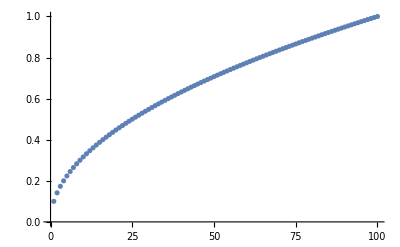

```mathematica
fac=100;
Table[{i,Sqrt[i/100]},{i,1,100}]//N
ListPlot[%]
```

```mathematica
Sqrt[1-z^2]/.z-> 2/(1-x^2)-1//PE
```

(2 ⅈ x)/((1-x) (1+x))